# One gluon radiation in onium-onium collision

Original code from Bin Wu
Created by Meijian Li on 2022.2.19
Last update on 2022.8.21

## Initialization

```mathematica
Clear["Global`*"]
```

### Global parameters

```mathematica
crntdir=NotebookDirectory[];
outdir=crntdir<>"image/";
Nc=3;
ef=2/3;
eEM=Sqrt[4π 1/137];
Qc=2/3;
Qb=1/3;
gmIR=.001;
```

### Style

#### Color

```mathematica
color1=ColorData[71,1]
color2=ColorData[48,2]
color3=ColorData[24,5]
color4=ColorData[24,4]
color5=ColorData[34,3]
color6=ColorData[24,2]
color7=ColorData[24,3]
color8=ColorData[38,4]
```

Hue[0.94, 0.7, 0.9]

RGBColor[0.963806, 0.591257, 0.601724]

RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]

RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843]

RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432]

RGBColor[1., 0.7215686274509804, 0.2196078431372549]

RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883]

RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]

```mathematica
Table[ColorData[97,i],{i,1,10}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.]}

```mathematica
mycolorlistContrast={color1,color3,color5,color6,color7,color2,color4,color8}
mycolorlistSmooth={color1,color2,color7,color6,color4,color3}
mycolorlist={color1,color2,color3,color4,color5,color6,color7,color8}
mycolorlist4={RGBColor[0.14316, 0.646571, 0.600198],RGBColor[0.0885939, 0.437201, 0.00552377],RGBColor[0.54197, 0.776883, 0.148836],RGBColor[0.697017, 0.710521, 0.0335088],RGBColor[0.937911, 0.573907, 0.307698],RGBColor[0.961318, 0, 0.032517],RGBColor[0.196658, 0.311879, 0.853681]}
```

{Hue[0.94, 0.7, 0.9],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]}

{Hue[0.94, 0.7, 0.9],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882]}

{Hue[0.94, 0.7, 0.9],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]}

{RGBColor[0.14316, 0.646571, 0.600198],RGBColor[0.0885939, 0.437201, 0.00552377],RGBColor[0.54197, 0.776883, 0.148836],RGBColor[0.697017, 0.710521, 0.0335088],RGBColor[0.937911, 0.573907, 0.307698],RGBColor[0.961318, 0, 0.032517],RGBColor[0.196658, 0.311879, 0.853681]}

```mathematica
myRed=ColorData[112,1];
myBlue=ColorData[97,1];
mygreen=color8;
mycolorlistRedGrad=Table[Blend[{myRed,White},i/8],{i,1,8}]
mycolorlistGreenGrad=Table[Blend[{mygreen,White},i/8],{i,1,8}]
blendcolorlist=Join[{color3},Table[Blend[{color1,color6},i/8],{i,1,8}]]
tempcolorlist=Table[ColorData["TemperatureMap"][i],{i,0,1,0.25}]
mycolorlist3={ColorData["TemperatureMap"][0],color3,color7,color2,ColorData["TemperatureMap"][1]}
```

{RGBColor[0.8167645, 0.301029, 0.125],RGBColor[0.8429409999999999, 0.40088199999999996, 0.25],RGBColor[0.8691175, 0.500735, 0.375],RGBColor[0.895294, 0.600588, 0.5],RGBColor[0.9214705, 0.700441, 0.625],RGBColor[0.947647, 0.8002940000000001, 0.75],RGBColor[0.9738235, 0.900147, 0.875],RGBColor[1., 1., 1.]}

{RGBColor[0.4681372549019608, 0.763235294117647, 0.6362745098039216],RGBColor[0.5441176470588236, 0.7970588235294117, 0.6882352941176471],RGBColor[0.6200980392156863, 0.8308823529411764, 0.7401960784313726],RGBColor[0.696078431372549, 0.8647058823529412, 0.7921568627450981],RGBColor[0.7720588235294118, 0.8985294117647058, 0.8441176470588235],RGBColor[0.8480392156862746, 0.9323529411764706, 0.8960784313725491],RGBColor[0.9240196078431373, 0.9661764705882353, 0.9480392156862745],RGBColor[1., 1., 1.]}

{RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.9125, 0.32644607843137263, 0.4621509803921571],RGBColor[0.925, 0.38289215686274514, 0.4275019607843139],RGBColor[0.9375, 0.4393382352941177, 0.39285294117647074],RGBColor[0.95, 0.49578431372549026, 0.35820392156862757],RGBColor[0.9625, 0.5522303921568628, 0.3235549019607844],RGBColor[0.975, 0.6086764705882353, 0.28890588235294123],RGBColor[0.9875, 0.6651225490196078, 0.25425686274509807],RGBColor[1., 0.7215686274509804, 0.2196078431372549]}

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.642359, 0.720535, 0.964988],RGBColor[0.984192, 0.987731, 0.911643],RGBColor[0.955963, 0.863115, 0.283425],RGBColor[0.817319, 0.134127, 0.164218]}

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.817319, 0.134127, 0.164218]}

```mathematica
mycolorlist
```

{Hue[0.94, 0.7, 0.9],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961]}

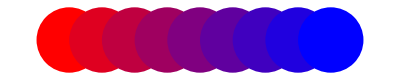

```mathematica
Graphics[Table[{Blend[{Red,Blue},x],Disk[{8 x,0}]},{x,0,1,1/8}]]
```

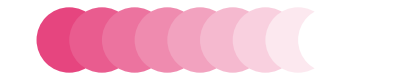

```mathematica
Graphics[Table[{Blend[{Hue[0.94, 0.7, 0.9],White},x],Disk[{8 x,0}]},{x,0,1,1/8}]]
```

```mathematica
Table[Blend[{Hue[0.94, 0.7, 0.9],White},x],{x,0,1,1/8}]
```

{RGBColor[0.9, 0.2700000000000001, 0.49680000000000024],RGBColor[0.9125, 0.36125000000000007, 0.5597000000000002],RGBColor[0.925, 0.45250000000000007, 0.6226000000000002],RGBColor[0.9375, 0.5437500000000001, 0.6855000000000002],RGBColor[0.95, 0.635, 0.7484000000000002],RGBColor[0.9625, 0.7262500000000001, 0.8113000000000001],RGBColor[0.975, 0.8175000000000001, 0.8742000000000001],RGBColor[0.9875, 0.90875, 0.9371],RGBColor[1., 1., 1.]}

```mathematica
Table[Blend[{RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],White},x],{x,0,1,1/8}]
```

{RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.4681372549019608, 0.763235294117647, 0.6362745098039216],RGBColor[0.5441176470588236, 0.7970588235294117, 0.6882352941176471],RGBColor[0.6200980392156863, 0.8308823529411764, 0.7401960784313726],RGBColor[0.696078431372549, 0.8647058823529412, 0.7921568627450981],RGBColor[0.7720588235294118, 0.8985294117647058, 0.8441176470588235],RGBColor[0.8480392156862746, 0.9323529411764706, 0.8960784313725491],RGBColor[0.9240196078431373, 0.9661764705882353, 0.9480392156862745],RGBColor[1., 1., 1.]}

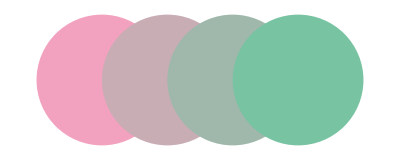

```mathematica
pinklist=Table[Blend[{RGBColor[0.95, 0.635, 0.7484000000000002],RGBColor[0.4681372549019608, 0.763235294117647, 0.6362745098039216]},x],{x,0,1,1/3}];
l=Length[pinklist];
Graphics[Table[{pinklist[[x]],Disk[{x,0}]},{x,1,l}]]
```

#### Font

```mathematica
font1="Times";
myfont="Times";
fontsizeXL=24;
fontsizeL=18;
fontsizeM=16;
fontsizeS=14;
fontsizeXS=12;
```

#### Figure

```mathematica
xlabelxplBare="x^+(GeV^-1)";
xlabelmga="m_ga_⊥/π";
ylabelpsqBare="<(p_⊥)^2> (GeV^2)";
ylabelpsqBaredp="<(p_⊥)^2>/d_p^2";
ylabelqhatdp="q̂/(d_p^2L_η^-1)";
ylabelqhatdqhat0="q̂/(q̂)_0";
xlabelxpl=Style[xlabelxplBare,FontFamily->font1,Black];
ylabelpsq=Style[ylabelpsqBare,FontFamily->font1,Black];
ylabelnorm=Style["Probability",FontFamily->font1,Black];
ylabelpsqR=Style["<(p_⊥)^2> /(q̂ L_η)",fontsizeS,FontFamily->font1,Black];
```

```mathematica
xlabelxpl
```

x^+(GeV^-1)

```mathematica
psqLegends={"<(p_⊥)^2>_(bare q)","<(p_⊥)^2>_q","<(p_⊥)^2>_total" ,"<(p_⊥)^2>_g","<(p_⊥)^2>_(q - g relative)","<(p_⊥)^2>_q+<(p_⊥)^2>_g"};
psqLegendsPBD={"<(p_⊥)^2>_(bare q)","<(p_⊥)^2>_q","<(p_⊥)^2>_total PBD." ,"<(p_⊥)^2>_g","<(p_⊥)^2>_(q - g relative) PBD.","<(p_⊥)^2>_q+<(p_⊥)^2>_g"};
normLegends={"|q⟩","|qg⟩","|q⟩+|qg⟩","|ψ(x^+=0)⟩"};
cnormLegends={"3","6^-","15","Total"};
psqAnalyticalqLegend={"<(p_⊥)^2>=q̂ x^+"};
psqAnalyticalLegends={"<(p_⊥)^2>_(bare q)","<(p_⊥)^2>_(bare g)","<(p_⊥)^2>_(bare q)+<(p_⊥)^2>_(bare g)" };
```

```mathematica
FigSizeXS=200;
FigSizeS=300;
FigSizeM=370;
FigSizeL=400;
```

```mathematica
gFrameStyle=Directive[Black,Thickness[Small],FontFamily->myfont,fontsizeM];
Clear[FNFrameLabel];
FNFrameLabel[xlabel_,ylabel_,ulabel_:"",scale_:fontsizeM+2,Rlabel_:""]:={
{Style[ylabel,FontFamily->myfont,scale,Black],
Style[Rlabel,FontFamily->myfont,scale,Black]},
{Style[xlabel,FontFamily->myfont,scale,Black],
Style[ulabel,FontFamily->myfont,scale,myRed]
(*If[ulabel==None,None,"haha"(*Style[ulabel,FontFamily->myfont,fontsizeL,myRed]*)]*)
}
};
```

```mathematica
FNFrameLabel[a,b]
```

{{b,},{a,}}

```mathematica
FNFrameLabel[a,b,c]
```

{{b,},{a,c}}

```mathematica
glegendFN=(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10,Background->White]&);glegendsFontsFN=(Style[#,fontsizeS,FontFamily->font1]&);
FNlegendsLabel[label_]:=Style[label,fontsizeS+1,FontFamily->font1,Black];
```

## Functions

### Series on IR regulator

```mathematica
Series[((x+c)^2+d)^(1/2),{x,0,4}]
```

√(c^2+d)+(c x)/(√(c^2+d))+(d x^2)/(2 (c^2+d)^(3/2))-((c d) x^3)/(2 (c^2+d)^(5/2))+((4 c^2-d) d x^4)/(8 (c^2+d)^(7/2))+O[x]^5

### 2D vector operations

```mathematica
FNpolarToXY[r_,θr_]:={r Cos[θr],r Sin[θr]};
FNXYToPolar[x_,y_]:={Sqrt[x^2+y^2],ArcTan[y/x]};
```

```mathematica
{bx,by}=FNpolarToXY[b,θb]
```

{b Cos[θb],b Sin[θb]}

```mathematica
{b,θb}=FNXYToPolar[bx,by]
```

{√(bx^2+by^2),ArcTan[by/bx]}

```mathematica
b
```

√(bx^2+by^2)

```mathematica
bx
```

b Cos[θb]

```mathematica
(* a+b *)
FNplusPolar[a_,θa_,b_,θb_]:=Module[{resx,resy},
{resx,resy}=FNpolarToXY[a,θa]+FNpolarToXY[b,θb];
FNXYToPolar[resx,resy]
];
(* a.b *)
FNdotpolar[a_,b_,θa_,θb_]:=a b Cos[θa-θb];
(* (a-b)^2 *)
FNminus2polar[a_,b_,θa_,θb_]:=a^2+b^2-2a b Cos[θa-θb];
(* (a+b)^2 *)
FNplus2polar[a_,b_,θa_,θb_]:=a^2+b^2+2a b Cos[θa-θb];
(* (a-b-c)^2 *)
FNminus2m3polar[a_,b_,c_,θa_,θb_,θc_]:=a^2+b^2+c^2-2a b Cos[θa-θb]-2a c Cos[θa-θc]+2c b Cos[θc-θb];
(* (a-b+c)^2 *)
FNminus2p3polar[a_,b_,c_,θa_,θb_,θc_]:=a^2+b^2+c^2-2a b Cos[θa-θb]+2a c Cos[θa-θc]-2c b Cos[θc-θb];
```

### Functions

```mathematica
FNx1234PolartoXY[b_,θb_,xA_,rA_,θA_,xB_,rB_,θB_]:=Module[{bx,by,rAx,rAy,rBx,rBy},
{bx,by}=FNpolarToXY[b,θb];
{rAx,rAy}=FNpolarToXY[rA,θA];
{rBx,rBy}=FNpolarToXY[rB,θB];
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
{{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}}
]
```

```mathematica
(*FNx1234PolartoPolar[b_,θb_,xA_,rA_,θA_,xB_,rB_,θB_]:=
{FNplusPolar[b,θb],{x2x,x2y},{x3x,x3y},{x4x,x4y}}*)
```

## Hadron Light-front wavefunction (LFWF)

## Basis representation

References on convention
1. Phys.Rev.D 96 (2017) 1, 016022
2. W. Qian, S. Jia, Y. Li, and J. P. Vary, Phys. Rev. C 102, 055207 (2020)

### Basis function

#### Definition

Basis functions in the transverse and longitudinal spaces, respectively

```mathematica
(*Subscript[ϕ, mn](p^⊥)*)
bfphimm[n_,m_,k_,θ_,κ_]:=Piecewise[{{κ^-1 √((4π n!)/(n+Abs[m])! ) (k/κ )^Abs[m] Exp[-k^2/ (2 κ^2) ] LaguerreL[n,Abs[m],k^2/κ^2 ] Exp[ⅈ m θ],m!=0},{κ^-1 √(4π ) Exp[-k^2/ (2 κ^2) ] LaguerreL[n,0,k^2/κ^2 ] ,m==0}}];
(*Subscript[ϕ, mn](r^⊥)*)
bfphicor[n_,m_,r_,θ_,κ_]:=Piecewise[{{κ √(( n!)/(n+Abs[m])!π ) (r κ )^Abs[m] Exp[-κ^2 r^2/2 ] LaguerreL[n,Abs[m],r^2 κ^2 ] Exp[ⅈ m θ](-1)^n ⅈ^Abs[m],m!=0},{κ √(1/π ) Exp[-κ^2 r^2/2 ] LaguerreL[n,0,r^2 κ^2 ] (-1)^n ,m==0}}];

(*Subscript[χ, l](x)*)
bfchi[l_,x_,α_,β_]:=√((4 π (2 l+α+β+1) Gamma[l+1] Gamma[l+α+β+1])/(Gamma[l+α+1] Gamma[l+β+1])) x^(β/2) (1-x)^(α/2) JacobiP[l,α,β,2 x-1];
```

3D basis function in the momentum space, ψ_nml(k_⊥,x), and in the coordinate space (ψ̃)_nml(r_⊥,x)

```mathematica
(* Subscript[ψ, nml](k_⊥,x)
*)bfpsinmlmm[n_,m_,l_,k_,θ_,x_,κ_,mf_]:=bfphimm[n,m,k/Sqrt[x(1-x)],θ,κ]bfchi[l,x,(4 mf^2)/κ^2,(4 mf^2)/κ^2];
(* Subscript[ψ̃, nml](r_⊥,x)
*)bfpsinmlcor[n_,m_,l_,r_,θ_,x_,κ_,mf_]:=Sqrt[x(1-x)]bfphicor[n,m,r Sqrt[x(1-x)],θ,κ]bfchi[l,x,(4 mf^2)/κ^2,(4 mf^2)/κ^2];
```

LFWF with basis coefficients as a list of {n,m,l,s1,s2,...,coeffcient } with colnm the column number of the coefficient

```mathematica
lfwfmj[basiscoelist_,k_,θ_,x_,σ1_,σ2_,κ_,mf_,colnm_:1]:=Module[{s1,s2,n,m,l,w,sum=0,rnm},
rnm=Length[basiscoelist];
Do[s1=basiscoelist[[i,4]];
s2=basiscoelist[[i,5]];
If[s1==σ1&&s2==σ2,
n=basiscoelist[[i,1]];
m=basiscoelist[[i,2]];
l=basiscoelist[[i,3]];
w=basiscoelist[[i,5+colnm]];
sum=sum+w bfpsinmlmm[n,m,l,k,θ,x,κ,mf]],{i,1,rnm}];sum];
lfwfmjcor[basiscoelist_,r_,θ_,x_,σ1_,σ2_,κ_:1.34,mf_:1.27,colnm_:1]:=Module[{s1,s2,n,m,l,w,sum=0,rnm},
rnm=Length[basiscoelist];
Do[s1=basiscoelist[[i,4]];
s2=basiscoelist[[i,5]];
If[s1==σ1&&s2==σ2,
n=basiscoelist[[i,1]];
m=basiscoelist[[i,2]];
l=basiscoelist[[i,3]];
w=basiscoelist[[i,5+colnm]];
sum=sum+w bfpsinmlcor[n,m,l,r,θ,x,κ,mf]],{i,1,rnm}];sum];
lfwfListPUA[basiscoelist_,m_,s1_,s2_,colnm_:1]:=
Select[basiscoelist[[All,{1,2,3,4,5,5+colnm}]],#[[2]]==m&&#[[4]]==s1&&#[[5]]==s2&];
```

#### Plotting ϕ_nm(k_⊥)

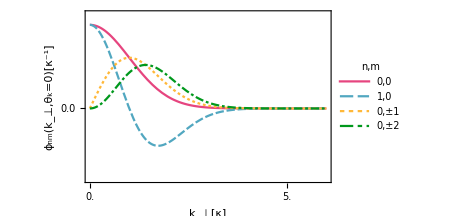

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.4},
Plot[
{bfphimm[0,0,k,0,κ]κ,
bfphimm[1,0,k,0,κ]κ,
bfphimm[0,1,k,0,κ]κ,
bfphimm[0,2,k,0,κ]κ},{k,0,6κ},
PlotRange->{Full,{-3,4}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["k_⊥[κ]",FontFamily->font1,fontsizeXL,Black],Style["ϕ_nm(k_⊥,θ_k=0)[κ^-1]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0","1,0","0,±1","0,±2"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["n,m",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

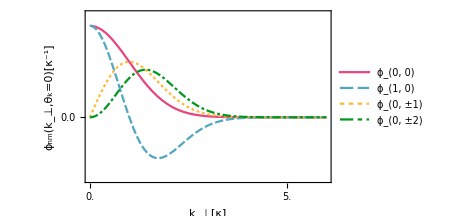

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.4},
Plot[
{bfphimm[0,0,k,0,κ]κ,
bfphimm[1,0,k,0,κ]κ,
bfphimm[0,1,k,0,κ]κ,
bfphimm[0,2,k,0,κ]κ},{k,0,6κ},
PlotRange->{Full,{-2.4,4}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["k_⊥[κ]",FontFamily->font1,fontsizeXL,Black],Style["ϕ_nm(k_⊥,θ_k=0)[κ^-1]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"ϕ_(0, 0)","ϕ_(1, 0)","ϕ_(0, ±1)","ϕ_(0, ±2)"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2}],{Right,Top}]
]
]
```

#### Plotting (ϕ̃)_nm(r_⊥)

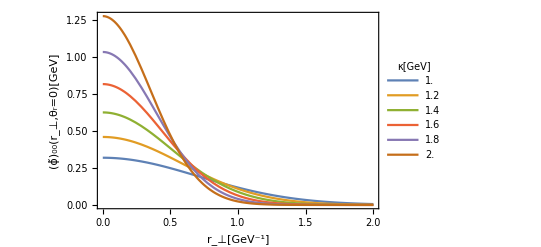

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[bfphicor[0,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,2},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ϕ̃)_00(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Top}]
]
]
```

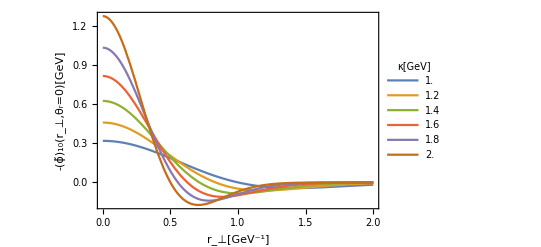

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[- bfphicor[1,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,2},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["-(ϕ̃)_10(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Top}]
]
]
```

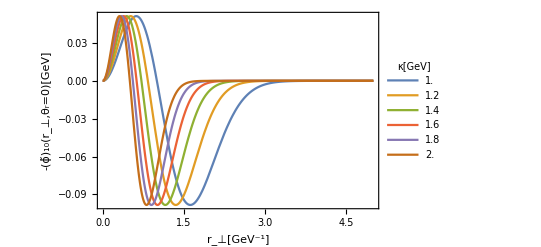

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[-r^2 bfphicor[1,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,5},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["-r_⊥(ϕ̃)_10(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

```mathematica
With[{q2tck=.5,vtck=.08},
Plot[Evaluate@Table[-r^2 bfphicor[1,0,r,0,κ]bfphicor[0,0,r,0,κ],{κ,1,2,.2}],{r,0,5},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[GeV^-1]",FontFamily->font1,fontsizeXL,Black],Style["-(ϕ̃)_10(r_⊥,θ_r=0)[GeV]",fontsizeXL,FontFamily->font1,Black]},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@Table[κ,{κ,1,2,.2}],LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",3},LegendLabel->Style["κ[GeV]",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

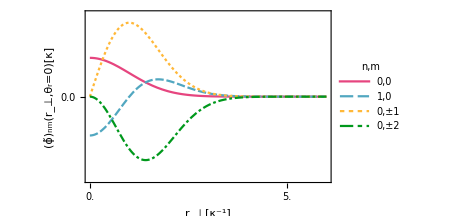

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.08},
Plot[
{bfphicor[0,0,r,0,κ]/κ,
bfphicor[1,0,r,0,κ]/κ,
Im[bfphicor[0,1,r,0,κ]]/κ,
bfphicor[0,2,r,0,κ]/κ},{r,0,6/κ},
PlotRange->{Full,{-1.2,1.2}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ϕ̃)_nm(r_⊥,θ_r=0)[κ]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{1/κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{1/κ q2tck i,,{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0","1,0","0,±1","0,±2"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["n,m",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

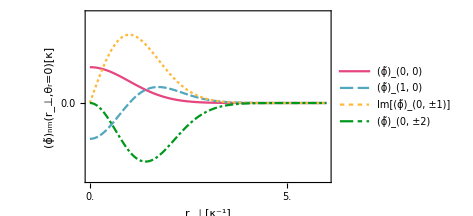

```mathematica
With[{κ=1.34,q2tck=.5,vtck=.1},
Plot[
{bfphicor[0,0,r,0,κ]/κ,
bfphicor[1,0,r,0,κ]/κ,
Im[bfphicor[0,1,r,0,κ]]/κ,
bfphicor[0,2,r,0,κ]/κ},{r,0,6/κ},
PlotRange->{Full,{-1.2,1.4}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ϕ̃)_nm(r_⊥,θ_r=0)[κ]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{1/κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{1/κ q2tck i,,{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"(ϕ̃)_(0, 0)","(ϕ̃)_(1, 0)","Im[(ϕ̃)_(0, ±1)]","(ϕ̃)_(0, ±2)"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2}],{Right,Top}]
]
]
```

#### Plotting χ_l(x)

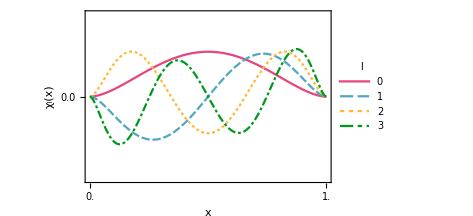

```mathematica
With[{κ=1.34,mf=1.27,q2tck=.1,vtck=.8},
α=4 mf^2/κ^2;
β=α;
Plot[
{bfchi[0,x,α,β],bfchi[1,x,α,β],bfchi[2,x,α,β],bfchi[3,x,α,β]},{x,0,1},
PlotRange->{Full,{-10,10}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
PlotStyle->colorlist1,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["x",FontFamily->font1,fontsizeXL,Black],Style["χ_l(x)",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{0,1,2,3},LegendMarkerSize->fontsizeXXL,
Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["l",fontsizeL,FontFamily->font1,Italic]],{Right,Bottom}
]
]
]
```

#### Plotting ψ_nml(k_⊥,x)

```mathematica
With[{mf=1.27,κ=1.34,q2tck=.5,vtck=1.6},
Plot3D[
{bfpsinmlmm[0,0,0,k,0,x,κ,mf],
bfpsinmlmm[1,0,0,k,0,x,κ,mf],
bfpsinmlmm[0,0,2,k,0,x,κ,mf],
(*bfpsinmlmm[0,1,1,k,0,x,κ,mf],*)
(*bfpsinmlmm[0,-1,1,k,0,x,κ,mf],*)
bfpsinmlmm[0,2,0,k,0,x,κ,mf](*,
bfpsinmlmm[0,-2,0,k,0,x,κ,mf]*)},{k,-3κ,3κ},{x,0,1},
PlotRange->All]
]
```

General::munfl: Exp[-62923.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
"ψ_nml(k_⊥,θ_k=0,x=0.5) [κ^-1]"
```

```mathematica
With[{mf=1,κ=1,q2tck=.25,vtck=2,x=1/2},
Plot[
{bfpsinmlmm[0,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[1,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[0,0,2,k,0,x,κ,mf]κ,
(*bfpsinmlmm[0,1,1,k,0,x,κ,mf]κ,*)
(*bfpsinmlmm[0,-1,1,k,0,x,κ,mf]κ,*)
bfpsinmlmm[0,1,0,k,0,x,κ,mf]κ
(*,
bfpsinmlmm[0,-2,0,k,0,x,κ,mf]κ*)},{k,0,3κ},
PlotRange->{Full,{-18,24}},
PlotRangePadding->None,
ImageSize->400{1,goldRatio},
AspectRatio->1-1/ⅇ,
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["k_⊥[κ]",FontFamily->font1,fontsizeXL,Black],Style["ψ_nml((k⃗)_⊥,x) [κ^-1]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±1,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Top}](*,
Epilog->Inset[Style["θ_k=0, x=0.5",FontFamily->myfont,fontsizeL],Scaled[{.5,1.05}]],
PlotRangeClipping->False*)
]
]
```

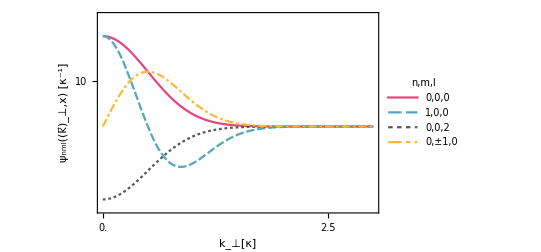
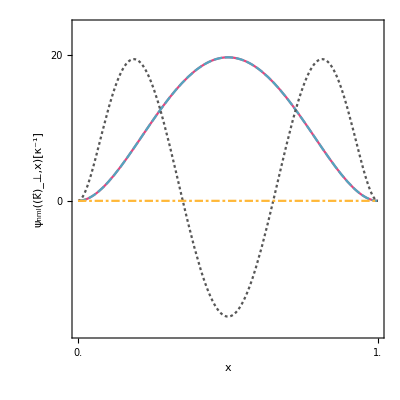

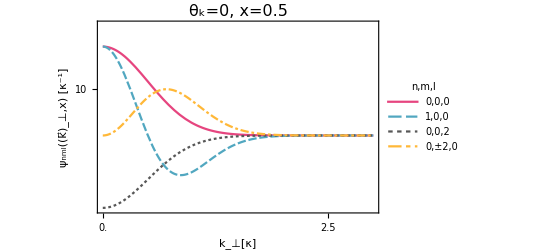
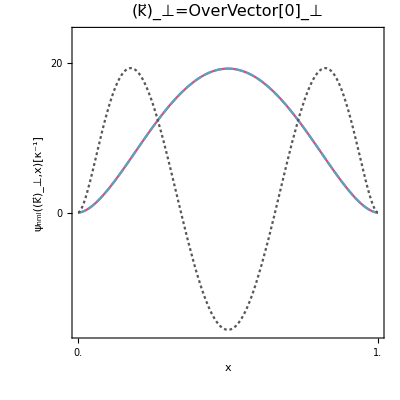

```mathematica
With[
{κ=1,mf=1,q2tck=.1,vtck=2,k=0},
α=4 mf^2/κ^2;
(*α//Print;*)
β=α;
Plot[
{bfpsinmlmm[0,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[1,0,0,k,0,x,κ,mf]κ,
bfpsinmlmm[0,0,2,k,0,x,κ,mf]κ,
bfpsinmlmm[0,1,0,k,0,x,κ,mf]κ
},{x,0,1},
PlotRange->{Full,{-18,24}},
PlotRangePadding->None,
ImageSize->goldRatio{400,400},
AspectRatio->1,
(*ImagePadding->{{80,20},{50,10}},*)
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
(*PlotLabel->Style["k_⊥=0, θ_k=0","Title",FontFamily->myfont,fontsizeL],*)
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{
{Style["ψ_nml((k⃗)_⊥,x)[κ^-1]",fontsizeXL,FontFamily->font1,Black],None},
{Style["x",FontFamily->font1,fontsizeXL,Black],None}
},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}}(*,
Epilog->Inset[Style["(k⃗)_⊥=OverVector[0]_⊥",FontFamily->myfont,fontsizeL],Scaled[{.5,1.05}]],
PlotRangeClipping->False*)
]
]
```

-Graphics-

#### Plotting (ψ̃)_nml(r_⊥,x)

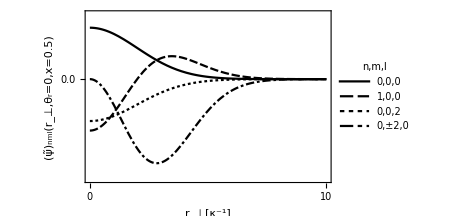

```mathematica
With[{mf=1.27,κ=1.34,q2tck=1,vtck=.4,x=1/2},
Plot[
{bfpsinmlcor[0,0,0,r,0,x,κ,mf],
bfpsinmlcor[1,0,0,r,0,x,κ,mf],
bfpsinmlcor[0,0,2,r,0,x,κ,mf],
bfpsinmlcor[0,2,0,r,0,x,κ,mf]},{r,0,10/κ},
PlotRange->{Full,{-4,2.6}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
(*PlotStyle->colorlist1,*)
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ψ̃)_nml(r_⊥,θ_r=0,x=0.5)",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{1/κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{1/κ q2tck i,,{0,-0.025}},{1/κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±2,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

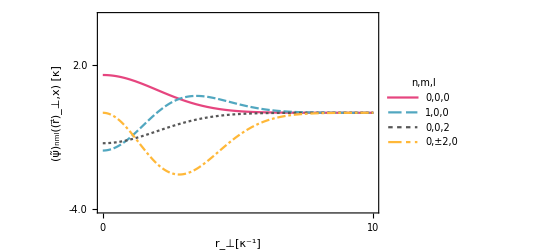

```mathematica
With[{mf=1,κ=1,q2tck=1,vtck=.4,x=1/2},
Plot[
{bfpsinmlcor[0,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[1,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,0,2,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,-2,0,r,0,x,κ,mf]/κ},
{r,0,10/κ},
PlotRange->{Full,{-4,4}},
PlotRangePadding->None,
ImageSize->400{1,goldRatio},
AspectRatio->1-1/ⅇ,
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["r_⊥[κ^-1]",FontFamily->font1,fontsizeXL,Black],Style["(ψ̃)_nml((r⃗)_⊥,x) [κ]",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{κ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{κ q2tck i,,{0,-0.025}},{κ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±2,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Column",2},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Top}](*,
Epilog->Inset[Style["θ_k=0, x=0.5",FontFamily->myfont,fontsizeL],Scaled[{.5,1.05}]],
PlotRangeClipping->False*)
]
]
```

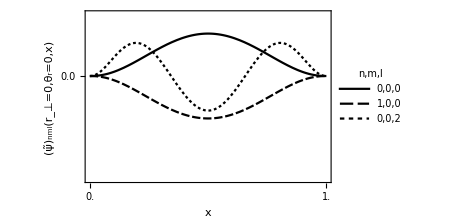

```mathematica
With[{mf=1.27,κ=1.34,q2tck=.1,vtck=.5,r=0},
Plot[
{
bfpsinmlcor[0,0,0,r,0,x,κ,mf],
bfpsinmlcor[1,0,0,r,0,x,κ,mf],
bfpsinmlcor[0,0,2,r,0,x,κ,mf]
},{x,0,1},
PlotRange->{Full,{-5,3}},
PlotRangePadding->None,
ImageSize->350,
PlotTheme->"Monochrome",
(*PlotStyle->colorlist1,*)
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["x",FontFamily->font1,fontsizeXL,Black],Style["(ψ̃)_nml(r_⊥=0,θ_r=0,x)",fontsizeXL,FontFamily->font1,Black]},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}},
PlotLegends->
Placed[
LineLegend[(Style[#,fontsizeS,FontFamily->font1]&)/@{"0,0,0","1,0,0","0,0,2",(*"0±11",*)"0,±2,0"},LegendMarkerSize->fontsizeXXL,Spacings->0.5,
LegendFunction->(Framed[#1,FrameMargins->1,FrameStyle->LightGray,RoundingRadius->10]&),LegendLayout->{"Row",1},LegendLabel->Style["n,m,l",fontsizeL,FontFamily->font1]],{Right,Bottom}]
]
]
```

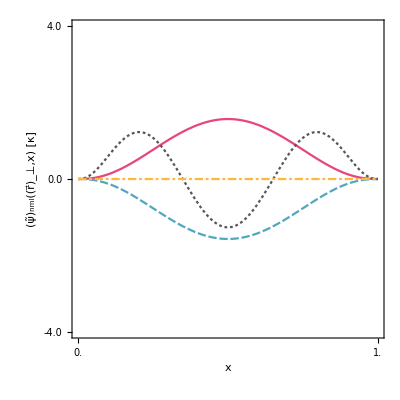

```mathematica
With[
{κ=1,mf=1,q2tck=.1,vtck=.4,r=0},
α=4 mf^2/κ^2;
(*α//Print;*)
β=α;
Plot[
{bfpsinmlcor[0,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[1,0,0,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,0,2,r,0,x,κ,mf]/κ,
bfpsinmlcor[0,-2,0,r,0,x,κ,mf]/κ
},{x,0,1},
PlotRange->{Full,{-4,4}},
PlotRangePadding->None,
ImageSize->goldRatio{400,400},
AspectRatio->1,
(*ImagePadding->{{80,20},{50,10}},*)
PlotTheme->"Monochrome",
PlotStyle->colorlist2,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{
{Style["(ψ̃)_nml((r⃗)_⊥,x) [κ]",fontsizeXL,FontFamily->font1,Black],None},
{Style["x",FontFamily->font1,fontsizeXL,Black],None}
},
FrameTicks->{
{Table[If[Mod[i,5]==0,{vtck*i,NumberForm[vtck i,{3,1}],{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}],
Table[If[Mod[i,5]==0,{vtck*i,,{0,-0.025}},{vtck*i,,{0,-0.015}}],{i,-40,40}]},
{Table[If[Mod[i,2]==0,{ q2tck i,NumberForm[q2tck i,3],{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}],
Table[If[Mod[i,2]==0,{ q2tck i,,{0,-0.025}},{ q2tck i,,{0,-0.015}}],{i,0,40}]}}
]
]
```

### Model LFWF

Reference
1. e-Print: 2111.07087 [hep-ph]

To use the following LFWF as a function of (r, θ, x), call, e.g., 
lfwfmjcor[listWF1SVmj0,r,θ,x,1,-1,kappa,mf]

#### Basis states LF-W,0^(-+)

```mathematica
listWF1SPS={
{0,0,0,1,-1, Sqrt[1/2]},
{0,0,0,-1,1,-Sqrt[1/2]}};
listWF2SPS={
{1,0,0,1,-1, Sqrt[1/3]},
{1,0,0,-1,1,- Sqrt[1/3]},
{0,0,2,1,-1,- Sqrt[1/6]},
{0,0,2,-1,1, Sqrt[1/6]}};
listWF1PPS={
{0,-1,0,1,1,- Sqrt[1/2]},
{0,1,0,-1,-1,-Sqrt[1/2]}
};
```

#### Basis states LF-W,1^(--)

```mathematica
listWF1SVmj0={
{0,0,0,1,-1, Sqrt[1/2]},
{0,0,0,-1,1,Sqrt[1/2]}};
listWF1SVmj1={
{0,0,0,1,1,1}};
listWF1SVmjm1={
{0,0,0,-1,-1,1}};
```

```mathematica
listWF2SVmj0={
{1,0,0,1,-1, Sqrt[1/3]},
{1,0,0,-1,1, Sqrt[1/3]},
{0,0,2,1,-1,- Sqrt[1/6]},
{0,0,2,-1,1, -Sqrt[1/6]}};
listWF2SVmj1={
{1,0,0,1,1, Sqrt[2/3]},
{0,0,2,1,1,- Sqrt[1/3]}};
listWF2SVmjm1={
{1,0,0,-1,-1, Sqrt[2/3]},
{0,0,2,-1,-1,- Sqrt[1/3]}};
```

```mathematica
With[{d0=-Sqrt[2/5],d1=-Sqrt[3/5]},
listWF1DVmj0={
{0,-1,1,1,1,d1 Sqrt[1/2]},
{0,1,1,-1,-1,-d1 Sqrt[1/2]},
{0,0,2,1,-1,d0 Sqrt[1/3]},
{0,0,2,-1,1,d0 Sqrt[1/3]},
{1,0,0,1,-1,d0 Sqrt[1/6]},
{1,0,0,-1,1,d0 Sqrt[1/6]}
};
];
```

```mathematica
With[{a=Sqrt[3/5],b=-Sqrt[3/10],c=Sqrt[1/10]},
listWF1DVmj1={
{0,2,0,-1,-1,a},
{0,1,1,1,-1,-b Sqrt[1/2]},
{0,1,1,-1,1,-b Sqrt[1/2]},
{0,0,2,1,1,c Sqrt[2/3]},
{1,0,0,1,1,c Sqrt[1/3]}
};
listWF1DVmjm1={
{0,-2,0,1,1,a},
{0,-1,1,1,-1,b Sqrt[1/2]},
{0,-1,1,-1,1,b Sqrt[1/2]},
{0,0,2,-1,-1,c Sqrt[2/3]},
{1,0,0,-1,-1,c Sqrt[1/3]}
};
];
```

## The qq^-+qq^-→ qq^-+qq^-+g cross section

## Leading order calculation

```mathematica
anaLO[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Abs[1/2Log[((bx-x4+x1)^2+(by-y4+y1)^2)((bx-x3+x2)^2+(by-y3+y2)^2)/((bx-x3+x1)^2+(by-y3+y1)^2)/((bx-x4+x2)^2+(by-y4+y2)^2)]]^2
```

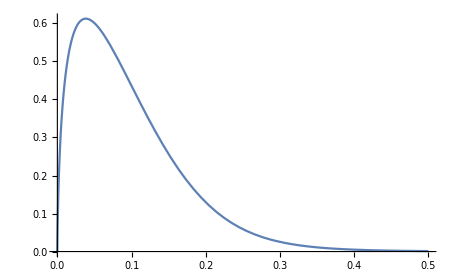

```mathematica
With[{by=0,rAx=0.4,rAy=0.4,rBx=0.4,rBy=0.4,xA=1/2,xB=1/2},
Module[{rA,θA,rB,θB,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
Plot[
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
(*{{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}}//Print;*)
bx anaLO[{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}],
{bx,0,.5},PlotRange->All]
]]
```

```mathematica
With[{rAx=0.4,rAy=0,rBx=0.4,rBy=0,xA=1/2,xB=1/2},
Module[{rA,θA,rB,θB,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
Plot3D[
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
(*{{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}}//Print;*)
Sqrt[bx^2+by^2] anaLO[{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}],
{bx,-0.5,.5},{by,-0.5,.5},PlotRange->All]
]]
```

-Graphics3D-

```mathematica
FNsigmaLO[{bx_,by_},{nA_,mA_,lA_},{nB_,mB_,lB_},κ_:0.61,mf_:0.48,rUV_:∞]:=Module[{rA,xA,θA,rB,xB,θB,
rAx,rAy,rBx,rBy,
x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
NIntegrate[
rAx=rA Cos[θA];
rBx=rB Cos[θB];
rAy=rA Sin[θA];
rBy=rB Sin[θB];
x1x=bx+(1-xA)rAx ;
x1y=by+(1-xA)rAy ;
x2x=bx-xA rAx ;
x2y=by-xA rAy ;
x3x=(1-xB)rBx ;
x3y=(1-xB)rBy ;
x4x=-xB rBx ;
x4y=-xB rBy ;
anaLO[{bx,by},{x1x,x1y},{x2x,x2y},{x3x,x3y},{x4x,x4y}]Abs[bfpsinmlcor[nA,mA,lA,rA,0,xA,κ,mf]]^2Abs[bfpsinmlcor[nB,mB,lB,rB,0,xB,κ,mf]]^2,
{θA,0,2π},{θB,0,2π},
{rA,0,rUV},{rB,0,rUV},
{xA,0,1},{xB,0,1}]
]
```

```mathematica
sigmaLOb=Table[{ibx,FNsigmaLO[{ibx,0},{0,0,0},{0,0,0}]},{ibx,0,20,.2}];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1827.05 and 267.439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1340.57 and 106.576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 972.953 and 84.2377 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
sigmaLOb
```

{{0.,1827.05},{0.2,1340.57},{0.4,972.953},{0.6,695.29},{0.8,490.408},{1.,348.405},{1.2,256.468},{1.4,182.868},{1.6,132.572},{1.8,98.8208},{2.,73.09},{2.2,53.9946},{2.4,40.1087},{2.6,31.1969},{2.8,23.9649},{3.,18.4278},{3.2,14.4537},{3.4,11.401},{3.6,9.07126},{3.8,7.40173},{4.,5.97249},{4.2,4.91327},{4.4,4.04933},{4.6,3.35529},{4.8,2.81748},{5.,2.36814},{5.2,2.00721},{5.4,1.70442},{5.6,1.46673},{5.8,1.27129},{6.,1.10159},{6.2,0.958229},{6.4,0.837259},{6.6,0.751842},{6.8,0.647885},{7.,0.572113},{7.2,0.506918},{7.4,0.454836},{7.6,0.405614},{7.8,0.363549},{8.,0.325875},{8.2,0.294819},{8.4,0.267069},{8.6,0.241935},{8.8,0.219899},{9.,0.200679},{9.2,0.182997},{9.4,0.167343},{9.6,0.153466},{9.8,0.140901},{10.,0.129904},{10.2,0.119789},{10.4,0.110783},{10.6,0.102423},{10.8,0.094851},{11.,0.0880462},{11.2,0.0817664},{11.4,0.0760779},{11.6,0.0707358},{11.8,0.0661432},{12.,0.061786},{12.2,0.0576153},{12.4,0.0540063},{12.6,0.0506109},{12.8,0.0474666},{13.,0.0445592},{13.2,0.041853},{13.4,0.0393733},{13.6,0.037107},{13.8,0.0349648},{14.,0.0329907},{14.2,0.0311282},{14.4,0.0294135},{14.6,0.0278247},{14.8,0.0263308},{15.,0.0249129},{15.2,0.0236119},{15.4,0.0223926},{15.6,0.0212603},{15.8,0.0201914},{16.,0.0191864},{16.2,0.0182553},{16.4,0.0173653},{16.6,0.0165378},{16.8,0.0157769},{17.,0.0150413},{17.2,0.0143432},{17.4,0.013684},{17.6,0.0130715},{17.8,0.0124894},{18.,0.0119325},{18.2,0.0114184},{18.4,0.0109305},{18.6,0.010462},{18.8,0.0100206},{19.,0.00960802},{19.2,0.00921151},{19.4,0.00882572},{19.6,0.00847352},{19.8,0.00813418},{20.,0.00781175}}

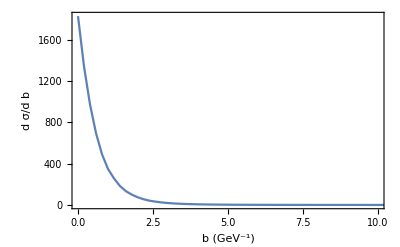

```mathematica
ListPlot[sigmaLOb,PlotRange->{{0,10},All},
Joined->True,
Frame->True,
FrameStyle->Directive[Black,Thickness[Medium],fontsizeL,FontFamily->font1],
FrameLabel->{Style["b (GeV^-1)",FontFamily->font1,fontsizeXL,Black],Style["d σ/d b",fontsizeXL,FontFamily->font1,Black]}]
```

## Next-to-leading order calculation

## Full calculation by Hong, cross checking

## Dimensional regularization

#### I_β

```mathematica
Integrate[Exp[-m x-n/x]x^ϵ,{x,0,∞}]
```

ConditionalExpression[2 m^(1/2 (-1-ϵ)) n^((1+ϵ)/2) BesselK[-1-ϵ,2 √m √n], Re[m]>0&&Re[n]>0]

```mathematica
Integrate[Exp[-n/x]x^(ϵ-1),{x,0,∞},Assumptions->n>0&& ϵ∈Reals]
```

ConditionalExpression[n^ϵ Gamma[-ϵ], ϵ<0]

```mathematica
Integrate[Exp[-n/x]x^(ϵ-1),{x,0,∞},Assumptions->n>0&& ϵ>0]
```

Integrate::idiv: Integral of ⅇ^(-n/x) x^(-1+ϵ) does not converge on {0,∞}.

Integrate[ⅇ^(-n/x) x^(-1+ϵ),{x,0,∞},Assumptions→n>0&&ϵ>0]

```mathematica
Series[-π^e x^(2 e)Gamma[-e],{e,0,1}]
```

1/e+(EulerGamma+Log[π]+2 Log[x])+1/12 (6 EulerGamma^2+π^2+12 EulerGamma Log[π]+6 Log[π]^2+24 EulerGamma Log[x]+24 Log[π] Log[x]+24 Log[x]^2) e+O[e]^2

```mathematica
Series[Gamma[e],{e,0,2}]
```

1/e-EulerGamma+1/12 (6 EulerGamma^2+π^2) e+1/6 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1]) e^2+O[e]^3

```mathematica
D[BesselK[1+ϵ,cc x],x]//Simplify
```

-1/2 cc (BesselK[ϵ,cc x]+BesselK[2+ϵ,cc x])

```mathematica
D[x^(1+ϵ)BesselK[1+ϵ,cc x],x]//FullSimplify
```

-cc x^(1+ϵ) BesselK[ϵ,cc x]

```mathematica
BesselK[0,0]
```

∞

```mathematica
BesselK[1,0]
```

ComplexInfinity

```mathematica
Series[Gamma[x],{x,0,2}]
```

1/x-EulerGamma+1/12 (6 EulerGamma^2+π^2) x+1/6 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1]) x^2+O[x]^3

```mathematica
x Gamma[-x]==-Gamma[1-x]
```

x Gamma[-x]==-Gamma[1-x]

```mathematica
Integrate[Exp[ⅈ cc aa] aa^(-ϵ)(1-aa)^(-1-ϵ),{aa,0,1}]//FullSimplify
```

ConditionalExpression[1/2 cc^(1/2+ϵ) ⅇ^((ⅈ cc)/2) √π (BesselJ[-1/2-ϵ,cc/2]+ⅈ BesselJ[1/2-ϵ,cc/2]) Gamma[-ϵ], Re[ϵ]<0]

```mathematica
Series[1/2 cc^(1/2+ϵ) ⅇ^((ⅈ cc)/2) √π (BesselJ[-1/2-ϵ,cc/2]+ⅈ BesselJ[1/2-ϵ,cc/2]) ,{ϵ,0,1}]//FullSimplify
```

ⅇ^(ⅈ cc)+ⅇ^(ⅈ cc) (-CosIntegral[cc]+Log[cc]+ⅈ SinIntegral[cc]) ϵ+O[ϵ]^2

```mathematica
Series[-1/ϵ(1/(4π)^(1-ϵ))(1/(k2)^(1+ϵ))1/2 cc^(1/2+ϵ) ⅇ^((ⅈ cc)/2) √π (BesselJ[-1/2-ϵ,cc/2]+ⅈ BesselJ[1/2-ϵ,cc/2]) ,{ϵ,0,1}]//FullSimplify
```

-ⅇ^(ⅈ cc)/(4 (k2 π) ϵ)+(ⅇ^(ⅈ cc) (CosIntegral[cc]+Log[k2]-Log[4 cc π]-ⅈ SinIntegral[cc]))/(4 k2 π)-1/(16 (k2 π))(2 ⅇ^(ⅈ cc) (Log[k2]-Log[4 cc π]) (2 CosIntegral[cc]+Log[k2]-Log[4 cc π]-2 ⅈ SinIntegral[cc])+√cc ⅇ^((ⅈ cc)/2) √π (BesselJ^(2,0)[-1/2,cc/2]+ⅈ BesselJ^(2,0)[1/2,cc/2])) ϵ+O[ϵ]^2

```mathematica
Series[1/Sin[ϵ x],{ϵ,0,2}]
```

1/(x ϵ)+(x ϵ)/6+O[ϵ]^3

```mathematica
BesselJ[-1/2-ϵ,cc/2]
```

```mathematica
Series[BesselJ[-1/2-ϵ,cc/2],{ϵ,0,2}]
```

(2 Cos[cc/2])/(√cc √π)-BesselJ^(1,0)[-1/2,cc/2] ϵ+1/2 BesselJ^(2,0)[-1/2,cc/2] ϵ^2+O[ϵ]^3

```mathematica
Gamma[1]
```

1

```mathematica
Series[ 1/Gamma[1-ϵ],{ϵ,0,2}]
```

1-EulerGamma ϵ+(EulerGamma^2/2-π^2/12) ϵ^2+O[ϵ]^3

```mathematica
Series[ (k2/(4π))^(-ϵ),{ϵ,0,2}]
```

1+(-Log[k2]+Log[4 π]) ϵ+1/2 (Log[k2]^2-2 Log[k2] Log[4 π]+Log[4 π]^2) ϵ^2+O[ϵ]^3

```mathematica
Series[(k2/(4π))^(-ϵ) aa^(-ϵ)(1-aa)^(-1-ϵ)/Gamma[1-ϵ],{ϵ,0,2}]
```

1/(1-aa)+((EulerGamma+Log[1-aa]+Log[aa]+Log[k2]-Log[4 π]) ϵ)/(-1+aa)+1/(12 (-1+aa))(-6 EulerGamma^2+π^2-12 EulerGamma Log[1-aa]-6 Log[1-aa]^2-12 EulerGamma Log[aa]-12 Log[1-aa] Log[aa]-6 Log[aa]^2-12 EulerGamma Log[k2]-12 Log[1-aa] Log[k2]-12 Log[aa] Log[k2]-6 Log[k2]^2+12 EulerGamma Log[4 π]+12 Log[1-aa] Log[4 π]+12 Log[aa] Log[4 π]+12 Log[k2] Log[4 π]-6 Log[4 π]^2) ϵ^2+O[ϵ]^3

```mathematica
Series[ aa^(-ϵ)(1-aa)^(-1-ϵ),{ϵ,0,2}]
```

```mathematica
Series[ aa^(-ϵ)(1-aa)^(-1-ϵ),{aa,0,2}]
```

aa^-ϵ (1+(1+ϵ) aa+1/2 (1+ϵ) (2+ϵ) aa^2+O[aa]^3)

```mathematica
Series[ aa^(-ϵ),{ϵ,0,2}]
```

1-Log[aa] ϵ+1/2 Log[aa]^2 ϵ^2+O[ϵ]^3

```mathematica
Series[ (1-aa)^(-1-ϵ),{ϵ,0,2}]
```

1/(1-aa)+(Log[1-aa] ϵ)/(-1+aa)-(Log[1-aa]^2 ϵ^2)/(2 (-1+aa))+O[ϵ]^3

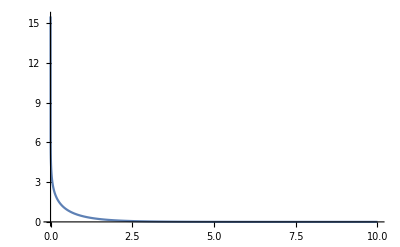

```mathematica
Plot[BesselK[0,x],{x,0,10},PlotRange->All]
```

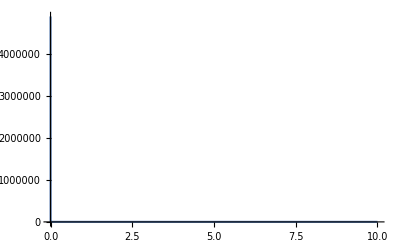

```mathematica
Plot[BesselK[1,x],{x,0,10},PlotRange->All]
```

```mathematica
Limit[BesselK[0,x],x->0]
```

∞

```mathematica
Limit[BesselK[0,x]x,x->0]
```

0

```mathematica
Limit[BesselK[1,x]x,x->0]
```

1

```mathematica
Limit[BesselK[1,x],x->0,Direction->"FromAbove"]
```

∞

## Result

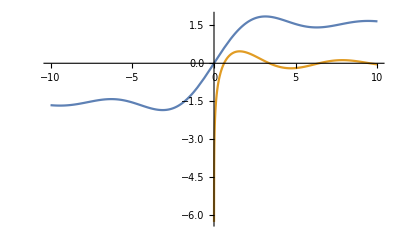

```mathematica
Plot[{SinIntegral[x],CosIntegral[x]},{x,-10,10}]
```

#### I_0

```mathematica
FNI0noPhase[η_,ρ_]:=1/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/4/Abs[ρ]]+EulerGamma );
FNI0[η_,ρ_]:=Exp[ⅈ ρ η]FNI0noPhase[η,ρ];
```

plot

```mathematica
FNI0[η,ρ]
```

(ⅇ^(ⅈ η ρ) (EulerGamma+CosIntegral[η Abs[ρ]]+Log[η/(4 Abs[ρ])]-ⅈ SinIntegral[η ρ]))/(4 π)

```mathematica
With[{ρ=.3},Limit[FNI0[η,ρ],η->0]]
With[{ρ=.3},Limit[FNI0[η,ρ],η->∞,Direction->"FromAbove"]]
With[{ρ=.3},Limit[FNI0noPhase[η,ρ],η->0]]
With[{ρ=.3},Limit[FNI0noPhase[η,ρ],η->∞,Direction->"FromAbove"]]
```

-∞

ⅇ^((0.+2. ⅈ) Interval[{-2.44758×10^-307,3.14159}]) ∞

-∞

∞

ⅇ^((0.+2. ⅈ) Interval[{-2.44758×10^-307,3.14159}]) ∞

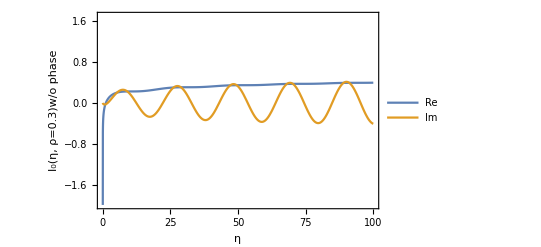

```mathematica
With[{ρ=.3},
Plot[
{Re[FNI0noPhase[η,ρ]],Im[FNI0[η,ρ]]},{η,0,100},
PlotRange->{All,{-2,1.7}},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_0(η, ρ=0.3)w/o phase"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]]
```

```mathematica
FNHZI0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
```

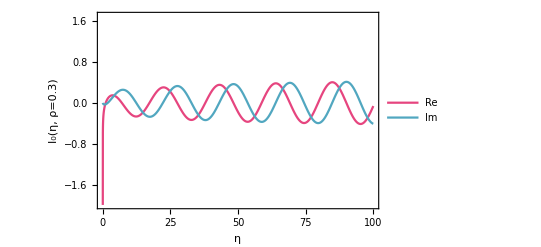

```mathematica
With[{ρ=.3},
Plot[
{Re[FNHZI0Fun[ρ,η]],Im[FNHZI0Fun[ρ,η]]},{η,0,100},
PlotStyle->{color1,color3},
PlotRange->{All,{-2,1.7}},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_0(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]]
```

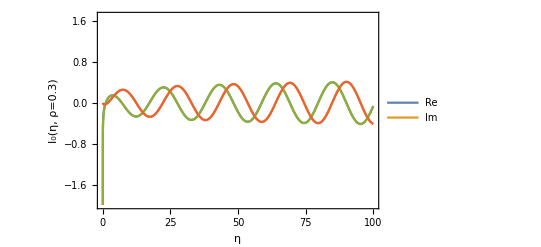

```mathematica
With[{ρ=.3},
Plot[
{Re[FNI0[η,ρ]],Im[FNI0[η,ρ]],Re[FNHZI0Fun[ρ,η]],Im[FNHZI0Fun[ρ,η]]},{η,0,100},
PlotRange->{All,{-2,1.7}},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_0(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]]
```

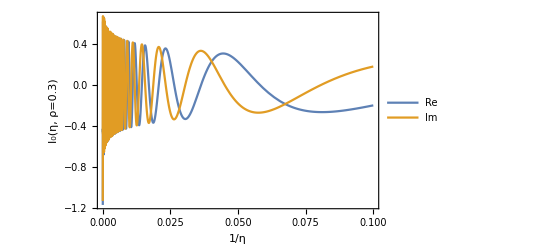

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI0[1/ηInv,ρ]],Im[FNI0[1/ηInv,ρ]]},{ηInv,0,.1},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_0(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]];
figThis//Print;
(*Export[outdir<>"I0_etaInv.pdf",figThis];
Clear[figThis];*)
```

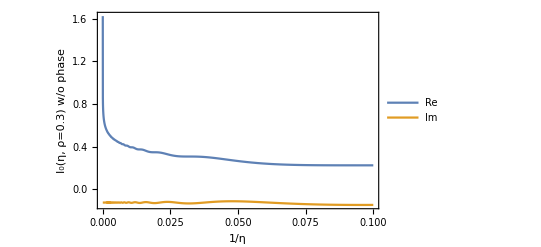

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI0noPhase[1/ηInv,ρ]],Im[FNI0noPhase[1/ηInv,ρ]]},{ηInv,0,.1},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_0(η, ρ=0.3) w/o phase"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]];
figThis//Print;
(*Export[outdir<>"I0woPhase_etaInv.pdf",figThis];
Clear[figThis];*)
```

small k_T

```mathematica
tmp=Series[FNI0[η,ρ],{η,0,1}]//Simplify;
I0leading=Normal[tmp]
```

(EulerGamma-Log[2]+Log[η])/(2 π)+(ⅈ η ρ (-1+2 EulerGamma-Log[4]+2 Log[η]))/(4 π)

```mathematica
tmp=Series[FNI0noPhase[η,ρ],{η,0,1}]//Simplify;
I0leading=Normal[tmp]
```

-(ⅈ η ρ)/(4 π)+(EulerGamma-Log[2]+Log[η])/(2 π)

```mathematica
FNI0smallkT[η_,ρ_]:=(EulerGamma-Log[2]+Log[η])/(2 π)+(ⅈ η ρ (-1+2 EulerGamma-Log[4]+2 Log[η]))/(4 π);FNI0noPhasesmallkT[η_,ρ_]:=-(ⅈ η ρ)/(4 π)+(EulerGamma-Log[2]+Log[η])/(2 π);
```

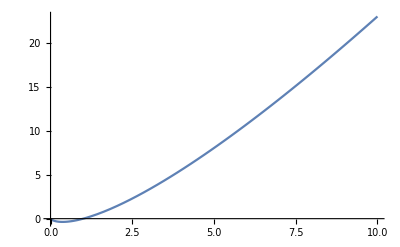

```mathematica
Plot[x Log[x],{x,0,10}]
```

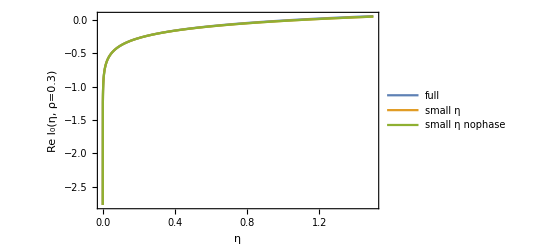

```mathematica
With[{ρ=.3},
Plot[
{Re[FNI0[η,ρ]],Re[FNI0smallkT[η,ρ]],Re[FNI0noPhasesmallkT[η,ρ]]},{η,0,1.5},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","Re I_0(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"full","small η","small η nophase"},LegendFunction->glegendFN],{Right,Top}]
]]
```

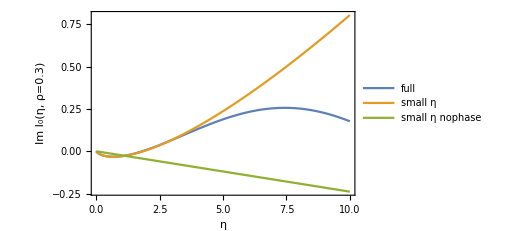

```mathematica
With[{ρ=.3},
Plot[
{Im[FNI0[η,ρ]],Im [FNI0smallkT[η,ρ]],Im[FNI0noPhasesmallkT[η,ρ]]},{η,0,10},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","Im I_0(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"full","small η","small η nophase"},LegendFunction->glegendFN],{Right,Top}]
]]
```

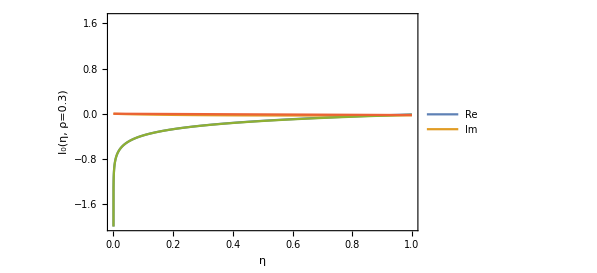

```mathematica
With[{ρ=.3},
Plot[
{Re[FNI0[η,ρ]],Im[FNI0[η,ρ]],Re[FNI0smallkT[η,ρ]],Im[FNI0smallkT[η,ρ]]},{η,0,1},
PlotRange->{All,{-2,1.7}},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_0(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]]
```

large k_T

```mathematica
FNI0[1/ηInv,ρ]
```

1/(4 π)ⅇ^((ⅈ ρ)/ηInv) (EulerGamma+CosIntegral[Abs[ρ]/ηInv]+Log[1/(4 ηInv Abs[ρ])]-ⅈ SinIntegral[ρ/ηInv])

```mathematica
FNI0noPhase[1/ηInv,ρ]
```

1/(4 π)(EulerGamma+CosIntegral[Abs[ρ]/ηInv]+Log[1/(4 ηInv Abs[ρ])]-ⅈ SinIntegral[ρ/ηInv])

```mathematica
tmp=Series[ FNI0noPhase[1/ηInv,ρ],{ηInv,0,1},Assumptions->ηInv>0]
```

Cos[Abs[ρ]/ηInv+O[ηInv]^2] O[ηInv]^2+Cos[ρ/ηInv+O[ηInv]^2] ((ⅈ ηInv)/(4 π ρ)+O[ηInv]^2)+(1/(8 π ρ)(2 EulerGamma ρ-ⅈ π √(ρ^2)-4 ρ Log[2]-2 ρ Log[ηInv]-2 ρ Log[Abs[ρ]])+O[ηInv]^2)+O[ηInv]^2 Sin[ρ/ηInv+O[ηInv]^2]+(ηInv/(4 π Abs[ρ])+O[ηInv]^2) Sin[Abs[ρ]/ηInv+O[ηInv]^2]

```mathematica
(tmp//Normal//FullSimplify)/.{ηInv->1/η}//FullSimplify
```

(Abs[ρ] (-ⅈ π η √(ρ^2)+2 ⅈ Cos[η ρ]+2 η ρ (EulerGamma-Log[(4 Abs[ρ])/η]))+2 ρ Sin[η Abs[ρ]])/(8 π η ρ Abs[ρ])

```mathematica
1/(8 π η ρ)(-ⅈ π η √(ρ^2)+2 ⅈ Cos[η ρ]+2 η ρ (EulerGamma-Log[(4 Abs[ρ])/η]))
(+2  Sin[η Abs[ρ]])/(8 π η Abs[ρ])
```

```mathematica
(-ⅈ π η √(ρ^2)+2 ⅈ Cos[η ρ])/(8 π η ρ)+(EulerGamma-Log[(4 Abs[ρ])/η])/(4 π)
(+  Sin[η Abs[ρ]])/(4 π η Abs[ρ])
```

```mathematica
I0largekTleading=Exp[ⅈ ρ η]/(4 π) (EulerGamma-Log[(4 Abs[ρ])/η]+
Sin[η Abs[ρ]]/(η Abs[ρ])+(ⅈ Cos[η ρ])/(η ρ)-(ⅈ π Abs[ρ])/(2 ρ))
```

1/(4 π)ⅇ^(ⅈ η ρ) (EulerGamma-(ⅈ π Abs[ρ])/(2 ρ)+(ⅈ Cos[η ρ])/(η ρ)-Log[(4 Abs[ρ])/η]+Sin[η Abs[ρ]]/(η Abs[ρ]))

```mathematica
FNI0largekT[η_,ρ_]:=1/(4 π)ⅇ^(ⅈ η ρ) (EulerGamma-(ⅈ π Abs[ρ])/(2 ρ)+(ⅈ Cos[η ρ])/(η ρ)-Log[(4 Abs[ρ])/η]+Sin[η Abs[ρ]]/(η Abs[ρ]));
FNI0noPhaselargekT[η_,ρ_]:=1/(4 π)(EulerGamma-(ⅈ π Abs[ρ])/(2 ρ)+(ⅈ Cos[η ρ])/(η ρ)-Log[(4 Abs[ρ])/η]+Sin[η Abs[ρ]]/(η Abs[ρ]));
```

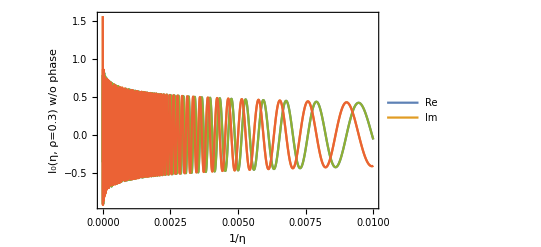

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI0[1/ηInv,ρ]],Im[FNI0[1/ηInv,ρ]],Re[FNI0largekT[1/ηInv,ρ]],Im[FNI0largekT[1/ηInv,ρ]]},{ηInv,0,.01},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_0(η, ρ=0.3) w/o phase"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]];
figThis//Print;
(*Export[outdir<>"I0woPhase_etaInv.pdf",figThis];
Clear[figThis];*)
```

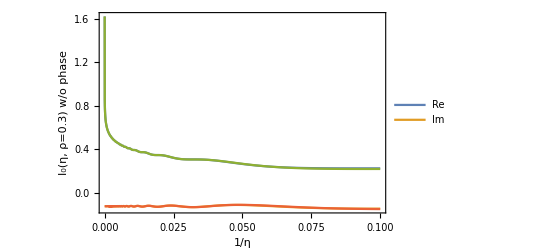

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI0noPhase[1/ηInv,ρ]],Im[FNI0noPhase[1/ηInv,ρ]],Re[FNI0noPhaselargekT[1/ηInv,ρ]],Im[FNI0noPhaselargekT[1/ηInv,ρ]]},{ηInv,0,.1},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_0(η, ρ=0.3) w/o phase"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
]];
figThis//Print;
(*Export[outdir<>"I0woPhase_etaInv.pdf",figThis];
Clear[figThis];*)
```

#### I_1, integrand

```mathematica
FNI1innoPhase[η_,ρ_,α_]:=η/(4π)α /Sqrt[α(1-α)](BesselK[1,η Sqrt[α(1-α)]]-1/(η Sqrt[α(1-α)]));
FNI1in[η_,ρ_,α_]:=Exp[ⅈ α ρ η]FNI1innoPhase[η,ρ,α]
```

```mathematica
FNI1in[η,ρ,α]
```

(ⅇ^(ⅈ α η ρ) α η (-1/(√((1-α) α) η)+BesselK[1,√((1-α) α) η]))/(4 π √((1-α) α))

plot

```mathematica
Integrate[Exp[ⅈ α ρ η]/(1-α),{α,0,1}]
```

```mathematica
Integrate[1/(1-α),{α,0,1}]
```

Integrate::idiv: Integral of 1/(1-α) does not converge on {0,1}.

∫_0^1 1/(1-α)ⅆα

```mathematica
Manipulate[Plot[{(α η (BesselK[1,√((1-α) α) η]))/(4 π √((1-α) α)),(α η (-1/(√((1-α) α) η)))/(4 π √((1-α) α)),FNI1innoPhase[η,ρ,α]},{α,0,1}],{η,.0001,10},{ρ,-1,1}]
```

```mathematica
Manipulate[Plot[(α η (BesselK[1,√((1-α) α) η]))/(4 π √((1-α) α)),{α,0,1}],{η,.0001,10},{ρ,-1,1}]
```

```mathematica
Manipulate[Plot[FNI1innoPhase[η,ρ,α],{α,0,1}],{η,.0001,10},{ρ,-1,1}]
```

```mathematica
With[{η=10,ρ=.3},NIntegrate[FNI1in[η,ρ,α],{α,0,1}]]
```

0.204381-0.164849 ⅈ

```mathematica
With[{ρ=.3,α=.5},
Limit[FNI1in[η,ρ,α],η->0]//Print;
Limit[FNI1in[η,ρ,α],η->∞,Direction->"FromAbove"]//Print;
Limit[FNI1innoPhase[η,ρ,α],η->0]//Print;
Limit[FNI1innoPhase[η,ρ,α],η->∞,Direction->"FromAbove"]//Print;
]
```

0.

-0.159155 2.71828^((0.+2. ⅈ) Interval[{-8.9003×10^-308,3.14159}])

0.

-0.159155

```mathematica
Integrate[FNI1in[η,ρ,α],{α,0,1}]
```

∫_0^1 (ⅇ^(ⅈ α η ρ) α η (-1/(√((1-α) α) η)+BesselK[1,√((1-α) α) η]))/(4 π √((1-α) α))ⅆα

```mathematica
With[{ρ=.3},
Limit[NIntegrate[FNI1in[η,ρ,α],{α,0,1}],η->0]//Print;
Limit[NIntegrate[FNI1in[η,ρ,α],{α,0,1}],η->∞,Direction->"FromAbove"]//Print;
Limit[NIntegrate[FNI1innoPhase[η,ρ,α],{α,0,1}],η->0]//Print;
Limit[NIntegrate[FNI1innoPhase[η,ρ,α],{α,0,1}],η->∞,Direction->"FromAbove"]//Print;
]
```

NIntegrate::inumr: The integrand (ⅇ^((0.+0.3 ⅈ) α η) α η (-1/(√((1-α) α) η)+BesselK[1,√((1+Times[«2»]) α) η]))/(4 π √((1-α) α)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

$Aborted

```mathematica
With[{ρ=.3},Table[{η,NIntegrate[FNI1in[η,ρ,α],{α,0,1}]},{η,0.0001,100,10}]]
```

{{0.0001,-2.15382×10^-9-4.33889×10^-14 ⅈ},{10.0001,0.204386-0.164843 ⅈ},{20.0001,-0.222279+0.177954 ⅈ},{30.0001,0.226138-0.243958 ⅈ},{40.0001,-0.207621+0.271216 ⅈ},{50.0001,0.180754-0.321573 ⅈ},{60.0001,-0.142862+0.345332 ⅈ},{70.0001,0.0991853-0.380602 ⅈ},{80.0001,-0.0489431+0.393424 ⅈ},{90.0001,-0.00458755-0.411638 ⅈ}}

```mathematica
listI1eta=With[{ρ=.3},Table[{η,NIntegrate[FNI1in[η,ρ,α],{α,0,1}]},{η,0.0001,100,1}]];
```

```mathematica
listI1etaRe=listI1eta;
listI1etaRe[[All,2]]=Re[listI1etaRe[[All,2]]];
listI1etaIm=listI1eta;
listI1etaIm[[All,2]]=Im[listI1eta[[All,2]]];
```

```mathematica
listI1etaRe
```

{{0.0001,-2.15382×10^-9},{1.0001,-0.0322622},{2.0001,-0.0754493},{3.0001,-0.103263},{4.0001,-0.107056},{5.0001,-0.0856689},{6.0001,-0.0424695},{7.0001,0.0162862},{8.0001,0.082668},{9.0001,0.148117},{10.0001,0.204386},{11.0001,0.244373},{12.0001,0.262803},{13.0001,0.256717},{14.0001,0.225744},{15.0001,0.172109},{16.0001,0.100408},{17.0001,0.0171517},{18.0001,-0.0698715},{19.0001,-0.152354},{20.0001,-0.222279},{21.0001,-0.272701},{22.0001,-0.298433},{23.0001,-0.296562},{24.0001,-0.266758},{25.0001,-0.211331},{26.0001,-0.135046},{27.0001,-0.0446996},{28.0001,0.0514981},{29.0001,0.144678},{30.0001,0.226138},{31.0001,0.288154},{32.0001,0.324717},{33.0001,0.332104},{34.0001,0.309254},{35.0001,0.257886},{36.0001,0.182372},{37.0001,0.0893582},{38.0001,-0.0128296},{39.0001,-0.114936},{40.0001,-0.207621},{41.0001,-0.282316},{42.0001,-0.332021},{43.0001,-0.351957},{44.0001,-0.340025},{45.0001,-0.29702},{46.0001,-0.226579},{47.0001,-0.134876},{48.0001,-0.0300703},{49.0001,0.0784162},{50.0001,0.180754},{51.0001,0.267597},{52.0001,0.330939},{53.0001,0.364849},{54.0001,0.366031},{55.0001,0.334134},{56.0001,0.271811},{57.0001,0.184492},{58.0001,0.079911},{59.0001,-0.0325829},{60.0001,-0.142862},{61.0001,-0.240937},{62.0001,-0.31786},{63.0001,-0.366544},{64.0001,-0.382416},{65.0001,-0.363844},{66.0001,-0.312303},{67.0001,-0.232256},{68.0001,-0.130769},{69.0001,-0.0168852},{70.0001,0.0991853},{71.0001,0.206979},{72.0001,0.296725},{73.0001,0.360233},{74.0001,0.391637},{75.0001,0.387942},{76.0001,0.349303},{77.0001,0.27903},{78.0001,0.183301},{79.0001,0.0706196},{80.0001,-0.0489431},{81.0001,-0.164649},{82.0001,-0.266059},{83.0001,-0.343976},{84.0001,-0.391279},{85.0001,-0.403574},{86.0001,-0.379604},{87.0001,-0.321368},{88.0001,-0.233965},{89.0001,-0.125137},{90.0001,-0.00458755},{91.0001,0.116884},{92.0001,0.228355},{93.0001,0.319758},{94.0001,0.382793},{95.0001,0.411682},{96.0001,0.403695},{97.0001,0.359411},{98.0001,0.282676},{99.0001,0.180266}}

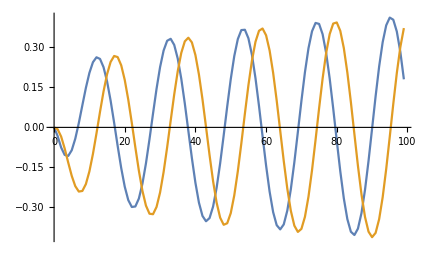

```mathematica
ListPlot[{listI1etaRe,listI1etaIm},Joined->True]
```

```mathematica
listI01eta=With[{ρ=.3},Table[{η,FNI0[η,ρ]+NIntegrate[FNI1in[η,ρ,α],{α,0,1}]},{η,0.0001,100,1}]];
```

```mathematica
listI01etaRe=listI01eta;
listI01etaRe[[All,2]]=Re[listI01etaRe[[All,2]]];
listI01etaIm=listI01eta;
listI01etaIm[[All,2]]=Im[listI01eta[[All,2]]];
```

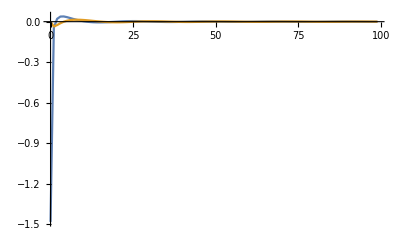

```mathematica
ListPlot[{listI01etaRe,listI01etaIm},Joined->True,PlotRange->All]
```

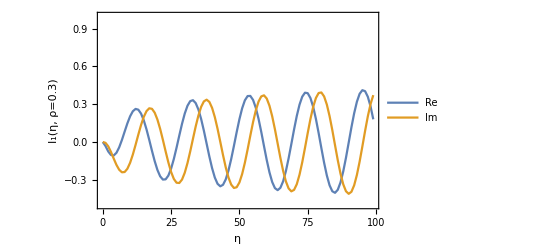

```mathematica
figThis=
ListPlot[{listI1etaRe,listI1etaIm},Joined->True,
PlotRange->{All,{-.5,1}},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_1(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
];
figThis//Print;
Export[outdir<>"I1_eta.pdf",figThis];
Clear[figThis];
```

```mathematica
Plot[x Log[x],{x,0,10}]
```

-Graphics-

```mathematica
listI1etanoPhase=With[{ρ=.3},Table[{η,NIntegrate[FNI1innoPhase[η,ρ,α],{α,0,1}]},{η,0.0001,100,1}]];
```

```mathematica
listI1etanoPhaseRe=listI1etanoPhase;
listI1etanoPhaseRe[[All,2]]=Re[listI1etanoPhaseRe[[All,2]]];
listI1etanoPhaseIm=listI1etanoPhase;
listI1etanoPhaseIm[[All,2]]=Im[listI1etanoPhase[[All,2]]];
```

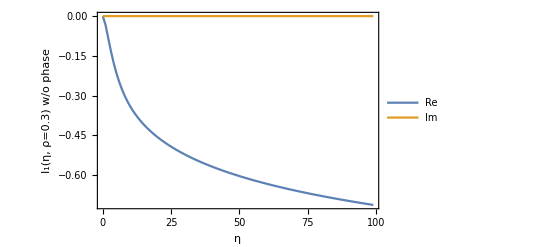

```mathematica
figThis=
ListPlot[{listI1etanoPhaseRe,listI1etanoPhaseIm},Joined->True,
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_1(η, ρ=0.3) w/o phase"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
];
figThis//Print;
Export[outdir<>"I1noPhase_eta.pdf",figThis];
Clear[figThis];
```

```mathematica
listI1etaInv=With[{ρ=.3},Table[{ηInv,NIntegrate[FNI1in[1/ηInv,ρ,α],{α,0,1}]},{ηInv,0.0001,1,.01}]];
```

```mathematica
listI1etaInvRe=listI1etaInv;
listI1etaInvRe[[All,2]]=Re[listI1etaInvRe[[All,2]]];
listI1etaInvIm=listI1etaInv;
listI1etaInvIm[[All,2]]=Im[listI1etaInv[[All,2]]];
```

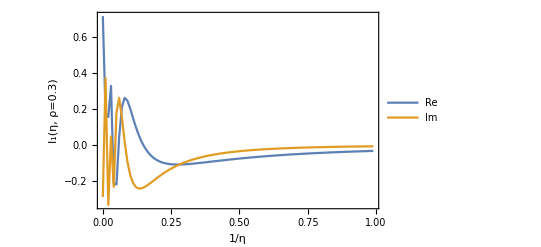

```mathematica
figThis=
ListPlot[{listI1etaInvRe,listI1etaInvIm},Joined->True,
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_1(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
];
figThis//Print;
Export[outdir<>"I1_etaInv.pdf",figThis];
Clear[figThis];
```

```mathematica
Manipulate[Plot[FNI1innoPhase[η,ρ,α],{α,0,1}],{η,0.1,100},{ρ,0.1,1}]
```

small k_T

```mathematica
Simplify[Series[FNI1in[η,ρ,α],{η,0,3}],Assumptions->α>0&& α<1]
```

(α (-1+2 EulerGamma+2 Log[1/2 √((1-α) α)]+2 Log[η]) η^2)/(16 π)+(ⅈ α^2 ρ (-1+2 EulerGamma+2 Log[1/2 √((1-α) α)]+2 Log[η]) η^3)/(16 π)+O[η]^4

```mathematica
Integrate[(α (-1+2 EulerGamma+2 Log[1/2 √((1-α) α)]+2 Log[η]) η^2)/(16 π),{α,0,1}]
```

(η^2 (-3+2 EulerGamma-Log[4]+2 Log[η]))/(32 π)

```mathematica
Integrate[(ⅈ α^2 ρ (-1+2 EulerGamma+2 Log[1/2 √((1-α) α)]+2 Log[η]) η^3)/(16 π),{α,0,1}]
```

(ⅈ η^3 ρ (-19+12 EulerGamma-12 Log[2]+12 Log[η]))/(288 π)

```mathematica
FNI1smallkT[η_,ρ_]:=(η^2 (-3+2 EulerGamma-Log[4]+2 Log[η]))/(32 π)+(ⅈ η^3 ρ (-19+12 EulerGamma-12 Log[2]+12 Log[η]))/(288 π);
```

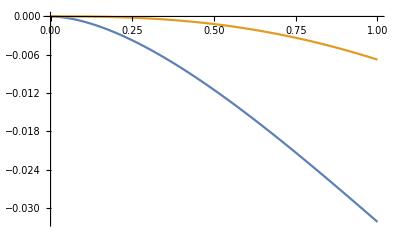

```mathematica
With[{ρ=.3},Plot[{Re[FNI1smallkT[η,ρ]],Im[FNI1smallkT[η,ρ]]},{η,0,1}]]
```

compare with the full expression

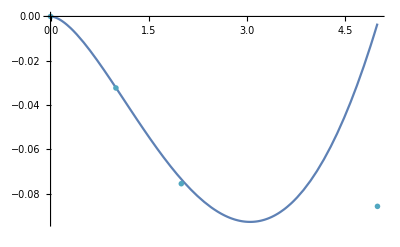

```mathematica
With[{ρ=.3},
Show[
Plot[{Re[FNI1smallkT[η,ρ]]},{η,0,5}],
ListPlot[listI1etaRe,
PlotTheme->"OpenMarkers",
PlotStyle->{color1,color3}]
]
]
```

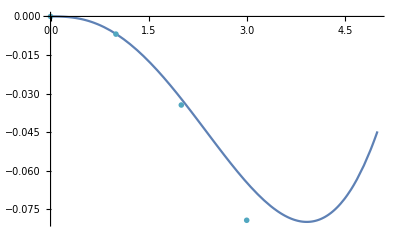

```mathematica
With[{ρ=.3},
Show[
Plot[{Im[FNI1smallkT[η,ρ]]},{η,0,5}],
ListPlot[listI1etaIm,
PlotTheme->"OpenMarkers",
PlotStyle->{color1,color3}]
]
]
```

large k_T

```mathematica
tmp=Series[FNI1in[1/ηInv,ρ,α],{ηInv,0,1},Assumptions->ηInv>0]//Normal
Integrate[tmp,{α,0,1}]
```

ⅇ^((ⅈ α ρ)/ηInv)/(4 π (-1+α))+(ⅇ^((-√(-((-1+α) α))+ⅈ α ρ)/ηInv) α)/(4 √(2 π) (-((-1+α) α))^(3/4) √ηInv)

Integrate::idiv: Integral of ⅇ^((ⅈ α ρ)/ηInv)/(4 π (-1+α))+(ⅇ^(-(√(-(Plus[«2»] α)))/ηInv+(ⅈ α ρ)/ηInv) α)/(4 √(2 π) (-((-1+α) α))^(3/4) √ηInv) does not converge on {0,1}.

```mathematica
FNI1innoPhase[η,ρ,α]//Simplify
```

-(1-√(-((-1+α) α)) η BesselK[1,√(-((-1+α) α)) η])/(4 π-4 π α)

```mathematica
ll=D[FNI1innoPhase[η,ρ,α],α]//Simplify
```

(α η (-1/(√((1-α) α) η)+BesselK[1,√((1-α) α) η]))/(4 π √((1-α) α))

-1/(16 π (-1+α)^2 α)(α (1-3 α+2 α^2) η^2 BesselK[0,√(-((-1+α) α)) η]-2 √(-((-1+α) α)) η BesselK[1,√(-((-1+α) α)) η]+α (4+(1-3 α+2 α^2) η^2 BesselK[2,√(-((-1+α) α)) η]))

```mathematica
llInv=ll/.{η->1/ηInv}
```

-1/(16 π (-1+α)^2 α)((α (1-3 α+2 α^2) BesselK[0,(√(-((-1+α) α)))/ηInv])/ηInv^2-(2 √(-((-1+α) α)) BesselK[1,(√(-((-1+α) α)))/ηInv])/ηInv+α (4+((1-3 α+2 α^2) BesselK[2,(√(-((-1+α) α)))/ηInv])/ηInv^2))

```mathematica
D[α/√((1-α) α),{α,1}]//Simplify
```

α/(2 (-((-1+α) α))^(3/2))

```mathematica
BesselK[1,0]
```

ComplexInfinity

```mathematica
Limit[√((1-α) α)BesselK[1,√((1-α) α) η],{α->0}]
```

1/η

```mathematica
Limit[(√((1-α) α) ηBesselK[1,√((1-α) α) η]-1),{α->1},Direction->"FromBelow",Assumptions->η>0]
```

0

```mathematica
Limit[(√((1-α) α) ηBesselK[1,√((1-α) α) η]-1)/(1-α),{α->1},Direction->"FromBelow",Assumptions->η>0]
```

-∞

```mathematica
√((1-α) α) ηBesselK[1,√((1-α) α) η]/.{α->1-β}
```

√((1-β) β) η BesselK[1,√((1-β) β) η]

```mathematica
Series[(√((1-β) β)  BesselK[1,√((1-β) β) η]-1/η)/β,{β,0,1},Assumptions->β>0&&η>0]
```

1/4 η (-1+2 EulerGamma+Log[β]+2 Log[η/2])+1/64 η (-32 EulerGamma-5 η^2+4 EulerGamma η^2-16 Log[β]+2 η^2 Log[β]-32 Log[η/2]+4 η^2 Log[η/2]) β+O[β]^(3/2)

```mathematica
D[√((1-α) α) ηBesselK[1,√((1-α) α) η],{α,1}]//Simplify
```

1/4 (1-2 α) η ((2 BesselK[1,√(-((-1+α) α)) η])/(√(-((-1+α) α)))-η (BesselK[0,√(-((-1+α) α)) η]+BesselK[2,√(-((-1+α) α)) η]))

```mathematica
α/√((1-α) α)D[BesselK[1,√((1-α) α) η],{α,1}]//FullSimplify
```

-((-1+2 α) η (BesselK[0,√(-((-1+α) α)) η]+BesselK[2,√(-((-1+α) α)) η]))/(4 (-1+α))

```mathematica
Series[llInv,{ηInv,0,1},Assumptions->ηInv>0]//Simplify
```

1/4 (-1/(π (-1+α)^2)+ⅇ^(-(√(-((-1+α) α)))/ηInv+O[ηInv]^3) (α/(2 √(2 π) (-((-1+α) α))^(7/4) √ηInv)+(3 α √ηInv)/(16 √(2 π) (-((-1+α) α))^(9/4))+O[ηInv]^(3/2))+ⅇ^(-(√(-((-1+α) α)))/ηInv+O[ηInv]^4) (-((1-2 α) α)/(4 (√(2 π) (-((-1+α) α))^(5/4)) ηInv^(3/2))-(α (-1+2 α))/(32 (√(2 π) (-((-1+α) α))^(7/4)) √ηInv)+(α (-9+18 α) √ηInv)/(512 √(2 π) (-((-1+α) α))^(9/4))+O[ηInv]^(3/2))+ⅇ^(-(√(-((-1+α) α)))/ηInv+O[ηInv]^4) (-((1-2 α) α)/(4 (√(2 π) (-((-1+α) α))^(5/4)) ηInv^(3/2))+(15 α (-1+2 α))/(32 √(2 π) (-((-1+α) α))^(7/4) √ηInv)+(105 α (-1+2 α) √ηInv)/(512 √(2 π) (-((-1+α) α))^(9/4))+O[ηInv]^(3/2)))

```mathematica
Integrate[-1/4 1/(π (-1+α)^2)Exp[ⅈ α ρ η],{α,0,1},Assumptions->η>0]
```

Integrate::idiv: Integral of -ⅇ^(ⅈ α η ρ)/(4 π (-1+α)^2) does not converge on {0,1}.

Integrate[-ⅇ^(ⅈ α η ρ)/(4 π (-1+α)^2),{α,0,1},Assumptions→η>0]

```mathematica
Integrate[-1/(16 π (-1+α)^2 α)(α (1-3 α+2 α^2) η^2 BesselK[0,√(-((-1+α) α)) η]-2 √(-((-1+α) α)) η BesselK[1,√(-((-1+α) α)) η]+α (4+(1-3 α+2 α^2) η^2 BesselK[2,√(-((-1+α) α)) η]))Exp[ⅈ α ρ η],{α,0,1}]
```

$Aborted

```mathematica
tmp=D[FNI1innoPhase[1/ηInv,ρ,α],α];
tmp//Simplify//Print;
Series[tmp,{ηInv,0,1},Assumptions->ηInv>0]//Normal
```

-1/(16 π (-1+α)^2 α ηInv^2)(4 α ηInv^2+α (1-3 α+2 α^2) BesselK[0,(√(-((-1+α) α)))/ηInv]-2 √(-((-1+α) α)) ηInv BesselK[1,(√(-((-1+α) α)))/ηInv]+α (1-3 α+2 α^2) BesselK[2,(√(-((-1+α) α)))/ηInv])

-1/(4 π (-1+α)^2)+ⅇ^(-(√(-((-1+α) α)))/ηInv) ((α (-1+2 α))/(8 √(2 π) (-((-1+α) α))^(5/4) ηInv^(3/2))+(7 α (-1+2 α))/(64 √(2 π) (-((-1+α) α))^(7/4) √ηInv))+ⅇ^(-(√(-((-1+α) α)))/ηInv)/(4 √(2 π) (-((-1+α) α))^(3/4) √ηInv)+(ⅇ^(-(√(-((-1+α) α)))/ηInv) α (-1+2 α))/(8 √(2 π) (-((-1+α) α))^(7/4) √ηInv)

```mathematica
tmp=D[FNI1innoPhase[1/ηInv,ρ,α],ηInv];
tmp//Print;
Series[tmp,{ηInv,0,1}]//Normal
```

```mathematica
Simplify[(α (-1/(√((1-α) α) η)+BesselK[1,√((1-α) α) η]))/(4 π √((1-α) α))+(α η (1/(√((1-α) α) η^2)+1/2 √((1-α) α) (-BesselK[0,√((1-α) α) η]-BesselK[2,√((1-α) α) η])))/(4 π √((1-α) α))]
```

-1/(8 π (-1+α))((-1+α) α η BesselK[0,√(-((-1+α) α)) η]+2 √(-((-1+α) α)) BesselK[1,√(-((-1+α) α)) η]+(-1+α) α η BesselK[2,√(-((-1+α) α)) η])

```mathematica
BesselK[1,0]
```

ComplexInfinity

```mathematica
Limit[FNI1innoPhase[η,ρ,α],{α->0}]
```

0

```mathematica
Limit[FNI1innoPhase[η,ρ,α],{α->1}]
```

-∞ Sign[η]^2

```mathematica
tmp=Series[FNI1innoPhase[1/ηInv,ρ,α],{ηInv,0,1},Assumptions->ηInv>0]//Normal
```

1/(4 π (-1+α))+(ⅇ^(-(√(-((-1+α) α)))/ηInv) α)/(4 √(2 π) (-((-1+α) α))^(3/4) √ηInv)

```mathematica
Limit[tmp,{α->0}]
Limit[tmp,{α->1}]
```

-1/(4 π)

Indeterminate

```mathematica
Series[BesselK[1,x],{x,0,2}]
```

1/x+1/4 (-1+2 EulerGamma-2 Log[2]+2 Log[x]) x+O[x]^3

```mathematica
Series[BesselK[0,x],{x,0,2}]
```

(-EulerGamma+Log[2]-Log[x])+1/4 (1-EulerGamma+Log[2]-Log[x]) x^2+O[x]^3

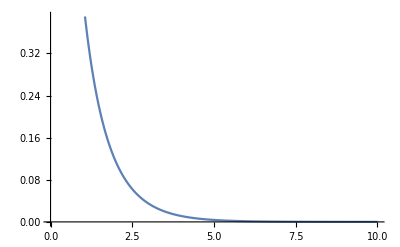

```mathematica
Plot[BesselK[0,x],{x,0,10}]
```

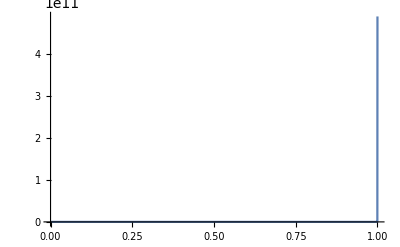

```mathematica
With[{η=.0001},Plot[BesselK[1,η Sqrt[x(1-x)]]x/Sqrt[x(1-x)],{x,0,1},PlotRange->All]]
```

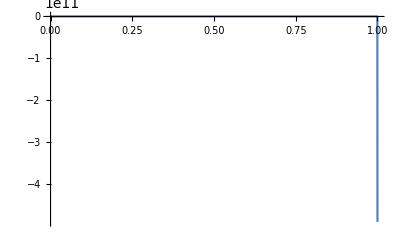

```mathematica
With[{η=.0001},Plot[(-1/(η Sqrt[x(1-x)]))x/Sqrt[x(1-x)],{x,0,1},PlotRange->All]]
```

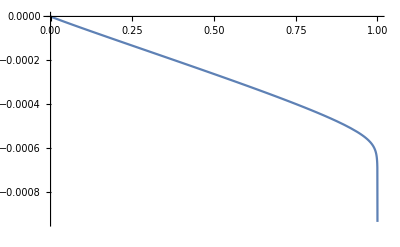

```mathematica
With[{η=.0001},Plot[(BesselK[1,η Sqrt[x(1-x)]]-1/(η Sqrt[x(1-x)]))x/Sqrt[x(1-x)],{x,0,1},PlotRange->All]]
```

```mathematica
FNI1in[1/ηInv,ρ,α]
```

(ⅇ^((ⅈ α ρ)/ηInv) α (-ηInv/(√((1-α) α))+BesselK[1,(√((1-α) α))/ηInv]))/(4 π √((1-α) α) ηInv)

```mathematica
∫_0^1 (ⅇ^((ⅈ α ρ)/ηInv)/(4 π (-1+α)))ⅆα
```

Integrate::idiv: Integral of ⅇ^((ⅈ α ρ)/ηInv)/(4 π (-1+α)) does not converge on {0,1}.

∫_0^1 ⅇ^((ⅈ α ρ)/ηInv)/(4 π (-1+α))ⅆα

```mathematica
I1largekTleading=Exp[ⅈ ρ η]η/(ⅈ ρ 16 π) (-1+2EulerGamma+logβ+2Log[η/2])
```

-(ⅈ ⅇ^(ⅈ η ρ) η (-1+2 EulerGamma+logβ+2 Log[η/2]))/(16 π ρ)

#### I_2, integrand

```mathematica
FNI2innoPhase[η_,ρ_,α_]:=-ⅈ/(4π)(BesselK[0,η Sqrt[α(1-α)]]+Log[η]);
FNI2in[η_,ρ_,α_]:=Exp[ⅈ α ρ η]FNI2innoPhase[η,ρ,α]
```

```mathematica
D[FNI2innoPhase[η,ρ,α],α]
```

(ⅈ (1-2 α) η BesselK[1,√((1-α) α) η])/(8 π √((1-α) α))

```mathematica
FNI2in[η,ρ,α]
```

-(ⅈ ⅇ^(ⅈ α η ρ) (BesselK[0,√((1-α) α) η]+Log[η]))/(4 π)

```mathematica
Limit[BesselK[0,x],x->∞]
```

0

```mathematica
Limit[BesselK[0,x]/x,x->∞]
```

0

```mathematica
Limit[x Log[x],x->0]
```

0

```mathematica
Limit[ Log[x]/x,x->∞]
```

0

plot

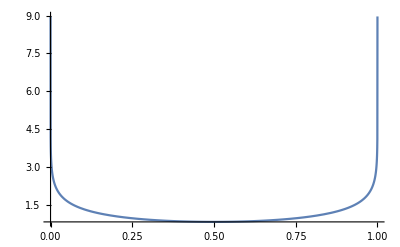

```mathematica
With[{η=.0001},Plot[ BesselK[0,η Sqrt[x(1-x)]]+Log[η],{x,0,1},PlotRange->All]]
```

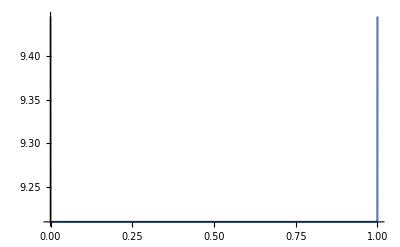

```mathematica
With[{η=1/.0001},Plot[ BesselK[0,η Sqrt[x(1-x)]]+Log[η],{x,0,1},PlotRange->All]]
```

```mathematica
With[{ρ=.3,α=.5},
Limit[FNI2in[η,ρ,α],η->0]//Print;
Limit[FNI2in[η,ρ,α],η->∞,Direction->"FromAbove"]//Print;
Limit[FNI2innoPhase[η,ρ,α],η->0]//Print;
Limit[FNI2innoPhase[η,ρ,α],η->∞,Direction->"FromAbove"]//Print;
]
```

0.-0.0643844 ⅈ

ⅇ^((0.+2. ⅈ) Interval[{-2.44758×10^-307,3.14159}]) ((-ⅈ) ∞)

0.-0.0643844 ⅈ

(-ⅈ) ∞

```mathematica
listI2eta=With[{ρ=.3},Table[{η,NIntegrate[FNI2in[η,ρ,α],{α,0,1}]},{η,0.0001,100,1}]];
```

```mathematica
listI2etaRe=listI2eta;
listI2etaRe[[All,2]]=Re[listI2etaRe[[All,2]]];
listI2etaIm=listI2eta;
listI2etaIm[[All,2]]=Im[listI2eta[[All,2]]];
```

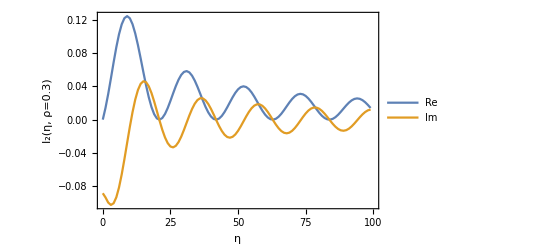

```mathematica
figThis=
ListPlot[{listI2etaRe,listI2etaIm},Joined->True,
PlotRange->{{0,100},All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_2(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
];
figThis//Print;
(*Export[outdir<>"I2_eta.pdf",figThis];*)
Clear[figThis];
```

```mathematica
listI2etaInv=With[{ρ=.3},Table[{ηInv,NIntegrate[FNI2in[1/ηInv,ρ,α],{α,0,1}]},{ηInv,0.0001,.1,.001}]];
```

```mathematica
listI2etaInvRe=listI2etaInv;
listI2etaInvRe[[All,2]]=Re[listI2etaInvRe[[All,2]]];
listI2etaInvIm=listI2etaInv;
listI2etaInvIm[[All,2]]=Im[listI2etaInv[[All,2]]];
```

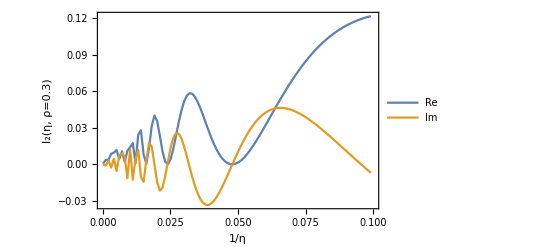

```mathematica
figThis=
ListPlot[{listI2etaInvRe,listI2etaInvIm},Joined->True,
PlotRange->{{0,.1},All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_2(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Top}]
];
figThis//Print;
Export[outdir<>"I2_etaInv.pdf",figThis];
Clear[figThis];
```

```mathematica
tmp=Simplify[Series[FNI2in[η,ρ,α],{η,0,1},Assumptions->α>0&& α<1]];
tmp=Normal[tmp];
tmp//Print;
I2leading=Integrate[tmp,{α,0,1}]
```

(ⅈ (EulerGamma+Log[1/2 √(-((-1+α) α))]))/(4 π)-(α η ρ (EulerGamma+Log[1/2 √(-((-1+α) α))]))/(4 π)

-((-2 ⅈ+η ρ) (-1+EulerGamma-Log[2]))/(8 π)

small k_T

```mathematica
FNI2smallkT[η_,ρ_]:=-((-2 ⅈ+η ρ) (-1+EulerGamma-Log[2]))/(8 π);
```

compare with the full expression

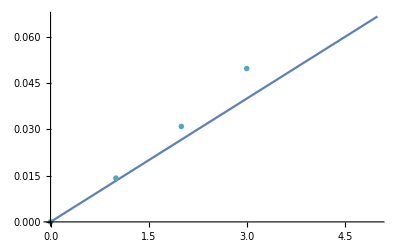

```mathematica
With[{ρ=.3},
Show[
Plot[{Re[FNI2smallkT[η,ρ]]},{η,0,5}],
ListPlot[listI2etaRe,
PlotTheme->"OpenMarkers",
PlotStyle->{color1,color3}]
]
]
```

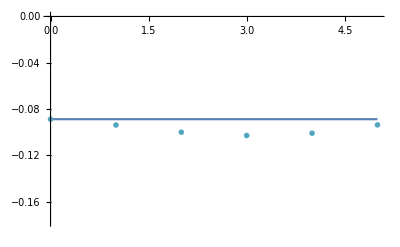

```mathematica
With[{ρ=.3},
Show[
Plot[{Im[FNI2smallkT[η,ρ]]},{η,0,5}],
ListPlot[listI2etaIm,
PlotTheme->"OpenMarkers",
PlotStyle->{color1,color3}]
]
]
```

```mathematica
D[BesselK[0,η Sqrt[α(1-α)]],α]
```

-((1-2 α) η BesselK[1,√((1-α) α) η])/(2 √((1-α) α))

```mathematica
Limit[BesselK[0,x],x->∞]
```

0

```mathematica
Series[BesselK[1,x],{x,0,1}]
```

1/x+1/4 (-1+2 EulerGamma-2 Log[2]+2 Log[x]) x+O[x]^2

```mathematica
Series[BesselK[0,1/ηInv Sqrt[α(1-α)]]ηInv,{ηInv,0,1},Assumptions->ηInv>0&&α>0]//Simplify
```

ⅇ^(-(√(-((-1+α) α)))/ηInv+O[ηInv]^2) ((√(π/2) ηInv^(3/2))/(-((-1+α) α))^(1/4)+O[ηInv]^2)

```mathematica
Series[BesselK[0,η Sqrt[α(1-α)]]+Log[η],{α,0,1},Assumptions->η>0&&α>0]//Simplify
```

1/2 (-2 EulerGamma+2 Log[2]-Log[α])+1/8 (4+2 η^2-2 EulerGamma η^2-η^2 Log[α]-2 η^2 Log[η/2]) α+O[α]^2

```mathematica
Series[BesselK[0,η Sqrt[α(1-α)]]+Log[η],{α,1,1},Assumptions->η>0&&α>0]//Simplify
```

$Aborted

```mathematica
1/2 (-2 EulerGamma-Log[α]-2 Log[η/2])//Simplify
```

-EulerGamma+Log[2]-Log[α]/2-Log[η]

```mathematica
I2largekTleading=-1/( ρ 4 π η) (-EulerGamma+Log 2-1/2logβ)(Exp[ⅈ ρ η]-1)
```

-((-1+ⅇ^(ⅈ η ρ)) (-EulerGamma+2 Log-logβ/2))/(4 π η ρ)

#### I_3

```mathematica
FNI3[η_,ρ_]:=-1/(4π)(1-Exp[ⅈ ρ η])Log [η]/(ρ η)
```

Note that the FNHZI3Fun below needs to be multiplied by -i to match the correct expression

```mathematica
FNHZI3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
FNI3[η,ρ]
```

-((1-ⅇ^(ⅈ η ρ)) Log[η])/(4 π η ρ)

plot

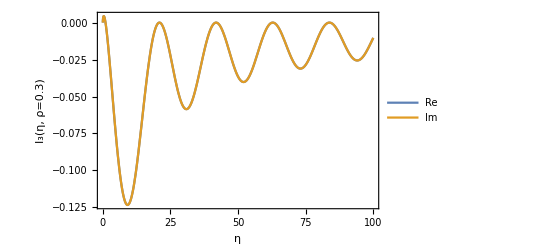

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI3[η,ρ]],Re[- ⅈ FNHZI3Fun[ρ,η]]},{η,0,100},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_3(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Bottom}]
]];
figThis//Print;
(*Export[outdir<>"I3_eta.pdf",figThis];
Clear[figThis];*)
```

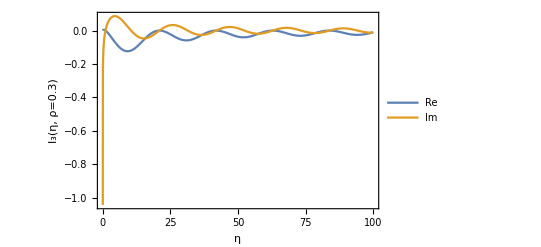

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI3[η,ρ]],Im[FNI3[η,ρ]]},{η,0,100},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","I_3(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Bottom}]
]];
figThis//Print;
(*Export[outdir<>"I3_eta.pdf",figThis];
Clear[figThis];*)
```

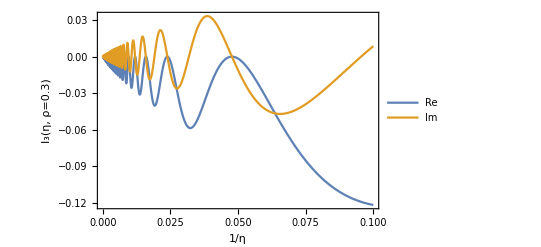

```mathematica
figThis=With[{ρ=.3},
Plot[
{Re[FNI3[1/ηInv,ρ]],Im[FNI3[1/ηInv,ρ]]},{ηInv,0,.1},
PlotRange->{All,All},
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["1/η","I_3(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"Re","Im"},LegendFunction->glegendFN],{Right,Bottom}]
]];
figThis//Print;
Export[outdir<>"I3_etaInv.pdf",figThis];
Clear[figThis];
```

small k_T

```mathematica
tmp=Series[FNI3[η,ρ],{η,0,1}];
I3leading=Normal[tmp]
```

(ⅈ Log[η])/(4 π)-(η ρ Log[η])/(8 π)

```mathematica
I3leading=(ⅈ Log[η])/(4 π)-((ρ Log[η]) η)/(8 π);
```

```mathematica
FNI3smallkT[η_,ρ_]:=(ⅈ Log[η])/(4 π)-(η ρ Log[η])/(8 π);
```

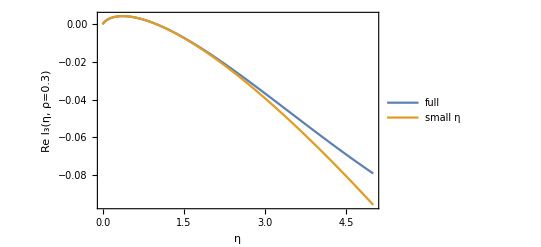

```mathematica
With[{ρ=.3},
Plot[
{Re[FNI3[η,ρ]],Re[FNI3smallkT[η,ρ]]},{η,0,5},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","Re I_3(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"full","small η"},LegendFunction->glegendFN],{Right,Top}]
]]
```

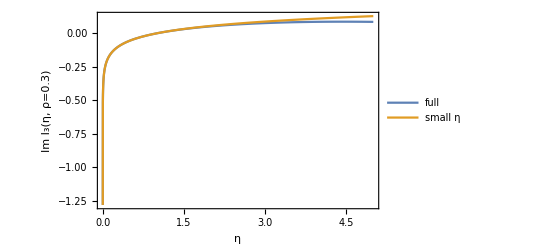

```mathematica
With[{ρ=.3},
Plot[
{Im[FNI3[η,ρ]],Im[FNI3smallkT[η,ρ]]},{η,0,5},
PlotRange->All,
Frame->True,
FrameStyle->gFrameStyle,
FrameLabel->FNFrameLabel["η","Im I_3(η, ρ=0.3)"],
PlotLegends->Placed[LineLegend[glegendsFontsFN/@{"full","small η"},LegendFunction->glegendFN],{Right,Bottom}]
]]
```

large k_T

```mathematica
Series[ Log [1/ηInv]/(ρ /ηInv),{ηInv,0,1},Assumptions->ηInv>0]//Normal//FullSimplify
```

-(ηInv Log[ηInv])/ρ

```mathematica
I3largekTleading=FNI3[η,ρ]
```

-((1-ⅇ^(ⅈ η ρ)) Log[η])/(4 π η ρ)

```mathematica
FNI3largelkT[η_,ρ_]:=FNI3[η,ρ];
```

#### Into A

small k_T

```mathematica
tmp=Series[I0leading+I1leading,{η,0,1}];
t1=Normal[tmp];
tmp//Print;
t1//Print;
```

(EulerGamma-Log[2]+Log[η])/(2 π)+(ⅈ ρ (-1+2 EulerGamma-Log[4]+2 Log[η]) η)/(4 π)+O[η]^2

(EulerGamma-Log[2]+Log[η])/(2 π)+(ⅈ η ρ (-1+2 EulerGamma-Log[4]+2 Log[η]))/(4 π)

```mathematica
tmp=Series[I2leading+I3leading,{η,0,1}];
t2=Normal[tmp];
tmp//Print;
t2//Print;
```

(ⅈ (-1+EulerGamma-Log[2]+Log[η]))/(4 π)+((ρ-EulerGamma ρ+ρ Log[2]-ρ Log[η]) η)/(8 π)+O[η]^2

(ⅈ (-1+EulerGamma-Log[2]+Log[η]))/(4 π)+(η (ρ-EulerGamma ρ+ρ Log[2]-ρ Log[η]))/(8 π)

```mathematica
FullSimplify[Series[- ki t1+(2 ki ρ η-k^2 xi)t2,{η,0,1}]]
```

1/(4 π)(-2 EulerGamma ki+ⅈ k^2 xi-ⅈ EulerGamma k^2 xi+ⅈ k^2 xi Log[2]+ki Log[4]-2 ki Log[η]-ⅈ k^2 xi Log[η])+(ρ (-2 ⅈ ki-k^2 xi+EulerGamma k^2 xi-k^2 xi Log[2]+k^2 xi Log[η]) η)/(8 π)+O[η]^2

```mathematica
1/(4 π)(-2 EulerGamma ki+ⅈ k^2 xi-ⅈ EulerGamma k^2 xi+ⅈ k^2 xi Log[2]+ki Log[4]-2 ki Log[η]-ⅈ k^2 xi Log[η])//Simplify
```

1/(4 π)(-2 EulerGamma ki+ⅈ k^2 xi-ⅈ EulerGamma k^2 xi+ⅈ k^2 xi Log[2]+ki Log[4]-(2 ki+ⅈ k^2 xi) Log[η])

```mathematica
Simplify[1/(8 π)((η ρ) (k^2 xi-2 ki η ρ) (-1+EulerGamma+Log[η/2])-4 ki (EulerGamma+Log[η/2]))]
```

(η ρ (k^2 xi-2 ki η ρ) (-1+EulerGamma+Log[η/2])-4 ki (EulerGamma+Log[η/2]))/(8 π)

```mathematica
Collect[(η ρ (k^2 xi-2 ki η ρ) (-1+EulerGamma+Log[η/2])-4 ki (EulerGamma+Log[η/2]))/(8 π),ki]
```

(k^2 xi η ρ (-1+EulerGamma+Log[η/2]))/(8 π)+(ki (-2 η^2 ρ^2 (-1+EulerGamma+Log[η/2])-4 (EulerGamma+Log[η/2])))/(8 π)

```mathematica
Simplify[1/(8 π)((-2 ⅈ) (k^2 xi-2 ki η ρ) (-1+EulerGamma+Log[η/2])+2 ⅈ ki η ρ (1-2 EulerGamma+Log[4]-2 Log[η]))]
```

-(ⅈ (ki η ρ+k^2 xi (-1+EulerGamma-Log[2])+k^2 xi Log[η]))/(4 π)

```mathematica
Collect[-(ⅈ (ki η ρ+k^2 xi (-1+EulerGamma-Log[2])+k^2 xi Log[η]))/(4 π),ki]
```

-(ⅈ ki η ρ)/(4 π)-(ⅈ (k^2 xi (-1+EulerGamma-Log[2])+k^2 xi Log[η]))/(4 π)

```mathematica
Simplify[Cos[x]Sin[y]+Sin[x]Cos[y]]
```

Sin[x+y]

```mathematica
Simplify[Cos[x]Cos[y]+Sin[x]Sin[y]]
```

Cos[x-y]

```mathematica
FNReA[{k1_,k2_},{x1_,x2_},ρη_,η_]:=Module[{k,x},
k=Sqrt[k1^2+k2^2];
x=Sqrt[x1^2+x2^2];
-4/(8π k^2){k1,k2}(EulerGamma+Log[η/2])
+1/(8π ){x1,x2}(-1+EulerGamma+Log[η/2])ρη
];
FNImA[{k1_,k2_},{x1_,x2_},ρη_,η_]:=Module[{k,x},
k=Sqrt[k1^2+k2^2];
x=Sqrt[x1^2+x2^2];
-2/(8π){x1,x2}(-1+EulerGamma+Log[η/2])
-2{k1,k2}ρη
];
```

```mathematica
FNReA[{k1,k2},{x1,x2},ρη,η]
FNImA[{k1,k2},{x1,x2},ρη,η]
```

{(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(k1 (EulerGamma+Log[η/2]))/(2 (k1^2+k2^2) π),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(k2 (EulerGamma+Log[η/2]))/(2 (k1^2+k2^2) π)}

{-2 k1 ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π),-2 k2 ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π)}

```mathematica
FNReA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]
```

{((x1x-x3x) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(kx (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π),((x1y-x3y) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(ky (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π)}

```mathematica
FNImA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]ρ1 η1
```

{η1 ρ1 (-2 kx (η1 ρ1-η3 ρ3)-((x1x-x3x) (-1+EulerGamma+Log[η13/2]))/(4 π)),η1 ρ1 (-2 ky (η1 ρ1-η3 ρ3)-((x1y-x3y) (-1+EulerGamma+Log[η13/2]))/(4 π))}

```mathematica
FNReA[{kx,ky},{x1,x2},ρη,η]+FNImA[{kx,ky},{x1,x2},ρη,η]ρy ηy//Simplify
```

```mathematica
{(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x2 (-1+EulerGamma+Log[η/2]))/(4 π))}
```

```mathematica
-ρy ηy FNReA[{kx,ky},{x1,x2},ρη,η]+FNImA[{kx,ky},{x1,x2},ρη,η]//Simplify
```

```mathematica
{1/8 (-16 kx ρη-(2 x1 (-1+EulerGamma+Log[η/2]))/π+(4 kx ηy ρy (EulerGamma+Log[η/2]))/((kx^2+ky^2) π)),1/8 (-16 ky ρη-(2 x2 (-1+EulerGamma+Log[η/2]))/π+(4 ky ηy ρy (EulerGamma+Log[η/2]))/((kx^2+ky^2) π))}
```

```mathematica
FNReA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]+FNImA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]ρ1 η1//Simplify
```

{((x1x-x3x) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(kx (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π)+η1 ρ1 (kx (-2 η1 ρ1+2 η3 ρ3)-((x1x-x3x) (-1+EulerGamma+Log[η13/2]))/(4 π)),((x1y-x3y) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(ky (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π)+η1 ρ1 (ky (-2 η1 ρ1+2 η3 ρ3)-((x1y-x3y) (-1+EulerGamma+Log[η13/2]))/(4 π))}

```mathematica
FNImA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]+-FNReA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]ρ1 η1//Simplify
```

{kx (-2 η1 ρ1+2 η3 ρ3)-((x1x-x3x) (-1+EulerGamma+Log[η13/2]))/(4 π)+1/(8 π)η1 ρ1 (-((x1x-x3x) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))+(4 kx (EulerGamma+Log[η13/2]))/(kx^2+ky^2)),ky (-2 η1 ρ1+2 η3 ρ3)-((x1y-x3y) (-1+EulerGamma+Log[η13/2]))/(4 π)+1/(8 π)η1 ρ1 (-((x1y-x3y) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))+(4 ky (EulerGamma+Log[η13/2]))/(kx^2+ky^2))}

```mathematica
FNReAxEy[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:=FNReA[{kx,ky},{x1,x2},ρη,η]+FNImA[{kx,ky},{x1,x2},ρη,η]ρy ηy;
FNImAxEy[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:=-FNReA[{kx,ky},{x1,x2},ρη,η]ρy ηy+FNImA[{kx,ky},{x1,x2},ρη,η];
```

```mathematica
FNReAxEy[{kx,ky},{x1,x2},ρη,η,ρy,ηy]
```

{(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-2 kx ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-2 ky ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π))}

```mathematica
FNImAxEy[{kx,ky},{x1,x2},ρη,η,ρy,ηy]
```

{-2 kx ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (-(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)+(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)),-2 ky ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (-(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)+(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π))}

```mathematica
FNReAxEySim[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:={(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x2 (-1+EulerGamma+Log[η/2]))/(4 π))};
FNImAxEySim[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:={-2 kx ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (+(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)),-2 ky ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (+(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π))};
```

large k_T

```mathematica
I0largekTleading
```

(ⅇ^(ⅈ η ρ) (EulerGamma-(ⅈ π Abs[ρ])/(2 ρ)+(ⅈ Cos[η ρ])/(η ρ)-Log[(4 Abs[ρ])/η]+Sin[η Abs[ρ]]/(η Abs[ρ])))/(4 π)

```mathematica
Series[(Sin[η ρ]/(η ρ))^2,{ρ,0,2}]
```

```mathematica
Series[(Sin[η ρ]/(η ρ))^2,{ρ,0,2}]
```

1-(η^2 ρ^2)/3+O[ρ]^3

```mathematica
Series[Cos[η ρ]/ρ,{ρ,0,2}]
```

1/ρ-(η^2 ρ)/2+O[ρ]^3

```mathematica
Series[(Cos[η ρ]/(η ρ))^2,{ρ,0,2}]
```

1/(η^2 ρ^2)-1+(η^2 ρ^2)/3+O[ρ]^3

```mathematica
I1largekTleading
```

-(ⅈ ⅇ^(ⅈ η ρ) η (-1+2 EulerGamma+logβ+2 Log[η/2]))/(16 π ρ)

```mathematica
tmp=(ⅇ^(-ⅈ η ρ)(I0largekTleading+I1largekTleading))//Simplify/.{η->1/ηInv};
tmp=Series[tmp,{ηInv,0,1}]
```

-1/(16 π η ρ Abs[ρ])ⅈ (2 π η Abs[ρ]^2+Abs[ρ] (-4 Cos[η ρ]+η (-η+2 EulerGamma η+logβ η+4 ⅈ EulerGamma ρ+2 η Log[η/2]-4 ⅈ ρ Log[(4 Abs[ρ])/η]))+4 ⅈ ρ Sin[η Abs[ρ]])

```mathematica
t1largekT=(I0largekTleading+I1largekTleading)//Simplify;
t1largekT//Print;
```

-1/(16 π η ρ Abs[ρ])ⅈ ⅇ^(ⅈ η ρ) (2 π η Abs[ρ]^2+Abs[ρ] (-4 Cos[η ρ]+η (-η+2 EulerGamma η+logβ η+4 ⅈ EulerGamma ρ+2 η Log[η/2]-4 ⅈ ρ Log[(4 Abs[ρ])/η]))+4 ⅈ ρ Sin[η Abs[ρ]])

```mathematica
t2largekT=I2largekTleading+I3largekTleading;
t2largekT//Print;
```

-((-1+ⅇ^(ⅈ η ρ)) (-EulerGamma+2 Log-logβ/2))/(4 π η ρ)-((1-ⅇ^(ⅈ η ρ)) Log[η])/(4 π η ρ)

```mathematica
tmpA=FullSimplify[- ki t1largekT+(2 ki ρ η-k^2 xi)t2largekT]
```

1/(16 π η ρ Abs[ρ])(-2 (-1+ⅇ^(ⅈ η ρ)) (k^2 xi-2 ki η ρ) Abs[ρ] (2 EulerGamma-4 Log+logβ+2 Log[η])+ⅈ ⅇ^(ⅈ η ρ) ki (2 π η ρ Conjugate[ρ]+Abs[ρ] (-4 Cos[η ρ]+η ((-1+2 EulerGamma+logβ) η+4 ⅈ EulerGamma ρ+2 η Log[η/2]-4 ⅈ ρ Log[(4 Abs[ρ])/η]))+4 ⅈ ρ Sin[η Abs[ρ]]))

```mathematica
Collect[tmpA,logβ]
```

(logβ (ⅈ ⅇ^(ⅈ η ρ) ki η^2 Abs[ρ]-2 (-1+ⅇ^(ⅈ η ρ)) (k^2 xi-2 ki η ρ) Abs[ρ]))/(16 π η ρ Abs[ρ])+1/(16 π η ρ Abs[ρ])(-ⅈ ⅇ^(ⅈ η ρ) ki η^2 Abs[ρ]+2 ⅈ ⅇ^(ⅈ η ρ) EulerGamma ki η^2 Abs[ρ]-4 ⅇ^(ⅈ η ρ) EulerGamma ki η ρ Abs[ρ]-4 (-1+ⅇ^(ⅈ η ρ)) EulerGamma (k^2 xi-2 ki η ρ) Abs[ρ]+8 (-1+ⅇ^(ⅈ η ρ)) Log (k^2 xi-2 ki η ρ) Abs[ρ]+2 ⅈ ⅇ^(ⅈ η ρ) ki π η ρ Conjugate[ρ]-4 ⅈ ⅇ^(ⅈ η ρ) ki Abs[ρ] Cos[η ρ]+2 ⅈ ⅇ^(ⅈ η ρ) ki η^2 Abs[ρ] Log[η/2]-4 (-1+ⅇ^(ⅈ η ρ)) (k^2 xi-2 ki η ρ) Abs[ρ] Log[η]+4 ⅇ^(ⅈ η ρ) ki η ρ Abs[ρ] Log[(4 Abs[ρ])/η]-4 ⅇ^(ⅈ η ρ) ki ρ Sin[η Abs[ρ]])

```mathematica
tmpAv1=(tmpA/.{ⅇ^(ⅈ η ρ)->Cos[η ρ]+ⅈ Sin[η ρ]})//Simplify;
Collect[tmpAv1,ⅈ]
```

1/(16 π η ρ Abs[ρ])(-2 (k^2 xi-2 ki η ρ) Abs[ρ] (2 EulerGamma-4 Log+logβ+2 Log[η]) (-1+Cos[η ρ]+ⅈ Sin[η ρ])+ⅈ ki (Cos[η ρ]+ⅈ Sin[η ρ]) (2 π η ρ Conjugate[ρ]+Abs[ρ] (-4 Cos[η ρ]+η ((-1+2 EulerGamma+logβ) η+4 ⅈ EulerGamma ρ+2 η Log[η/2]-4 ⅈ ρ Log[(4 Abs[ρ])/η]))+4 ⅈ ρ Sin[η Abs[ρ]]))

```mathematica
ExpandAll[tmpAv1]
```

-(EulerGamma ki)/(2 π)+(ki Log)/π-(ki logβ)/(4 π)+(EulerGamma k^2 xi)/(4 π η ρ)-(k^2 Log xi)/(2 π η ρ)+(k^2 logβ xi)/(8 π η ρ)+(EulerGamma ki Cos[η ρ])/(4 π)-(ki Log Cos[η ρ])/π+(ki logβ Cos[η ρ])/(4 π)-(EulerGamma k^2 xi Cos[η ρ])/(4 π η ρ)+(k^2 Log xi Cos[η ρ])/(2 π η ρ)-(k^2 logβ xi Cos[η ρ])/(8 π η ρ)-(ⅈ ki η Cos[η ρ])/(16 π ρ)+(ⅈ EulerGamma ki η Cos[η ρ])/(8 π ρ)+(ⅈ ki logβ η Cos[η ρ])/(16 π ρ)+(ⅈ ki Conjugate[ρ] Cos[η ρ])/(8 Abs[ρ])-(ⅈ ki Cos[η ρ]^2)/(4 π η ρ)+(ⅈ ki η Cos[η ρ] Log[η/2])/(8 π ρ)-(ki Log[η])/(2 π)+(k^2 xi Log[η])/(4 π η ρ)+(ki Cos[η ρ] Log[η])/(2 π)-(k^2 xi Cos[η ρ] Log[η])/(4 π η ρ)+(ki Cos[η ρ] Log[(4 Abs[ρ])/η])/(4 π)+(ⅈ EulerGamma ki Sin[η ρ])/(4 π)-(ⅈ ki Log Sin[η ρ])/π+(ⅈ ki logβ Sin[η ρ])/(4 π)-(ⅈ EulerGamma k^2 xi Sin[η ρ])/(4 π η ρ)+(ⅈ k^2 Log xi Sin[η ρ])/(2 π η ρ)-(ⅈ k^2 logβ xi Sin[η ρ])/(8 π η ρ)+(ki η Sin[η ρ])/(16 π ρ)-(EulerGamma ki η Sin[η ρ])/(8 π ρ)-(ki logβ η Sin[η ρ])/(16 π ρ)-(ki Conjugate[ρ] Sin[η ρ])/(8 Abs[ρ])+(ki Cos[η ρ] Sin[η ρ])/(4 π η ρ)-(ki η Log[η/2] Sin[η ρ])/(8 π ρ)+(ⅈ ki Log[η] Sin[η ρ])/(2 π)-(ⅈ k^2 xi Log[η] Sin[η ρ])/(4 π η ρ)+(ⅈ ki Log[(4 Abs[ρ])/η] Sin[η ρ])/(4 π)-(ki Cos[η ρ] Sin[η Abs[ρ]])/(4 π η Abs[ρ])-(ⅈ ki Sin[η ρ] Sin[η Abs[ρ]])/(4 π η Abs[ρ])

```mathematica
tmpAv1R=-(EulerGamma ki)/(2 π)+(ki Log)/π-(ki logβ)/(4 π)+(EulerGamma k^2 xi)/(4 π η ρ)-(k^2 Log xi)/(2 π η ρ)+(k^2 logβ xi)/(8 π η ρ)+(EulerGamma ki Cos[η ρ])/(4 π)-(ki Log Cos[η ρ])/π+(ki logβ Cos[η ρ])/(4 π)-(EulerGamma k^2 xi Cos[η ρ])/(4 π η ρ)+(k^2 Log xi Cos[η ρ])/(2 π η ρ)-(k^2 logβ xi Cos[η ρ])/(8 π η ρ)-(ki Log[η])/(2 π)+(k^2 xi Log[η])/(4 π η ρ)+(ki Cos[η ρ] Log[η])/(2 π)-(k^2 xi Cos[η ρ] Log[η])/(4 π η ρ)+(ki Cos[η ρ] Log[(4 Abs[ρ])/η])/(4 π)+(ki η Sin[η ρ])/(16 π ρ)-(EulerGamma ki η Sin[η ρ])/(8 π ρ)-(ki logβ η Sin[η ρ])/(16 π ρ)-(ki Conjugate[ρ] Sin[η ρ])/(8 Abs[ρ])+(ki Cos[η ρ] Sin[η ρ])/(4 π η ρ)-(ki η Log[η/2] Sin[η ρ])/(8 π ρ)-(ki Cos[η ρ] Sin[η Abs[ρ]])/(4 π η Abs[ρ]);
tmpAv1R//Simplify
```

1/(16 π η ρ Abs[ρ])(Abs[ρ] (2 (k^2 xi-2 ki η ρ) (2 EulerGamma-4 Log+logβ+2 Log[η])+Cos[η ρ] (-4 EulerGamma k^2 xi+8 k^2 Log xi-2 k^2 logβ xi+4 EulerGamma ki η ρ-16 ki Log η ρ+4 ki logβ η ρ+(-4 k^2 xi+8 ki η ρ) Log[η]+4 ki η ρ Log[(4 Abs[ρ])/η])-ki η^2 (-1+2 EulerGamma+logβ+2 Log[η/2]) Sin[η ρ]+2 ki Sin[2 η ρ])-2 ki ρ (π η Conjugate[ρ] Sin[η ρ]+2 Cos[η ρ] Sin[η Abs[ρ]]))

```mathematica
tmpAv1Rr=Simplify[tmpAv1R,Assumptions->ρ∈Reals]
```

1/(16 π η ρ Abs[ρ])(Abs[ρ] (2 (k^2 xi-2 ki η ρ) (2 EulerGamma-4 Log+logβ+2 Log[η])+Cos[η ρ] (-4 EulerGamma k^2 xi+8 k^2 Log xi-2 k^2 logβ xi+4 EulerGamma ki η ρ-16 ki Log η ρ+4 ki logβ η ρ+(-4 k^2 xi+8 ki η ρ) Log[η]+4 ki η ρ Log[(4 Abs[ρ])/η])-ki η^2 (-1+2 EulerGamma+logβ+2 Log[η/2]) Sin[η ρ]+2 ki Sin[2 η ρ])-2 ki ρ (π η ρ Sin[η ρ]+2 Cos[η ρ] Sin[η Abs[ρ]]))

```mathematica
Series[tmpAv1Rr,{η,0,1}]
```

(-EulerGamma ki+ki Log[(4 Abs[ρ])/η])/(4 π)+1/(16 π Abs[ρ])(-2 ki π ρ^2+2 EulerGamma k^2 xi ρ Abs[ρ]-4 k^2 Log xi ρ Abs[ρ]+k^2 logβ xi ρ Abs[ρ]+2 k^2 xi ρ Abs[ρ] Log[η]) η+O[η]^2

```mathematica
Series[tmpAv1Im,{η,0,-1}]
```

-(ⅈ ki)/(4 π ρ η)+O[η]^0

```mathematica
Simplify[tmpAv1R,Assumptions->ρ∈Reals]
```

```mathematica
1/(16 π η ρ) (2 (k^2 xi-2 ki η ρ) (2 EulerGamma-4 Log+logβ+2 Log[η])+Cos[η ρ] (-4 EulerGamma k^2 xi+8 k^2 Log xi-2 k^2 logβ xi+4 EulerGamma ki η ρ-16 ki Log η ρ+4 ki logβ η ρ+(-4 k^2 xi+8 ki η ρ) Log[η]+4 ki η ρ Log[(4 Abs[ρ])/η])-ki η^2 (-1+2 EulerGamma+logβ+2 Log[η/2]) Sin[η ρ]+2 ki Sin[2 η ρ])-1/(16 π η  Abs[ρ])2 ki  (π η ρ Sin[η ρ]+2 Cos[η ρ] Sin[η Abs[ρ]])
```

```mathematica
tmpAv1Im=-(ⅈ ki η Cos[η ρ])/(16 π ρ)+(ⅈ EulerGamma ki η Cos[η ρ])/(8 π ρ)+(ⅈ ki logβ η Cos[η ρ])/(16 π ρ)+(ⅈ ki Conjugate[ρ] Cos[η ρ])/(8 Abs[ρ])-(ⅈ ki Cos[η ρ]^2)/(4 π η ρ)+(ⅈ ki η Cos[η ρ] Log[η/2])/(8 π ρ)+(ⅈ EulerGamma ki Sin[η ρ])/(4 π)-(ⅈ ki Log Sin[η ρ])/π+(ⅈ ki logβ Sin[η ρ])/(4 π)-(ⅈ EulerGamma k^2 xi Sin[η ρ])/(4 π η ρ)+(ⅈ k^2 Log xi Sin[η ρ])/(2 π η ρ)-(ⅈ k^2 logβ xi Sin[η ρ])/(8 π η ρ)+(ⅈ ki Log[η] Sin[η ρ])/(2 π)-(ⅈ k^2 xi Log[η] Sin[η ρ])/(4 π η ρ)+(ⅈ ki Log[(4 Abs[ρ])/η] Sin[η ρ])/(4 π)-(ⅈ ki Sin[η ρ] Sin[η Abs[ρ]])/(4 π η Abs[ρ]);
tmpAv1Im//Simplify
```

1/(16 π η ρ Abs[ρ])ⅈ (Abs[ρ] (-4 ki Cos[η ρ]^2+ki η^2 Cos[η ρ] (-1+2 EulerGamma+logβ+2 Log[η/2])+2 (-2 EulerGamma k^2 xi+4 k^2 Log xi-k^2 logβ xi+2 EulerGamma ki η ρ-8 ki Log η ρ+2 ki logβ η ρ-2 k^2 xi Log[η]+4 ki η ρ Log[η]+2 ki η ρ Log[(4 Abs[ρ])/η]) Sin[η ρ])+2 ki ρ (π η Conjugate[ρ] Cos[η ρ]-2 Sin[η ρ] Sin[η Abs[ρ]]))

```mathematica
tmpAv2=tmpA/.{ⅇ^(ⅈ η ρ)->eH};
Collect[tmpAv2,eH]
```

((k^2 xi-2 ki η ρ) (2 EulerGamma-4 Log+logβ+2 Log[η]))/(8 π η ρ)+1/(16 π η ρ Abs[ρ])eH (-2 (k^2 xi-2 ki η ρ) Abs[ρ] (2 EulerGamma-4 Log+logβ+2 Log[η])+ⅈ ki (2 π η ρ Conjugate[ρ]+Abs[ρ] (-4 Cos[η ρ]+η ((-1+2 EulerGamma+logβ) η+4 ⅈ EulerGamma ρ+2 η Log[η/2]-4 ⅈ ρ Log[(4 Abs[ρ])/η]))+4 ⅈ ρ Sin[η Abs[ρ]]))

```mathematica
Collect[tmpAv1,ⅈ]
```

1/(16 π η ρ Abs[ρ])(-2 (k^2 xi-2 ki η ρ) Abs[ρ] (2 EulerGamma-4 Log+logβ+2 Log[η]) (-1+Cos[η ρ]+ⅈ Sin[η ρ])+ⅈ ki (Cos[η ρ]+ⅈ Sin[η ρ]) (2 π η ρ Conjugate[ρ]+Abs[ρ] (-4 Cos[η ρ]+η ((-1+2 EulerGamma+logβ) η+4 ⅈ EulerGamma ρ+2 η Log[η/2]-4 ⅈ ρ Log[(4 Abs[ρ])/η]))+4 ⅈ ρ Sin[η Abs[ρ]]))

```mathematica
Re[1+8ⅈ]
```

1

```mathematica
Simplify[Re[a+8ⅈ],Assumptions->a>0]
```

a

```mathematica
Collect[-(ⅈ (ki η ρ+k^2 xi (-1+EulerGamma-Log[2])+k^2 xi Log[η]))/(4 π),ki]
```

-(ⅈ ki η ρ)/(4 π)-(ⅈ (k^2 xi (-1+EulerGamma-Log[2])+k^2 xi Log[η]))/(4 π)

```mathematica
Simplify[Cos[x]Sin[y]+Sin[x]Cos[y]]
```

Sin[x+y]

```mathematica
Simplify[Cos[x]Cos[y]+Sin[x]Sin[y]]
```

Cos[x-y]

```mathematica
FNReA[{k1_,k2_},{x1_,x2_},ρη_,η_]:=Module[{k,x},
k=Sqrt[k1^2+k2^2];
x=Sqrt[x1^2+x2^2];
-4/(8π k^2){k1,k2}(EulerGamma+Log[η/2])
+1/(8π ){x1,x2}(-1+EulerGamma+Log[η/2])ρη
];
FNImA[{k1_,k2_},{x1_,x2_},ρη_,η_]:=Module[{k,x},
k=Sqrt[k1^2+k2^2];
x=Sqrt[x1^2+x2^2];
-2/(8π){x1,x2}(-1+EulerGamma+Log[η/2])
-2{k1,k2}ρη
];
```

```mathematica
FNReA[{k1,k2},{x1,x2},ρη,η]
FNImA[{k1,k2},{x1,x2},ρη,η]
```

{(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(k1 (EulerGamma+Log[η/2]))/(2 (k1^2+k2^2) π),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(k2 (EulerGamma+Log[η/2]))/(2 (k1^2+k2^2) π)}

{-2 k1 ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π),-2 k2 ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π)}

```mathematica
FNReA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]
```

{((x1x-x3x) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(kx (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π),((x1y-x3y) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(ky (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π)}

```mathematica
FNImA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]ρ1 η1
```

{η1 ρ1 (-2 kx (η1 ρ1-η3 ρ3)-((x1x-x3x) (-1+EulerGamma+Log[η13/2]))/(4 π)),η1 ρ1 (-2 ky (η1 ρ1-η3 ρ3)-((x1y-x3y) (-1+EulerGamma+Log[η13/2]))/(4 π))}

```mathematica
FNReA[{kx,ky},{x1,x2},ρη,η]+FNImA[{kx,ky},{x1,x2},ρη,η]ρy ηy//Simplify
```

```mathematica
{(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x2 (-1+EulerGamma+Log[η/2]))/(4 π))}
```

```mathematica
-ρy ηy FNReA[{kx,ky},{x1,x2},ρη,η]+FNImA[{kx,ky},{x1,x2},ρη,η]//Simplify
```

```mathematica
{1/8 (-16 kx ρη-(2 x1 (-1+EulerGamma+Log[η/2]))/π+(4 kx ηy ρy (EulerGamma+Log[η/2]))/((kx^2+ky^2) π)),1/8 (-16 ky ρη-(2 x2 (-1+EulerGamma+Log[η/2]))/π+(4 ky ηy ρy (EulerGamma+Log[η/2]))/((kx^2+ky^2) π))}
```

```mathematica
FNReA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]+FNImA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]ρ1 η1//Simplify
```

{((x1x-x3x) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(kx (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π)+η1 ρ1 (kx (-2 η1 ρ1+2 η3 ρ3)-((x1x-x3x) (-1+EulerGamma+Log[η13/2]))/(4 π)),((x1y-x3y) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))/(8 π)-(ky (EulerGamma+Log[η13/2]))/(2 (kx^2+ky^2) π)+η1 ρ1 (ky (-2 η1 ρ1+2 η3 ρ3)-((x1y-x3y) (-1+EulerGamma+Log[η13/2]))/(4 π))}

```mathematica
FNImA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]+-FNReA[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13]ρ1 η1//Simplify
```

{kx (-2 η1 ρ1+2 η3 ρ3)-((x1x-x3x) (-1+EulerGamma+Log[η13/2]))/(4 π)+1/(8 π)η1 ρ1 (-((x1x-x3x) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))+(4 kx (EulerGamma+Log[η13/2]))/(kx^2+ky^2)),ky (-2 η1 ρ1+2 η3 ρ3)-((x1y-x3y) (-1+EulerGamma+Log[η13/2]))/(4 π)+1/(8 π)η1 ρ1 (-((x1y-x3y) (η1 ρ1-η3 ρ3) (-1+EulerGamma+Log[η13/2]))+(4 ky (EulerGamma+Log[η13/2]))/(kx^2+ky^2))}

```mathematica
FNReAxEy[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:=FNReA[{kx,ky},{x1,x2},ρη,η]+FNImA[{kx,ky},{x1,x2},ρη,η]ρy ηy;
FNImAxEy[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:=-FNReA[{kx,ky},{x1,x2},ρη,η]ρy ηy+FNImA[{kx,ky},{x1,x2},ρη,η];
```

```mathematica
FNReAxEy[{kx,ky},{x1,x2},ρη,η,ρy,ηy]
```

{(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-2 kx ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-2 ky ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π))}

```mathematica
FNImAxEy[{kx,ky},{x1,x2},ρη,η,ρy,ηy]
```

{-2 kx ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (-(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)+(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)),-2 ky ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (-(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)+(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π))}

```mathematica
FNReAxEySim[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:={(x1 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)),(x2 ρη (-1+EulerGamma+Log[η/2]))/(8 π)-(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)+ηy ρy (-(x2 (-1+EulerGamma+Log[η/2]))/(4 π))};
FNImAxEySim[{kx_,ky_},{x1_,x2_},ρη_,η_,ρy_,ηy_]:={-2 kx ρη-(x1 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (+(kx (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π)),-2 ky ρη-(x2 (-1+EulerGamma+Log[η/2]))/(4 π)+ηy ρy (+(ky (EulerGamma+Log[η/2]))/(2 (kx^2+ky^2) π))};
```

#### Into J

```mathematica
(FNReAxEySim[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13,ρ1, η1]-FNReAxEySim[{kx,ky},{x1x-x4x,x1y-x4y},ρ1 η1-ρ4 η4,η14,ρ1, η1]-FNReAxEySim[{kx,ky},{x2x-x3x,x2y-x3y},ρ2 η2-ρ3 η3,η23,ρ2, η2]+FNReAxEySim[{kx,ky},{x2x-x4x,x2y-x4y},ρ2 η2-ρ4 η4,η24,ρ2, η2])/.{η1->η,η2->η,η3->η,η4->η,η13->η,η23->η,η14->η,η24->η}//Simplify
```

{(η (x3x (ρ1-ρ2)+x4x (-ρ1+ρ2)-(x1x-x2x) (ρ3-ρ4)) (-1+EulerGamma+Log[η/2]))/(8 π),(η (x3y (ρ1-ρ2)+x4y (-ρ1+ρ2)-(x1y-x2y) (ρ3-ρ4)) (-1+EulerGamma+Log[η/2]))/(8 π)}

```mathematica
(FNReAxEySim[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13,ρ1, η1]-FNReAxEySim[{kx,ky},{x1x-x4x,x1y-x4y},ρ1 η1-ρ4 η4,η14,ρ1, η1]-FNReAxEySim[{kx,ky},{x2x-x3x,x2y-x3y},ρ2 η2-ρ3 η3,η23,ρ2, η2]+FNReAxEySim[{kx,ky},{x2x-x4x,x2y-x4y},ρ2 η2-ρ4 η4,η24,ρ2, η2])/.{η13->η,η23->η,η14->η,η24->η}//Simplify
```

{1/(8 π)(x3x (η1 ρ1-η2 ρ2)+x4x (-η1 ρ1+η2 ρ2)-(x1x-x2x) (η3 ρ3-η4 ρ4)) (-1+EulerGamma+Log[η/2]),1/(8 π)(x3y (η1 ρ1-η2 ρ2)+x4y (-η1 ρ1+η2 ρ2)-(x1y-x2y) (η3 ρ3-η4 ρ4)) (-1+EulerGamma+Log[η/2])}

```mathematica
(FNImAxEySim[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13,ρ1, η1]-FNImAxEySim[{kx,ky},{x1x-x4x,x1y-x4y},ρ1 η1-ρ4 η4,η14,ρ1, η1]-FNImAxEySim[{kx,ky},{x2x-x3x,x2y-x3y},ρ2 η2-ρ3 η3,η23,ρ2, η2]+FNImAxEySim[{kx,ky},{x2x-x4x,x2y-x4y},ρ2 η2-ρ4 η4,η24,ρ2, η2])//Simplify
```

{1/(4 (kx^2+ky^2) π)((kx^2 (-x1x+x3x)+ky^2 (-x1x+x3x)+2 kx η1 ρ1) Log[η13]+(kx^2 (x1x-x4x)+ky^2 (x1x-x4x)-2 kx η1 ρ1) Log[η14]+kx^2 x2x Log[η23]+ky^2 x2x Log[η23]-kx^2 x3x Log[η23]-ky^2 x3x Log[η23]-2 kx η2 ρ2 Log[η23]-kx^2 x2x Log[η24]-ky^2 x2x Log[η24]+kx^2 x4x Log[η24]+ky^2 x4x Log[η24]+2 kx η2 ρ2 Log[η24]),1/(4 (kx^2+ky^2) π)((kx^2 (-x1y+x3y)+ky (-ky x1y+ky x3y+2 η1 ρ1)) Log[η13]+(kx^2 (x1y-x4y)+ky (ky x1y-ky x4y-2 η1 ρ1)) Log[η14]+kx^2 x2y Log[η23]+ky^2 x2y Log[η23]-kx^2 x3y Log[η23]-ky^2 x3y Log[η23]-2 ky η2 ρ2 Log[η23]-kx^2 x2y Log[η24]-ky^2 x2y Log[η24]+kx^2 x4y Log[η24]+ky^2 x4y Log[η24]+2 ky η2 ρ2 Log[η24])}

```mathematica
{1/(4 (kx^2+ky^2) π)((kx^2 (-x1x+x3x)+ky^2 (-x1x+x3x)+2 kx η1 ρ1) Log[η13]+(kx^2 (x1x-x4x)+ky^2 (x1x-x4x)-2 kx η1 ρ1) Log[η14]+kx^2 x2x Log[η23]+ky^2 x2x Log[η23]-kx^2 x3x Log[η23]-ky^2 x3x Log[η23]-2 kx η2 ρ2 Log[η23]-kx^2 x2x Log[η24]-ky^2 x2x Log[η24]+kx^2 x4x Log[η24]+ky^2 x4x Log[η24]+2 kx η2 ρ2 Log[η24]),1/(4 (kx^2+ky^2) π)((kx^2 (-x1y+x3y)+ky (-ky x1y+ky x3y+2 η1 ρ1)) Log[η13]+(kx^2 (x1y-x4y)+ky (ky x1y-ky x4y-2 η1 ρ1)) Log[η14]+kx^2 x2y Log[η23]+ky^2 x2y Log[η23]-kx^2 x3y Log[η23]-ky^2 x3y Log[η23]-2 ky η2 ρ2 Log[η23]-kx^2 x2y Log[η24]-ky^2 x2y Log[η24]+kx^2 x4y Log[η24]+ky^2 x4y Log[η24]+2 ky η2 ρ2 Log[η24])}/.{ρ1->0,ρ2->0,ρ3->0,ρ4->0}//Simplify
```

{1/(4 π)((-x1x+x3x) Log[η13]+(x1x-x4x) Log[η14]+x2x Log[η23]-x3x Log[η23]-x2x Log[η24]+x4x Log[η24]),1/(4 π)((-x1y+x3y) Log[η13]+(x1y-x4y) Log[η14]+x2y Log[η23]-x3y Log[η23]-x2y Log[η24]+x4y Log[η24])}

```mathematica
(FNImAxEySim[{kx,ky},{x1x-x3x,x1y-x3y},ρ1 η1-ρ3 η3,η13,ρ1, η1]-FNImAxEySim[{kx,ky},{x1x-x4x,x1y-x4y},ρ1 η1-ρ4 η4,η14,ρ1, η1]-FNImAxEySim[{kx,ky},{x2x-x3x,x2y-x3y},ρ2 η2-ρ3 η3,η23,ρ2, η2]+FNImAxEySim[{kx,ky},{x2x-x4x,x2y-x4y},ρ2 η2-ρ4 η4,η24,ρ2, η2])/.{η1->η,η2->η,η3->η,η4->η,η13->η,η23->η,η14->η,η24->η}//Simplify
```

{0,0}

## IR regulator

#### The angular integral

```mathematica
ExpIntegralE
```

```mathematica
Integrate[Cos[ x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

(2 (-1+aa/(√(aa^2-bb^2))) π)/bb

```mathematica
Integrate[Exp[ⅈ bb Cos[ x]/2]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

$Aborted

```mathematica
NIntegrate[Exp[ⅈ Cos[ x]]/(2- Cos[ x]),{x,0,2π}]
```

2.71607+0.852741 ⅈ

```mathematica
NIntegrate[Exp[ⅈ Cos[ x+1.1]]/(2- Cos[ x]),{x,0,2π}]
```

2.81103+0.390736 ⅈ

```mathematica
NIntegrate[Exp[ⅈ Sin[ x+1.1]]/(2- Cos[ x]),{x,0,2π}]
```

2.74058+0.761968 ⅈ

```mathematica
NIntegrate[Exp[ⅈ Cos[ x] Cos[1.1]]/(2- Cos[ x]),{x,0,2π}]
```

3.43023+0.42939 ⅈ

```mathematica
Integrate[Exp[ⅈ bb Cos[ x]/2]Cos[ x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

```mathematica
Integrate[1/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

(2 π)/(√(aa^2-bb^2))

```mathematica
Integrate[Sin[x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

0

```mathematica
Integrate[Sin[2 x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

0

```mathematica
Integrate[Sin[3 x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

0

```mathematica
Integrate[Sin[x]Cos[x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

0

```mathematica
Integrate[Sin[x]Cos[2x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

0

```mathematica
Integrate[Sin[4 x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb]
```

0

```mathematica
Table[Integrate[Sin[n x]/(aa-bb Cos[ x]),{x,0,2π},Assumptions->aa>0&& bb>0&& aa>bb],{n,0,10}]
```

$Aborted

```mathematica
Limit[Sin[2 n π]/n,n->0]
```

2 π

```mathematica
Integrate[Cos[n x],{x,-a,2π-a},Assumptions->n ∈ Integers&& a>0]
```

(2 Cos[n (a-π)] Sin[n π])/n

```mathematica
Limit[(2 Cos[n (a-π)] Sin[n π])/n,n->0]
```

2 π

```mathematica
Integrate[Cos[n x]Sin[m x],{x,0,2π},Assumptions->n ∈ Integers&&m ∈ Integers]
```

(m-m Cos[2 m π] Cos[2 n π]-n Sin[2 m π] Sin[2 n π])/(m^2-n^2)

```mathematica
Integrate[Cos[n x]Sin[m x],{x,-a,2π-a},Assumptions->n ∈ Integers&&m ∈ Integers&& a>0]
```

1/(m^2-n^2)(m Cos[a m] Cos[a n]-m Cos[m (a-2 π)] Cos[n (a-2 π)]+n Sin[a m] Sin[a n]-n Sin[m (a-2 π)] Sin[n (a-2 π)])

```mathematica
Limit[1/(m^2-n^2)(m Cos[a m] Cos[a n]-m Cos[m (a-2 π)] Cos[n (a-2 π)]+n Sin[a m] Sin[a n]-n Sin[m (a-2 π)] Sin[n (a-2 π)]),n->m,Assumptions->m ∈ Integers]
```

0

```mathematica
Integrate[Cos[n (x+a)]Cos[m x],{x,0,2π},Assumptions->n ∈ Integers&&m ∈ Integers&& a>0]
```

(2 n Sin[a n]-(m+n) Sin[a n-2 m π+2 n π]+(m-n) Sin[a n+2 (m+n) π])/(2 (m-n) (m+n))

```mathematica
Limit[(2 n Sin[a n]-(m+n) Sin[a n-2 m π+2 n π]+(m-n) Sin[a n+2 (m+n) π])/(2 (m-n) (m+n)),m->0]
```

-(2 n Sin[a n]-2 n Sin[a n+2 n π])/(2 n^2)

```mathematica
Limit[(2 n Sin[a n]-(m+n) Sin[a n-2 m π+2 n π]+(m-n) Sin[a n+2 (m+n) π])/(2 (m-n) (m+n)),{m->0,n->0}]
```

2 π

```mathematica
Limit[(2 n Sin[a n]-(m+n) Sin[a n-2 m π+2 n π]+(m-n) Sin[a n+2 (m+n) π])/(2 (m-n) (m+n)),m->n,Assumptions->n∈ Integers]
```

π Cos[a n]

```mathematica
Integrate[Cos[n (x+a)]Cos[m x],{x,-a,2π-a},Assumptions->n ∈ Integers&&m ∈ Integers&& a>0]
```

(2 m Sin[a m]-(m+n) Sin[a m-2 m π+2 n π]+(-m+n) Sin[a m-2 (m+n) π])/(2 (m-n) (m+n))

```mathematica
FullSimplify[(2 m Sin[a m]-(m+n) Sin[a m-2 m π+2 n π]+(-m+n) Sin[a m-2 (m+n) π])/(2 (m-n) (m+n)),Assumptions->n ∈ Integers&&m ∈ Integers&& a>0]
```

0

```mathematica
Limit[(2 m Sin[a m]-(m+n) Sin[a m-2 m π+2 n π]+(-m+n) Sin[a m-2 (m+n) π])/(2 (m-n) (m+n)),m->n,Assumptions->n∈ Integers]
```

π Cos[a n]

```mathematica
Limit[(2 m Sin[a m]-(m+n) Sin[a m-2 m π+2 n π]+(-m+n) Sin[a m-2 (m+n) π])/(2 (m-n) (m+n)),{m->0,n->0}]
```

2 π

```mathematica
(2 m Sin[a m]-(m+n) Sin[a m-2 m π+2 n π]+(-m+n) Sin[a m-2 (m+n) π])/(2 (m-n) (m+n))==(2 n Sin[a n]-(m+n) Sin[a n-2 m π+2 n π]+(m-n) Sin[a n+2 (m+n) π])/(2 (m-n) (m+n))
```

(2 m Sin[a m]-(m+n) Sin[a m-2 m π+2 n π]+(-m+n) Sin[a m-2 (m+n) π])/(2 (m-n) (m+n))==(2 n Sin[a n]-(m+n) Sin[a n-2 m π+2 n π]+(m-n) Sin[a n+2 (m+n) π])/(2 (m-n) (m+n))

```mathematica
Simplify[-(2 n Sin[a n]-2 n Sin[a n+2 n π])/(2 n^2)]
```

(2 Cos[n (a+π)] Sin[n π])/n

```mathematica
Limit[Sin[2 n π]^2/(2 n),n->0]
```

0

```mathematica
Limit[(m-m Cos[2 m π] Cos[2 n π]-n Sin[2 m π] Sin[2 n π])/(m^2-n^2),n->m]
```

Sin[2 m π]^2/(2 m)

```mathematica
FNgmg[mg2_]:=a/(b+mg2)
```

```mathematica
Series[FNgmg[x],{x,0,5}]
```

a/b-(a x)/b^2+(a x^2)/b^3-(a x^3)/b^4+(a x^4)/b^5-(a x^5)/b^6+O[x]^6

```mathematica
Series[Log[a x],{x,0,5}]
```

Log[a x]+O[x]^6

```mathematica
Normal[Log[x]+O[x]^6]
```

Log[x]

```mathematica
Series[BesselK[0,x ss],{x,0,4},Assumptions->ss>0]
```

(-EulerGamma-Log[ss/2]-Log[x])+1/4 (ss^2-EulerGamma ss^2-ss^2 Log[ss/2]-ss^2 Log[x]) x^2+1/128 (3 ss^4-2 EulerGamma ss^4-2 ss^4 Log[ss/2]-2 ss^4 Log[x]) x^4+O[x]^5

```mathematica
Limit[Log[x] x^2,x->0]
```

0

```mathematica
Series[Sqrt[a^2-1],{a,0,5},Assumptions->a>1]
```

1-a^2/2-a^4/8+O[a]^6

```mathematica
Series[cx a+ cy Sqrt[a^2-1],{a,0,5},Assumptions->a>1]
```

cy+cx a-(cy a^2)/2-(cy a^4)/8+O[a]^6

```mathematica
Series[cx a+ cy Sqrt[a^2-1],{a,0,5},Assumptions->a>1&&cx>0&&cy>0]
```

cy+cx a-(cy a^2)/2-(cy a^4)/8+O[a]^6

```mathematica
Series[Exp[ⅈ/(2 k)((A0+mg^2)cϕ+Sqrt[(A0+mg^2)^2-B^2]sϕ)],{mg,0,2},Assumptions->k>0&&B>0&&A0>B]
```

ⅇ^((ⅈ (A0 cϕ+√(A0^2-B^2) sϕ))/(2 k))+(ⅈ ⅇ^((ⅈ (A0 cϕ+√(A0^2-B^2) sϕ))/(2 k)) (cϕ+(A0 sϕ)/(√(A0^2-B^2))) mg^2)/(2 k)+O[mg]^3

```mathematica
Series[Exp[ⅈ/(2 k)((A0+mg^2)cϕ+Sqrt[(A0+mg^2)^2-B^2]sϕ)]/Sqrt[(A0+mg^2)^2-B^2],{mg,0,2},Assumptions->k>0&&B>0&&A0>B]
```

(ⅇ^((ⅈ (A0 cϕ+√(A0^2-B^2) sϕ))/(2 k)))/(√(A0^2-B^2))+(ⅈ ⅇ^((ⅈ A0 cϕ)/(2 k)+(ⅈ √(A0^2-B^2) sϕ)/(2 k)) (A0^2 cϕ-B^2 cϕ+2 ⅈ A0 k+A0 √(A0^2-B^2) sϕ) mg^2)/(2 (A0^2-B^2)^(3/2) k)+O[mg]^3

```mathematica
Series[Sqrt[(A0+mg^2)^2-B^2],{mg,0,2},Assumptions->k>0&&B>0&&A0>B]
```

√(A0^2-B^2)+(A0 mg^2)/(√(A0^2-B^2))+O[mg]^3

```mathematica
Integrate[1/(Abs[l^2-k^2]+mg^2),{l,0,lUV},Assumptions->k>0&&lUV>k&&mg>0]
```

1/(2 √(-k^2+mg^2) √(k^2+mg^2))(2 √(k^2+mg^2) ArcCot[k/(√(-k^2+mg^2))]-2 √(k^2+mg^2) ArcCot[lUV/(√(-k^2+mg^2))]+√(-k^2+mg^2) Log[1+(2 k (k+√(k^2+mg^2)))/mg^2])

```mathematica
Integrate[l/(Abs[l^2-k^2]+mg^2),{l,0,lUV},Assumptions->k>0&&lUV>k&&mg>0]
```

1/2 (Log[1+k^2/mg^2]-2 Log[mg]+Log[-k^2+lUV^2+mg^2])

```mathematica
Integrate[l/(Abs[l^2-k^2]+mg^2),{l,0,lUV},Assumptions->k>0&&lUV>k&&mg>0]
```

```mathematica
Integrate[l/(l^2+mg^2)BesselJ[n,l s],{l,0,∞},Assumptions->n∈Integers&&mg>0&& s>0]
```

ConditionalExpression[-1/2 π BesselI[n,mg s] Csc[(n π)/2]+HypergeometricPFQ[{1},{1-n/2,1+n/2},(mg^2 s^2)/4]/n, n>-2]

```mathematica
Integrate[l/(l^2+mg^2)BesselJ[n,l s](l/k)^n,{l,0,∞},Assumptions->n∈Integers&&mg>0&& s>0]
```

ConditionalExpression[k^-n mg^n BesselK[n,mg s], 0≤n≤1]

```mathematica
Integrate[l/(l^2+mg^2)BesselJ[2,l s](l/k)^2,{l,0,∞},Assumptions->mg>0&& s>0]
```

Integrate::idiv: Integral of (l^3 BesselJ[2,l s])/(k^2 (l^2+mg^2)) does not converge on {0,∞}.

Integrate[(l^3 BesselJ[2,l s])/(k^2 (l^2+mg^2)),{l,0,∞},Assumptions→mg>0&&s>0]

```mathematica
Integrate[l/(l^2-mg^2)BesselJ[n,l s],{l,0,∞},Assumptions->n∈Integers&&mg>0&& s>0]
```

Integrate[(l BesselJ[n,l s])/(l^2-mg^2),{l,0,∞},Assumptions→n∈ℤ&&mg>0&&s>0]

```mathematica
Integrate[l/l^2BesselJ[n,l s],{l,0,∞},Assumptions->n∈Integers&& s>0]
```

ConditionalExpression[1/n, n>0]

```mathematica
Integrate[l/l^2BesselJ[n,(l+a) s],{l,a,∞},Assumptions->n∈Integers&& s>0&& a>0]
```

Integrate[BesselJ[n,(a+l) s]/l,{l,a,∞},Assumptions→n∈ℤ&&s>0&&a>0]

```mathematica
Integrate[l/l^2BesselJ[n,l s],{l,k,∞},Assumptions->n∈Integers&& s>0]
```

ConditionalExpression[(n-(2^-n (k s)^n HypergeometricPFQ[{n/2},{1+n/2,1+n},-1/4 k^2 s^2])/Gamma[n])/n^2, Re[k]>0&&Im[k]==0]

```mathematica
ParallelTable[{n,Integrate[l/(l^2+mg^2)BesselJ[n,l s],{l,0,∞},Assumptions->k>0&&mg>0&& s>0]},{n,0,5}]//TableForm
```

0 | BesselK[0,mg s]
1 | 1/2 π (-BesselI[1,mg s]+StruveL[-1,mg s])
2 | 2/(mg^2 s^2)-BesselK[2,mg s]
3 | 1/6 (2+3 π BesselI[3,mg s]-3 π StruveL[1,mg s]+(12 π StruveL[2,mg s])/(mg s))
4 | (4 (-12+mg^2 s^2))/(mg^4 s^4)+BesselK[4,mg s]
5 | -(4 π StruveL[2,mg s])/(mg s)+1/30 (6+2 mg^2 s^2-15 π BesselI[5,mg s]+15 π (1+48/(mg^2 s^2)) StruveL[3,mg s])

```mathematica
ParallelTable[{n,Integrate[l/(l^2-k^2+mg^2)BesselJ[n,l s],{l,0,∞},Assumptions->k>0&&mg>0&&mg<k&& s>0]},{n,0,5}]//TableForm
```

0 | Integrate[(l BesselJ[0,l s])/(-k^2+l^2+mg^2),{l,0,∞},Assumptions→k>0&&mg>0&&mg<k&&s>0]
1 | Integrate[(l BesselJ[1,l s])/(-k^2+l^2+mg^2),{l,0,∞},Assumptions→k>0&&mg>0&&mg<k&&s>0]
2 | Integrate[(l BesselJ[2,l s])/(-k^2+l^2+mg^2),{l,0,∞},Assumptions→k>0&&mg>0&&mg<k&&s>0]
3 | Integrate[(l BesselJ[3,l s])/(-k^2+l^2+mg^2),{l,0,∞},Assumptions→k>0&&mg>0&&mg<k&&s>0]
4 | Integrate[(l BesselJ[4,l s])/(-k^2+l^2+mg^2),{l,0,∞},Assumptions→k>0&&mg>0&&mg<k&&s>0]
5 | Integrate[(l BesselJ[5,l s])/(-k^2+l^2+mg^2),{l,0,∞},Assumptions→k>0&&mg>0&&mg<k&&s>0]

```mathematica
Integrate[BesselJ[0,l s]l/(l^2+mg2)/Sqrt[((l^2+k2)^2+2(k2+l^2)mg2+mg2^2)],{l,0,∞},Assumptions->k>0&&mg2>0&& s>0]
```

Integrate[(l BesselJ[0,l s])/((l^2+mg2) √((k2+l^2)^2+2 (k2+l^2) mg2+mg2^2)),{l,0,∞},Assumptions→k>0&&mg2>0&&s>0]

```mathematica
Integrate[BesselJ[0,l s]l/(l^2+m^2),{l,0,∞},Assumptions->k>0&&m>0&& s>0]
```

BesselK[0,m s]

```mathematica
Integrate[BesselJ[0,l s]l/(l^2-m^2),{l,0,∞},Assumptions->k>0&&m>0&& s>0]
```

Integrate[(l BesselJ[0,l s])/(l^2-m^2),{l,0,∞},Assumptions→k>0&&m>0&&s>0]

```mathematica
NIntegrate[BesselJ[0,l ]l/(l^2+.1),{l,0,∞}]
```

1.32434

```mathematica
NIntegrate[BesselJ[0,l ]l/(l^2-.1),{l,0,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in l near {l} = {0.319354}. NIntegrate obtained 2.90941 and 2.18237 for the integral and error estimates.

2.7517

```mathematica
Integrate[BesselJ[0,l s]l/(l^2+m^2),{l,k,∞},Assumptions->k>0&&m>0&& s>0]
```

Integrate[(l BesselJ[0,l s])/(l^2+m^2),{l,k,∞},Assumptions→k>0&&m>0&&s>0]

```mathematica
Integrate[BesselJ[0,l s]l/(l^2),{l,k,∞},Assumptions->k>0&&m>0&& s>0]
```

-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)]

```mathematica
Limit[-EulerGamma+1/8 k^2  HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 ]+Log[2/k],k->0]
```

∞

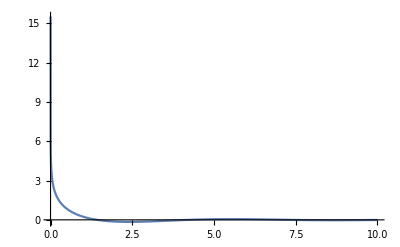

```mathematica
With[{s=1},Plot[-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)],{k,0,10},PlotRange->All]]
```

```mathematica
Integrate[BesselJ[0,l s]l(l^2-k^2)/(l^2+m^2)/(l^2-k^2+m^2),{l,0,∞},Assumptions->k>0&&m>0&& s>0]
```

ConditionalExpression[1/(4 k^2 π)(4 EulerGamma (k^2-m^2) π BesselI[0,√(-k^2+m^2) s]-4 EulerGamma (k^2-m^2) π BesselJ[0,√(k^2-m^2) s]-4 m^2 π BesselK[0,√(-k^2+m^2) s]-k^2 MeijerG[{{1,1,3/2},{}},{{3/2},{}},-(2 ⅈ)/(m s),1/2]-k^2 MeijerG[{{1,1,3/2},{}},{{3/2},{}},(2 ⅈ)/(m s),1/2]+m^2 MeijerG[{{1,1,5/2},{}},{{5/2},{}},-(2 ⅈ)/(m s),1/2]+m^2 MeijerG[{{1,1,5/2},{}},{{5/2},{}},(2 ⅈ)/(m s),1/2]), m>k]

```mathematica
Integrate[BesselJ[0,l s]l(l^2-k^2)/(l^2+m^2)/(l^2-k^2+m^2),{l,k,∞},Assumptions->k>0&&m>0&& s>0]
```

Integrate[(l (-k^2+l^2) BesselJ[0,l s])/((l^2+m^2) (-k^2+l^2+m^2)),{l,k,∞},Assumptions→k>0&&m>0&&s>0]

```mathematica
Integrate[BesselJ[0,l s]l/(l^2+mg2)/Sqrt[((l^2-k2)^2+2(k2+l^2)mg2+mg2^2)],{l,0,∞},Assumptions->k>0&&mg2>0&& s>0]
```

$Aborted

```mathematica
Integrate[1/2/(l2+mg2)/Sqrt[((l2-k2)^2+2(k2+l2)mg2+mg2^2)]l2^n,{l2,0,∞},Assumptions->k2>0&&mg2>0&&n∈Integers]
```

Integrate[l2^n/(2 (l2+mg2) √((-k2+l2)^2+2 (k2+l2) mg2+mg2^2)),{l2,0,∞},Assumptions→k2>0&&mg2>0&&n∈ℤ]

```mathematica
Integrate[l/((l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4)/(l^2+mg^2),{l,0,lUV},Assumptions->k>0&&lUV>k&&mg>0]
```

1/(4 k^2 mg (k^2+4 mg^2))(k (ArcCot[(2 k mg)/(-k^2+lUV^2+mg^2)]+ArcTan[k/(2 mg)-mg/(2 k)])-mg (4 Log[mg]-2 Log[(k^2+mg^2) (lUV^2+mg^2)]+Log[k^4+2 k^2 (-lUV^2+mg^2)+(lUV^2+mg^2)^2]))

```mathematica
Series[1/(4 k^2 mg (k^2+4 mg^2))(k (ArcCot[(2 k mg)/(-k^2+lUV^2+mg^2)]+ArcTan[k/(2 mg)-mg/(2 k)])-mg (4 Log[mg]-2 Log[(k^2+mg^2) (lUV^2+mg^2)]+Log[k^4+2 k^2 (-lUV^2+mg^2)+(lUV^2+mg^2)^2])),{mg,0,1},Assumptions->k>0&&lUV>k&&mg>0]
```

π/(4 k^3 mg)+1/(4 k^4 (k^2-lUV^2))(2 lUV^2+4 k^2 Log[k]-4 lUV^2 Log[k]+4 k^2 Log[lUV]-4 lUV^2 Log[lUV]-k^2 Log[k^4-2 k^2 lUV^2+lUV^4]+lUV^2 Log[k^4-2 k^2 lUV^2+lUV^4]-4 k^2 Log[mg]+4 lUV^2 Log[mg])-(((6 k^2-7 lUV^2) π) mg)/(8 (k^5 (k^2-lUV^2)))+O[mg]^2

```mathematica
Limit[π/(4 k^3 mg)+1/(4 k^4 (k^2-lUV^2))(2 lUV^2+4 k^2 Log[k]-4 lUV^2 Log[k]+4 k^2 Log[lUV]-4 lUV^2 Log[lUV]-k^2 Log[k^4-2 k^2 lUV^2+lUV^4]+lUV^2 Log[k^4-2 k^2 lUV^2+lUV^4]-4 k^2 Log[mg]+4 lUV^2 Log[mg]),lUV->∞,Direction->"FromAbove"]
```

(-2 mg+k π+4 mg Log[k]-4 mg Log[mg])/(4 k^4 mg)

```mathematica
Integrate[ Exp[cp l2/k2]/Sqrt[(l2+k2)^2+2(k2+l2)mg2+mg2^2]/(l2+mg2),{l2,0,k2},Assumptions->k2>0&&mg2>0]
```

1/k2 ⅇ^(-(cp (k2+2 mg2))/k2) (ⅇ^((cp (k2+mg2))/k2) Gamma[0,-(cp mg2)/k2]-(ⅇ^((cp mg2)/k2)+ⅇ^((cp (k2+mg2))/k2)) Gamma[0,-(cp (k2+mg2))/k2]+ⅇ^((cp mg2)/k2) Gamma[0,-(cp (2 k2+mg2))/k2])

```mathematica
(1-η)^2+2(1+η)ϵ+ϵ^2//Expand
```

1+2 ϵ+ϵ^2-2 η+2 ϵ η+η^2

```mathematica
-4 η+(1+ϵ+η)^2
```

-4 η+(1+ϵ+η)^2

```mathematica
Expand[-4 η+(1+ϵ+η)^2]
```

1+2 ϵ+ϵ^2-2 η+2 ϵ η+η^2

```mathematica
Integrate[ Exp[cp η]/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{η,0,1},Assumptions->ϵ>0&&ϵ<1]
```

Integrate[ⅇ^(cp η)/((ϵ+η) √(ϵ^2+(1-η)^2+2 ϵ (1+η))),{η,0,1},Assumptions→ϵ>0&&ϵ<1]

```mathematica
Integrate[1/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{η,0,1},Assumptions->ϵ>0&&ϵ<1]
```

Log[((1+√(1+4 ϵ)) (1+ϵ-√(ϵ (4+ϵ))+√(1+4 ϵ)))/((-1+√(1+4 ϵ)) (-1-ϵ+√(ϵ (4+ϵ))+√(1+4 ϵ)))]/(√(1+4 ϵ))

```mathematica
Series[Log[((1+√(1+4 ϵ)) (1+ϵ-√(ϵ (4+ϵ))+√(1+4 ϵ)))/((-1+√(1+4 ϵ)) (-1-ϵ+√(ϵ (4+ϵ))+√(1+4 ϵ)))]/(√(1+4 ϵ)),{ϵ,0,1}]
```

Log[1/ϵ^(3/2)]-(3 √ϵ)/2+(3-2 Log[1/ϵ^(3/2)]) ϵ+O[ϵ]^(3/2)

```mathematica
Integrate[η/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{η,0,1},Assumptions->ϵ>0&&ϵ<1]
```

-(2 ϵ ArcTanh[(√(1+4 ϵ) (1+ϵ (2+ϵ-√(ϵ (4+ϵ)))))/(1+4 ϵ+6 ϵ^2)])/(√(1+4 ϵ))+Log[2/(-ϵ+√(ϵ (4+ϵ)))]

```mathematica
Series[(2 ϵ ArcTanh[(√(1+4 ϵ) (1+ϵ (2+ϵ-√(ϵ (4+ϵ)))))/(1+4 ϵ+6 ϵ^2)])/(√(1+4 ϵ))+Log[2/(-ϵ+√(ϵ (4+ϵ)))],{ϵ,0,1},Assumptions->ϵ>0]
```

-Log[ϵ]/2+(√ϵ)/2-3/2 Log[ϵ] ϵ-(73 ϵ^(3/2))/48+O[ϵ]^2

```mathematica
l=Integrate[η^2/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{η,0,1},Assumptions->ϵ>0&&ϵ<1]
Series[l,{ϵ,0,1}]
```

-1-ϵ+√(ϵ (4+ϵ))+Log[2]-ϵ Log[4]+(-1+2 ϵ) Log[-ϵ+√(ϵ (4+ϵ))]-(ϵ^2 Log[-1+√(1+4 ϵ)])/(√(1+4 ϵ))+(ϵ^2 Log[1+√(1+4 ϵ)])/(√(1+4 ϵ))+(ϵ^2 Log[1+ϵ-√(ϵ (4+ϵ))+√(1+4 ϵ)])/(√(1+4 ϵ))-(ϵ^2 Log[-1-ϵ+√(ϵ (4+ϵ))+√(1+4 ϵ)])/(√(1+4 ϵ))

1/2 (-2-Log[ϵ])+(5 √ϵ)/2+(-1+2 Log[2]-Log[4]+Log[ϵ]) ϵ+O[ϵ]^(3/2)

```mathematica
Integrate[η^nn/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{η,0,1},Assumptions->ϵ>0&&ϵ<1&&nn∈Integers]
```

Integrate[η^nn/((ϵ+η) √(ϵ^2+(1-η)^2+2 ϵ (1+η))),{η,0,1},Assumptions→ϵ>0&&ϵ<1&&nn∈ℤ]

```mathematica
Integrate[ Exp[cp ηl]/Sqrt[ηl^2+2(2-ηl)ϵ+ϵ^2]/(1-ηl+ϵ),{ηl,0,1},Assumptions->ϵ>0&&ϵ<1]
```

Integrate[ⅇ^(cp ηl)/((1+ϵ-ηl) √(ϵ^2+2 ϵ (2-ηl)+ηl^2)),{ηl,0,1},Assumptions→ϵ>0&&ϵ<1]

```mathematica
Series[Exp[cp η]/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{ϵ,0,1}]
```

ⅇ^(cp η)/(√((-1+η)^2) η)-(ⅇ^(cp η) (1-η+2 η^2) ϵ)/(((-1+η)^2)^(3/2) η^2)+O[ϵ]^2

```mathematica
Series[Exp[cp η]/Sqrt[(1-η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{ϵ,0,1}]
```

```mathematica
Series[ Exp[ⅈ ksh((1+η+ϵ)Cϕ-ⅈ Sϕ Sqrt[(1+η+ϵ)^2-4η])]/Sqrt[(1+η+ϵ)^2-4η]/(η+ϵ),{ϵ,0,1}]
```

(ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η)))/(√((-1+η)^2) η)+1/(((-1+η)^2)^(3/2) η^2)ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η)) (-1+η+ⅈ Cϕ ksh η+ksh Sϕ √((-1+η)^2) η-2 η^2-2 ⅈ Cϕ ksh η^2+ksh Sϕ √((-1+η)^2) η^2+ⅈ Cϕ ksh η^3) ϵ+O[ϵ]^2

```mathematica
Series[ Exp[ⅈ ksh((1+η+ϵ)Cϕ-ⅈ Sϕ Sqrt[(1+η+ϵ)^2-4η])],{ϵ,0,1}]
```

ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η))+ⅈ ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η)) ksh (Cϕ-(ⅈ Sϕ (1+η))/(√((-1+η)^2))) ϵ+O[ϵ]^2

```mathematica
dϵ1=ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η))+ⅈ ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η)) ksh (Cϕ-(ⅈ Sϕ (1+η))/(√((-1+η)^2))) ϵ;
nϵ1=ⅇ^(cp η)/(√((-1+η)^2) η)-(ⅇ^(cp η) (1-η+2 η^2) ϵ)/(((-1+η)^2)^(3/2) η^2);
```

```mathematica
Series[Sqrt[(1+η+ϵ)^2-4η](η+ϵ),{ϵ,0,1}]
```

√((-1+η)^2) η+((1-η+2 η^2) ϵ)/(√((-1+η)^2))+O[ϵ]^2

```mathematica
Series[ Exp[ⅈ ksh((1+η+ϵ)Cϕ-ⅈ Sϕ Sqrt[(1+η+ϵ)^2-4η])]/Sqrt[(1+η+ϵ)^2-4η]/(η+ϵ),{η,0,1}]
```

(ⅇ^(ⅈ ksh (Cϕ+Cϕ ϵ-ⅈ Sϕ √((1+ϵ)^2))))/(ϵ √((1+ϵ)^2))+1/(ϵ^2 ((1+ϵ)^2)^(3/2))ⅇ^(ⅈ ksh (Cϕ+Cϕ ϵ-ⅈ Sϕ √((1+ϵ)^2))) (-1-ϵ+ⅈ Cϕ ksh ϵ-2 ϵ^2+2 ⅈ Cϕ ksh ϵ^2+ⅈ Cϕ ksh ϵ^3-ksh Sϕ ϵ √((1+ϵ)^2)+ksh Sϕ ϵ^2 √((1+ϵ)^2)) η+O[η]^2

```mathematica
Integrate[1/(A-B Cos[x]),{x,0,2π},Assumptions->A>B>0]
```

(2 π)/(√(A^2-B^2))

```mathematica
Integrate[ Sin[x]/(A-B Cos[x-a]),{x,0,2π},Assumptions->A>B>0&& a>0]
```

ConditionalExpression[Piecewise[{{(2 ⅈ ⅇ^(ⅈ a) π)/B, Abs[A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1&&Abs[A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {(ⅈ ⅇ^(-ⅈ a) (-1+ⅇ^(2 ⅈ a)) (2 A^2 ⅇ^(ⅈ a)-B^2 ⅇ^(ⅈ a)+2 A √(A^2-B^2) √(ⅇ^(2 ⅈ a))) π)/(B (A^2 ⅇ^(ⅈ a)-B^2 ⅇ^(ⅈ a)+A √(A^2-B^2) √(ⅇ^(2 ⅈ a)))), Abs[A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {(ⅈ ⅇ^(-ⅈ a) (-1+ⅇ^(2 ⅈ a)) (-2 A^2 ⅇ^(ⅈ a)+B^2 ⅇ^(ⅈ a)+2 A √(A^2-B^2) √(ⅇ^(2 ⅈ a))) π)/(B (-A^2 ⅇ^(ⅈ a)+B^2 ⅇ^(ⅈ a)+A √(A^2-B^2) √(ⅇ^(2 ⅈ a)))), Abs[A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {-(2 ⅈ ⅇ^(-ⅈ a) π)/B, True}}], ]

```mathematica
Integrate[  Cos[2x]Sin[x]/(A-B Cos[x]),{x,0,2π},Assumptions->A>B>0]
```

0

```mathematica
Integrate[Sin[x]/(A-B Cos[x-a]),{x,0,2π},Assumptions->A>B>0&& a>0&& a<2π]
```

ConditionalExpression[Piecewise[{{(2 ⅈ ⅇ^(ⅈ a) π)/B, Abs[A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1&&Abs[A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {(ⅈ ⅇ^(-ⅈ a) (-1+ⅇ^(2 ⅈ a)) (2 A^2 ⅇ^(ⅈ a)-B^2 ⅇ^(ⅈ a)+2 A √(A^2-B^2) √(ⅇ^(2 ⅈ a))) π)/(B (A^2 ⅇ^(ⅈ a)-B^2 ⅇ^(ⅈ a)+A √(A^2-B^2) √(ⅇ^(2 ⅈ a)))), Abs[A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {(ⅈ ⅇ^(-ⅈ a) (-1+ⅇ^(2 ⅈ a)) (-2 A^2 ⅇ^(ⅈ a)+B^2 ⅇ^(ⅈ a)+2 A √(A^2-B^2) √(ⅇ^(2 ⅈ a))) π)/(B (-A^2 ⅇ^(ⅈ a)+B^2 ⅇ^(ⅈ a)+A √(A^2-B^2) √(ⅇ^(2 ⅈ a)))), Abs[A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {-(2 ⅈ ⅇ^(-ⅈ a) π)/B, True}}], ]

```mathematica
Integrate[Sin[x]/(A-B Cos[x]),{x,-ϕ,2π-ϕ},Assumptions->A>B&&B>0&& a>0&& a<2π]
```

$Aborted

```mathematica
Integrate[ Cos[2x]Sin[x]/(A-B Cos[x-a]),{x,0,2π},Assumptions->A>B>0&& a>0]
```

ConditionalExpression[Piecewise[{{-(ⅈ ⅇ^(ⅈ a) (-4 A^2 ⅇ^(2 ⅈ a)+B^2 (1+ⅇ^(2 ⅈ a))) π)/B^3, Abs[A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1&&Abs[A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {1/(2 B^3)ⅈ ⅇ^(-3 ⅈ a) (-8 A^2+2 B^2 (1+ⅇ^(2 ⅈ a))+(ⅇ^(4 ⅈ a) (-B^2 (1+ⅇ^(2 ⅈ a))+2 A ⅇ^(ⅈ a) (A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))) (B^4 (1+ⅇ^(4 ⅈ a))+8 A^3 ⅇ^(3 ⅈ a) (A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))-4 A B^2 ⅇ^(3 ⅈ a) (2 A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))))/(√(A^2-B^2) √(ⅇ^(2 ⅈ a)) (A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))^3)) π, Abs[A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {1/(2 B^3)ⅈ ⅇ^(-3 ⅈ a) (-8 A^2+2 B^2 (1+ⅇ^(2 ⅈ a))-(ⅇ^(4 ⅈ a) (B^4 (1+ⅇ^(4 ⅈ a))+8 A^3 ⅇ^(3 ⅈ a) (A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a)))+4 A B^2 ⅇ^(3 ⅈ a) (-2 A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))) (B^2 (1+ⅇ^(2 ⅈ a))+2 A ⅇ^(ⅈ a) (-A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))))/(√(A^2-B^2) √(ⅇ^(2 ⅈ a)) (-A ⅇ^(ⅈ a)+√(A^2-B^2) √(ⅇ^(2 ⅈ a)))^3)) π, Abs[A ⅇ^(ⅈ a)-√(A^2-B^2) √(ⅇ^(2 ⅈ a))]/B<1}, {(ⅈ ⅇ^(-3 ⅈ a) (-4 A^2+B^2 (1+ⅇ^(2 ⅈ a))) π)/B^3, True}}], ]

```mathematica
Integrate[1/(A-B Cos[x]+Cc Sin[x]),{x,0,2π},Assumptions->A>B>0&& Cc>0]
```

```mathematica
Integrate[Exp[ⅈ a Cos[x]]/(A-B Cos[x]),{x,0,2π},Assumptions->A>B>0&& a>0]
```

$Aborted

```mathematica
ParallelTable[{n,Integrate[ Cos[n x]/(A-B Cos[x]),{x,0,2π},Assumptions->A>B>0&& a>0]},{n,0,4}]
```

{{0,(2 π)/(√(A^2-B^2))},{1,(2 (-1+A/(√(A^2-B^2))) π)/B},{2,-(2 B^2 π)/(-2 A^3+2 A B^2-2 A^2 √((A-B) (A+B))+B^2 √((A-B) (A+B)))},{3,(2 (4 A^4-5 A^2 B^2+B^4-4 A^3 √((A-B) (A+B))+3 A B^2 √((A-B) (A+B))) π)/(B^3 (-A+B) (A+B))},{4,1/((A-B) B^4 (A+B))2 (-8 A^5+12 A^3 B^2-4 A B^4+8 A^4 √((A-B) (A+B))-8 A^2 B^2 √((A-B) (A+B))+B^4 √((A-B) (A+B))) π}}

```mathematica
Integrate[ Cos[n x]/(A-B Cos[x]),{x,0,2π},Assumptions->A>B>0&& n∈Integers]
```

$Aborted

```mathematica
Integrate[BesselJ[0,l s]l /Sqrt[(l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4]/(l^2+mg^2),{l,0,∞},Assumptions->k>0&&mg>0 && s>0]
```

Integrate[(l BesselJ[0,l s])/((l^2+mg^2) √((-k^2+l^2)^2+2 (k^2+l^2) mg^2+mg^4)),{l,0,∞},Assumptions→k>0&&mg>0&&s>0]

```mathematica
Series[a/(a-Exp[ⅈ x]b),{x,0,3}]
```

a/(a-b)+(ⅈ a b x)/(a-b)^2-((a (a b+b^2)) x^2)/(2 (a-b)^3)-(ⅈ a (a^2 b+4 a b^2+b^3) x^3)/(6 (a-b)^4)+O[x]^4

```mathematica
l=Integrate[Cos[n x]Cos[m x],{x,0,2π},Assumptions->n∈ Integers && m∈ Integers]
ls=Simplify[l,Assumptions->n∈ Integers && m∈ Integers]
lslim=Limit[l,n->m]
lslim0=Limit[lslim,m->0]
```

(m Cos[2 n π] Sin[2 m π]-n Cos[2 m π] Sin[2 n π])/(m^2-n^2)

0

π+Sin[4 m π]/(4 m)

2 π

```mathematica
l=Integrate[Sin[n x]Cos[m x],{x,0,2π},Assumptions->n∈ Integers && m∈ Integers]
ls=Simplify[l,Assumptions->n∈ Integers && m∈ Integers]
lslim=Limit[l,n->m]
lslim0=Limit[lslim,m->0]
```

(-n+n Cos[2 m π] Cos[2 n π]+m Sin[2 m π] Sin[2 n π])/(m^2-n^2)

0

Sin[2 m π]^2/(2 m)

0

```mathematica
l=Integrate[Sin[n x]Sin[m x],{x,0,2π},Assumptions->n∈ Integers && m∈ Integers]
ls=Simplify[l,Assumptions->n∈ Integers && m∈ Integers]
lslim=Limit[l,n->m]
lslim0=Limit[lslim,m->0]
```

(n Cos[2 n π] Sin[2 m π]-m Cos[2 m π] Sin[2 n π])/(m^2-n^2)

0

π-Sin[4 m π]/(4 m)

0

```mathematica
Limit[(m Cos[2 n π] Sin[2 m π]-n Cos[2 m π] Sin[2 n π])/(m^2-n^2),n->m]
```

π+Sin[4 m π]/(4 m)

```mathematica
Integrate[Cos[n x]Cos[n x],{x,0,2π},Assumptions->n∈ Integers ]
```

π+Sin[4 n π]/(4 n)

```mathematica
l=Integrate[Sin[n x]Cos[m x],{x,0,2π},Assumptions->n∈ Integers && m∈ Integers]
```

```mathematica
Simplify[(-n+n Cos[2 m π] Cos[2 n π]+m Sin[2 m π] Sin[2 n π])/(m^2-n^2),Assumptions->n∈ Integers && m∈ Integers]
```

0

```mathematica
Integrate[1/(A-B Cos[x+a]),{x,0,2π},Assumptions->A>B>0&& a>0]
```

ConditionalExpression[Piecewise[{{0, !(Abs[A ⅇ^(-ⅈ a)-(√(A^2-B^2))/(√(ⅇ^(2 ⅈ a)))]/B<1⊻Abs[A ⅇ^(-ⅈ a)+(√(A^2-B^2))/(√(ⅇ^(2 ⅈ a)))]/B<1)}, {(2 ⅇ^(ⅈ a) π)/(√(A^2-B^2) √(ⅇ^(2 ⅈ a))), Abs[A ⅇ^(-ⅈ a)-(√(A^2-B^2))/(√(ⅇ^(2 ⅈ a)))]/B<1}, {-(2 ⅇ^(ⅈ a) π)/(√(A^2-B^2) √(ⅇ^(2 ⅈ a))), True}}], ]

```mathematica
Integrate[1/(A-B Cos[x-a]),{x,0,2π},Assumptions->A>B>0&& a>0]
```

```mathematica
Integrate[Exp[ⅈ x Cos[x]]/(A-B Cos[x-a]),{x,0,2π},Assumptions->A>B>0&& a>0]
```

```mathematica
Integrate[dϵ1/nϵ1,{η,0,1}]
```

ConditionalExpression[-1/(ⅈ cp+ksh (Cϕ+ⅈ Sϕ))^3 ⅇ^(ksh (ⅈ Cϕ+Sϕ)) (-Cϕ^3 ksh^3 ϵ^2 (1+4 ϵ)+cp^2 ϵ (-ⅈ+(-4 ⅈ+Cϕ ksh+5 ⅈ ksh Sϕ) ϵ+4 ksh (Cϕ+ⅈ Sϕ) ϵ^2)-ⅈ Cϕ^2 ksh^2 ϵ (-2+(-2+7 ksh Sϕ) ϵ+12 ksh Sϕ ϵ^2)-ⅈ cp (-1+(2-3 ⅈ Cϕ ksh+ksh Sϕ) ϵ+2 ksh (Cϕ+ⅈ Sϕ) (-3 ⅈ+Cϕ ksh+5 ⅈ ksh Sϕ) ϵ^2+8 ksh^2 (Cϕ+ⅈ Sϕ)^2 ϵ^3)+ⅈ (-2+ksh Sϕ-2 ksh^2 Sϕ^2 ϵ^2+ksh^3 Sϕ^3 ϵ^2 (5+4 ϵ))+Cϕ ksh (1-2 ksh Sϕ ϵ (1+2 ϵ)+ksh^2 Sϕ^2 ϵ^2 (11+12 ϵ)))+1/(cp+ksh (-ⅈ Cϕ+Sϕ))^3 ⅇ^(-cp+2 ⅈ Cϕ ksh) (2+ksh Sϕ-2 ksh^3 Sϕ^3 ϵ+2 ksh^2 Sϕ^2 ϵ^2-7 ksh^3 Sϕ^3 ϵ^2-4 ksh^3 Sϕ^3 ϵ^3-ⅈ Cϕ^3 ksh^3 ϵ^2 (3+4 ϵ)+cp (1+(2+3 ksh Sϕ-4 ksh^2 Sϕ^2+ⅈ Cϕ ksh (-5+4 ksh Sϕ)) ϵ+2 ksh (Cϕ+ⅈ Sϕ) (-3 ⅈ+3 Cϕ ksh+7 ⅈ ksh Sϕ) ϵ^2+8 ksh^2 (Cϕ+ⅈ Sϕ)^2 ϵ^3)+cp^2 ϵ (3+4 ϵ+ⅈ Cϕ ksh ϵ (3+4 ϵ)-ksh Sϕ (2+7 ϵ+4 ϵ^2))+Cϕ^2 ksh^2 ϵ (-2 (1+ϵ)+ksh Sϕ (2+13 ϵ+12 ϵ^2))+ⅈ Cϕ ksh (-1-2 ksh Sϕ ϵ (1+2 ϵ)+ksh^2 Sϕ^2 ϵ (4+17 ϵ+12 ϵ^2)))-ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-ⅈ Cϕ ksh ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+5 ksh Sϕ ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ⅈ Cϕ ksh ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ksh Sϕ ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+ⅈ Cϕ ksh ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-5 ksh Sϕ ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ⅈ Cϕ ksh ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ksh Sϕ ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1])/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+2 ϵ RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+3 ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+2 ⅈ Cϕ ksh ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ksh Sϕ ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+3 ⅈ Cϕ ksh ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-7 ksh Sϕ ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ⅈ Cϕ ksh ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ksh Sϕ ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-2 ϵ RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-3 ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-2 ⅈ Cϕ ksh ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ksh Sϕ ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-3 ⅈ Cϕ ksh ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+7 ksh Sϕ ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-4 ⅈ Cϕ ksh ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+4 ksh Sϕ ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-2 ϵ RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-8 ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-2 ⅈ Cϕ ksh ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+8 ksh Sϕ ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-8 ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-8 ⅈ Cϕ ksh ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+16 ksh Sϕ ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-8 ⅈ Cϕ ksh ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+8 ksh Sϕ ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[-((cp-ⅈ Cϕ ksh+ksh Sϕ) (1-#1))] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+2 ϵ RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+8 ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+2 ⅈ Cϕ ksh ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-8 ksh Sϕ ϵ^2 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+8 ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+8 ⅈ Cϕ ksh ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-16 ksh Sϕ ϵ^3 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]+8 ⅈ Cϕ ksh ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&]-8 ksh Sϕ ϵ^4 RootSum[ϵ-#1-ϵ #1+2 #1^2+2 ϵ #1^2-#1^3&,(ⅇ^(ⅈ Cϕ ksh+ksh Sϕ-cp #1+ⅈ Cϕ ksh #1-ksh Sϕ #1) ExpIntegralEi[(cp-ⅈ Cϕ ksh+ksh Sϕ) #1] #1^2)/(1+ϵ-4 #1-4 ϵ #1+3 #1^2)&], ]

```mathematica
Integrate[(ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η)))/(√((-1+η)^2) η),{η,0,1}]
```

Integrate::idiv: Integral of -ⅇ^(ksh (Sϕ-Sϕ η+ⅈ Cϕ (1+η)))/((-1+η) η) does not converge on {0,1}.

∫_0^1 (ⅇ^(ⅈ ksh (Cϕ-ⅈ Sϕ √((-1+η)^2)+Cϕ η)))/(√((-1+η)^2) η)ⅆη

```mathematica
l=Integrate[ Exp[cp η]/Sqrt[(1+η+ϵ)^2-4η]/(η+ϵ),{η,0,1},Assumptions->ϵ>0&&ϵ<1]
Series[l,{ϵ,0,1}]
```

Integrate[ⅇ^(cp η)/((ϵ+η) √(-4 η+(1+ϵ+η)^2)),{η,0,1},Assumptions→ϵ>0&&ϵ<1]

Integrate::idiv: Integral of -(ⅇ^(cp η) ((-1+η)^2 η+ϵ (-1+η-2 η^2)))/((-1+η)^3 η^2) does not converge on {0,1}.

Series[Integrate[ⅇ^(cp η)/((ϵ+η) √(-4 η+(1+ϵ+η)^2)),{η,0,1},Assumptions→ϵ>0&&ϵ<1],{ϵ,0,1}]

```mathematica
ⅇ^(-cp (1+2 ϵ)) (ⅇ^(cp (1+ϵ)) Gamma[0,-cp ϵ]-(ⅇ^(cp ϵ)+ⅇ^(cp (1+ϵ))) Gamma[0,-cp (1+ϵ)]+ⅇ^(cp ϵ) Gamma[0,-cp (2+ϵ)])//FullSimplify
```

ⅇ^(-cp (1+2 ϵ)) (-((ⅇ^(cp ϵ)+ⅇ^(cp (1+ϵ))) ExpIntegralE[1,-cp (1+ϵ)])+ⅇ^(cp ϵ) ExpIntegralE[1,-cp (2+ϵ)]+ⅇ^(cp (1+ϵ)) Gamma[0,-cp ϵ])

```mathematica
Integrate[ Exp[cq η]/Sqrt[(1+η)^2+2(1+η)ϵ+ϵ^2]/(η+ϵ),{η,1,∞},Assumptions->ϵ>0]
```

ConditionalExpression[ⅇ^(-cq (1+ϵ)) (ⅇ^cq Gamma[0,-cq (1+ϵ)]-Gamma[0,-cq (2+ϵ)]), Re[cq]<0]

```mathematica
Integrate[l /Sqrt[(l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4]/(l^2+mg^2),{l,0,k},Assumptions->k>0&&mg>0];
```

Log[((k+√(k^2+4 mg^2)) (k^2+k √(k^2+4 mg^2)+mg (mg-√(4 k^2+mg^2))))/((-k+√(k^2+4 mg^2)) (-k^2+k √(k^2+4 mg^2)+mg (-mg+√(4 k^2+mg^2))))]/(2 k √(k^2+4 mg^2))

```mathematica
Integrate[l l^2/Sqrt[(l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4]/(l^2+mg^2),{l,0,k},Assumptions->k>0&&mg>0]
```

1/(2 k √(k^2+4 mg^2))(k √(k^2+4 mg^2) Log[2]+2 k √(k^2+4 mg^2) Log[k]-k √(k^2+4 mg^2) Log[mg (-mg+√(4 k^2+mg^2))]+mg^2 Log[1-k/(√(k^2+4 mg^2))]-mg^2 Log[1+k/(√(k^2+4 mg^2))]-mg^2 Log[1+k/(√(k^2+4 mg^2))+(mg (mg-√(4 k^2+mg^2)))/(k √(k^2+4 mg^2))]+mg^2 Log[1-k/(√(k^2+4 mg^2))+(mg (-mg+√(4 k^2+mg^2)))/(k √(k^2+4 mg^2))])

```mathematica
Integrate[l Exp[cq l^2]/Sqrt[(l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4]/(l^2+mg^2),{l,k,∞},Assumptions->k>0&&mg>0]
```

Integrate[(ⅇ^(cq l^2) l)/((l^2+mg^2) √((-k^2+l^2)^2+2 (k^2+l^2) mg^2+mg^4)),{l,k,∞},Assumptions→k>0&&mg>0]

```mathematica
Integrate[l Exp[cq l^2]/Sqrt[(l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4]/(l^2+mg^2),{l,k,lUV},Assumptions->k>0&&lUV>k&&mg>0]
```

Integrate[(ⅇ^(cq l^2) l)/((l^2+mg^2) √((-k^2+l^2)^2+2 (k^2+l^2) mg^2+mg^4)),{l,k,lUV},Assumptions→k>0&&lUV>k&&mg>0]

```mathematica
Series[l /(l^2+mg^2),{mg,0,2},Assumptions->k>0]
```

1/l-mg^2/l^3+O[mg]^3

```mathematica
Series[1/(l^2+mg^2),{mg,0,2},Assumptions->k>0]
```

1/l^2-mg^2/l^4+O[mg]^3

```mathematica
Series[(a+mg^2)/(b+mg^2),{mg,0,2},Assumptions->k>0]
```

a/b+((-a+b) mg^2)/b^2+O[mg]^3

```mathematica
Series[(l^2+k^2)/(l^2+k^2-2k l Cskl+mg^2),{mg,0,2},Assumptions->k>0]
```

(k^2+l^2)/(k^2-2 Cskl k l+l^2)-((k^2+l^2) mg^2)/((k^2-2 Cskl k l+l^2)^2)+O[mg]^3

```mathematica
Integrate[BesselJ[0,l s]/(l^2+mg^2)l,{l,0,∞},Assumptions->mg>0&& s>0]
```

BesselK[0,mg s]

```mathematica
Integrate[BesselJ[0,l s]/l^3l,{l,0,∞},Assumptions->mg>0&& s>0]
```

Integrate::idiv: Integral of BesselJ[0,l s]/l^2 does not converge on {0,∞}.

Integrate[BesselJ[0,l s]/l^2,{l,0,∞},Assumptions→mg>0&&s>0]

```mathematica
Seires[l /Sqrt[(l^2-k^2)^2+2(k^2+l^2)mg^2+mg^4]/(l^2+mg^2),{l,0,k},Assumptions->k>0&&mg>0]
```

## appr on A and B

```mathematica
FNSAB[1,gA,gB]
```

(2 ((k^2+l^2+mg2)/(2 k l)-√(-1+((k^2+l^2+mg2)^2)/(4 k^2 l^2))) π)/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))

```mathematica
(gA/gB-Sqrt[(gA/gB)^2-1])
```

(k^2+l^2+mg2)/(2 k l)-√(-1+((k^2+l^2+mg2)^2)/(4 k^2 l^2))

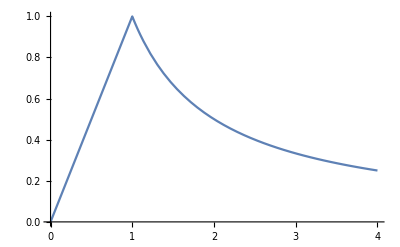

```mathematica
With[{k=1,mg2=0},Plot[(k^2+l^2+mg2)/(2 k l)-√(-1+((k^2+l^2+mg2)^2)/(4 k^2 l^2)),{l,0,4}]]
```

```mathematica
Aeta:=1+η+ϵ^2;
ABeta:=Sqrt[Aeta^2-4η];
```

```mathematica
Series[ABeta,{ϵ,0,2},Assumptions->η>0&&ϵ>0]
```

√(1-2 η+η^2)+((1+η) ϵ^2)/(√((-1+η)^2))+O[ϵ]^3

```mathematica
D[ABeta,{ϵ,1}]
```

(2 ϵ (1+ϵ^2+η))/(√(-4 η+(1+ϵ^2+η)^2))

```mathematica
D[ABeta,{ϵ,2}]
```

-(4 ϵ^2 (1+ϵ^2+η)^2)/((-4 η+(1+ϵ^2+η)^2)^(3/2))+(4 ϵ^2)/(√(-4 η+(1+ϵ^2+η)^2))+(2 (1+ϵ^2+η))/(√(-4 η+(1+ϵ^2+η)^2))

```mathematica
ψEta=Aeta cos+ⅈ ABeta sin;
```

```mathematica
Series[ψEta,{ϵ,0,2},Assumptions->η>0&&ϵ>0]
```

(cos+ⅈ sin √((-1+η)^2)+cos η)+(cos+(ⅈ sin (1+η))/(√((-1+η)^2))) ϵ^2+O[ϵ]^3

```mathematica
Series[Exp[ψEta],{ϵ,0,2},Assumptions->η>0&&ϵ>0]
```

ⅇ^(cos+ⅈ sin √((-1+η)^2)+cos η)+ⅇ^(cos+ⅈ sin √((-1+η)^2)+cos η) (cos+(ⅈ sin (1+η))/(√((-1+η)^2))) ϵ^2+O[ϵ]^3

```mathematica
Series[ Exp[ⅈ ksH ψEta],{ϵ,0,2},Assumptions->η>0&&ϵ>0]
```

ⅇ^(ⅈ ksH (cos+ⅈ sin √((-1+η)^2)+cos η))+ⅈ ⅇ^(ⅈ ksH (cos+ⅈ sin √((-1+η)^2)+cos η)) ksH (cos+(ⅈ sin (1+η))/(√((-1+η)^2))) ϵ^2+O[ϵ]^3

## Div in Gx

```mathematica
gA:=k^2+l^2+mg2;
gB:=2 k l;
```

```mathematica
FNSAB[n_,A_,B_]:=2π/Sqrt[A^2-B^2](A/B-Sqrt[(A/B)^2-1])^n
```

```mathematica
FNSAB[0,gA,gB]
```

(2 π)/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))

```mathematica
FNSAB[1,gA,gB]
```

(2 ((k^2+l^2+mg2)/(2 k l)-√(-1+((k^2+l^2+mg2)^2)/(4 k^2 l^2))) π)/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))

```mathematica
Series[l/(l^2+mg2)BesselJ[1,l s],{mg2,0,2},Assumptions->s>0&& l>0]
```

BesselJ[1,l s]/l-(BesselJ[1,l s] mg2)/l^3+(BesselJ[1,l s] mg2^2)/l^5+O[mg2]^3

```mathematica
With[{n=0},Integrate[l/(l^2+mg2)BesselJ[1,l s],{l,0,∞},Assumptions->s>0&& mg2>0]]
```

1/2 π (-BesselI[1,√mg2 s]+StruveL[-1,√mg2 s])

```mathematica
Integrate[l/(l^2+mg2)BesselJ[0,l s],{l,0,∞},Assumptions->s>0&& mg2>0]
```

BesselK[0,√mg2 s]

```mathematica
Integrate[Exp[-s^2 t]/(t+mg^2),{t,0,∞},Assumptions->s>0&& mg>0]
```

-ⅇ^(mg^2 s^2) ExpIntegralEi[-mg^2 s^2]

```mathematica
Integrate[l/(l^2)BesselJ[0,l s],{l,mg,∞},Assumptions->s>0&& mg>0]
```

-EulerGamma+1/8 mg^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 mg^2 s^2]+Log[2/(mg s)]

```mathematica
Series[-EulerGamma+1/8 mg^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 mg^2 s^2]+Log[2/(mg s)],{mg2,0,2},Assumptions->s>0]
```

-EulerGamma+1/8 mg^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 mg^2 s^2]+Log[2/(mg s)]

```mathematica
Series[BesselK[0,√mg2 s],{mg2,0,2},Assumptions->s>0]
```

1/2 (-2 EulerGamma-Log[mg2]-2 Log[s/2])+1/8 (2 s^2-2 EulerGamma s^2-s^2 Log[mg2]-2 s^2 Log[s/2]) mg2+1/128 (3 s^4-2 EulerGamma s^4-s^4 Log[mg2]-2 s^4 Log[s/2]) mg2^2+O[mg2]^3

```mathematica
Integrate[l/(l^2+mg2)BesselJ[n,l s],{l,0,∞},Assumptions->s>0&& mg2>0&&n∈Integers]
```

ConditionalExpression[-1/2 π BesselI[n,√mg2 s] Csc[(n π)/2]+HypergeometricPFQ[{1},{1-n/2,1+n/2},(mg2 s^2)/4]/n, n>-2]

```mathematica
-1/2 π BesselI[n,√mg2 s] Csc[(n π)/2]+HypergeometricPFQ[{1},{1-n/2,1+n/2},(mg2 s^2)/4]/n//FullSimplify
```

-1/2 π BesselI[n,√mg2 s] Csc[(n π)/2]+HypergeometricPFQ[{1},{1-n/2,1+n/2},(mg2 s^2)/4]/n

```mathematica
∑_(n=1)^∞ (ⅈ^n BesselJ[n,l s] Cos[n x])
```

1/2 (ⅇ^(ⅈ l s Cos[x])-BesselJ[0,l s])

```mathematica
Series[l/(l^2+mg2)BesselJ[n,l s]FNSAB[n,gA,gB],{mg2,0,2},Assumptions->s>0&& l>0]
```

(2^(1-n) ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^n π BesselJ[n,l s])/(l √((-k^2+l^2)^2))+2 l (2^-n ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^n ((-k^2-l^2)/(l^2 ((k^2-l^2)^2)^(3/2))-1/(l^4 √(k^4-2 k^2 l^2+l^4)))+(2^(1-n) ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^(-1+n) (1/(2 k l)-(√(((k^2-l^2)^2)/k^2) (k^2+l^2))/(2 l (-k^2+l^2)^2)) n)/(l^2 √(k^4-2 k^2 l^2+l^4))) π BesselJ[n,l s] mg2+2 l (2^-n ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^n (-(-k^2-l^2)/(l^4 ((k^2-l^2)^2)^(3/2))+1/(l^6 √(k^4-2 k^2 l^2+l^4))+(k^4+4 k^2 l^2+l^4)/(l^2 (k^2-l^2)^4 √((k^2-l^2)^2)))+2^(1-n) ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^(-1+n) (1/(2 k l)-(√(((k^2-l^2)^2)/k^2) (k^2+l^2))/(2 l (-k^2+l^2)^2)) ((-k^2-l^2)/(l^2 ((k^2-l^2)^2)^(3/2))-1/(l^4 √(k^4-2 k^2 l^2+l^4))) n+((2^(1-n) k^2 l √(((-k^2+l^2)^2)/k^2) ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^(-1+n) n)/((-k^2+l^2)^4)+2^(1-n) ((k^2+l^2-k √(((-k^2+l^2)^2)/k^2))/(k l))^(-2+n) (1/(2 k l)-(√(((k^2-l^2)^2)/k^2) (k^2+l^2))/(2 l (-k^2+l^2)^2))^2 (-1+n) n)/(l^2 √(k^4-2 k^2 l^2+l^4))) π BesselJ[n,l s] mg2^2+O[mg2]^3

```mathematica
With[{n=0},Integrate[l/(l^2+mg2)BesselJ[n,l s]FNSAB[n,gA,gB],{l,0,∞},Assumptions->s>0&& mg2>0]]
```

$Aborted

```mathematica
With[{n=1},Integrate[l/(l^2+mg2)BesselJ[n,l s]FNSAB[n,gA,gB],{l,0,∞},Assumptions->s>0&& mg2>0]]
```

```mathematica
Clear[k]
```

```mathematica
gA/k^2
```

(k^2+l^2+mg2)/k^2

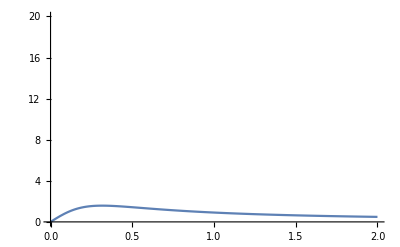

```mathematica
With[{f=l/(l^2+mg2)/.{mg2->.1}},Plot[f,{l,0,2},PlotRange->{Full,{0,20}}]]
```

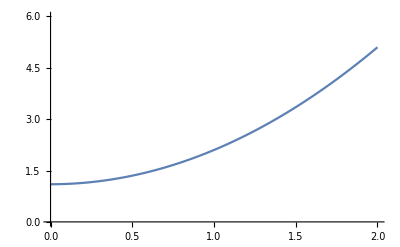

```mathematica
With[{f=gA/.{mg2->.1,k->1}},Plot[f,{l,0,2},PlotRange->{Full,{0,6}}]]
```

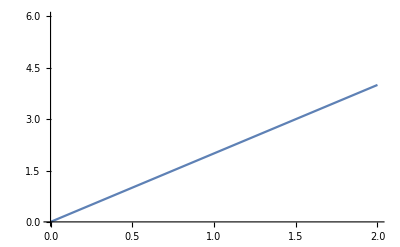

```mathematica
With[{f=gB/.{mg2->.1,k->1}},Plot[f,{l,0,2},PlotRange->{Full,{0,6}}]]
```

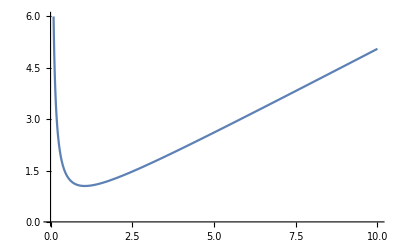

```mathematica
With[{f=gA/gB/.{mg2->.1,k->1}},Plot[f,{l,0,10},PlotRange->{Full,{0,6}}]]
```

```mathematica
With[{f=Sqrt[gA^2-gB^2]/gB/.{mg2->.1,k->1}},Plot[f,{l,0,10},PlotRange->{Full,{0,6}}]]
```

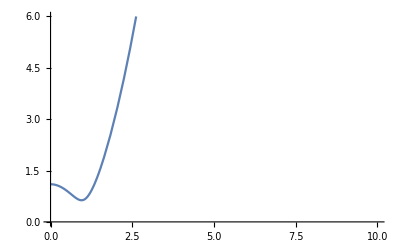

```mathematica
With[{f=Sqrt[gA^2-gB^2]/.{mg2->.1,k->1}},Plot[f,{l,0,10},PlotRange->{Full,{0,6}}]]
```

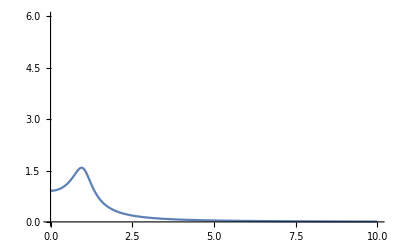

```mathematica
With[{f=1/Sqrt[gA^2-gB^2]/.{mg2->.1,k->1}},Plot[f,{l,0,10},PlotRange->{Full,{0,6}}]]
```

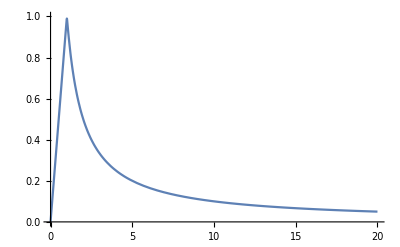

```mathematica
With[{f=(gA-Sqrt[gA^2-gB^2])/gB/.{mg2->.0001,k->1}},Plot[f,{l,0,20},PlotRange->{Full,{0,1}}]]
```

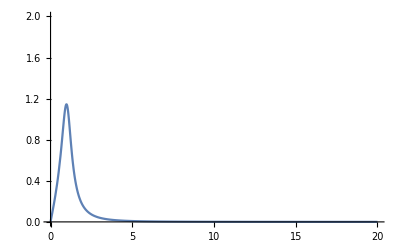

```mathematica
With[{f=((gA-Sqrt[gA^2-gB^2])/gB)/Sqrt[gA^2-gB^2]/.{mg2->.1,k->1}},Plot[f,{l,0,20},PlotRange->{Full,{0,2}}]]
```

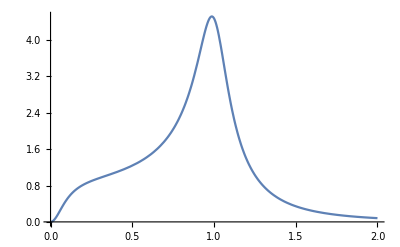

```mathematica
With[{f=l((gA-Sqrt[gA^2-gB^2])/gB)/Sqrt[gA^2-gB^2]/(l^2+mg2)/.{mg2->.01,k->1}},Plot[f,{l,0,2},PlotRange->{Full,All}]]
```

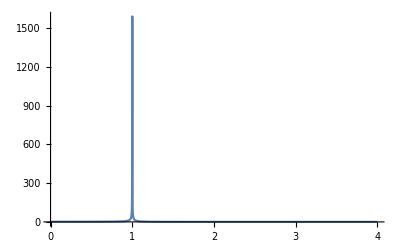

```mathematica
With[{f=l((gA-Sqrt[gA^2-gB^2])/gB)/Sqrt[gA^2-gB^2]/(l^2+mg2)/.{mg2->0,k->1,s->.5}},Plot[f,{l,0,4},PlotRange->{Full,All}]]
```

```mathematica
Limit[l((gA-Sqrt[gA^2-gB^2])/gB)/Sqrt[gA^2-gB^2]/(l^2+mg2),mg2->0]
```

(k^2+l^2-√((k^2-l^2)^2))/(2 k l^2 √((k^2-l^2)^2))

```mathematica
Limit[l^2((gA-Sqrt[gA^2-gB^2])/gB)/Sqrt[gA^2-gB^2]/(l^2+mg2),l->k,Direction->"FromAbove",Assumptions->k>0]
```

(2 k^2+mg2-√(mg2 (4 k^2+mg2)))/(2 (k^2+mg2) √(mg2 (4 k^2+mg2)))

```mathematica
Limit[(2 k^2+mg2-√(mg2 (4 k^2+mg2)))/(2 (k^2+mg2) √(mg2 (4 k^2+mg2))),mg2->0,Assumptions->k>0]
```

Indeterminate

```mathematica
Limit[(k^2+l^2-√((k^2-l^2)^2))/(2 k l^2 √((k^2-l^2)^2)),l->k,Direction->"FromAbove",Assumptions->k>0]
```

∞

```mathematica
Limit[(k^2+l^2-√((k^2-l^2)^2))/(2 k l^2 √((k^2-l^2)^2)),l->k,Direction->"FromBelow",Assumptions->k>0]
```

∞

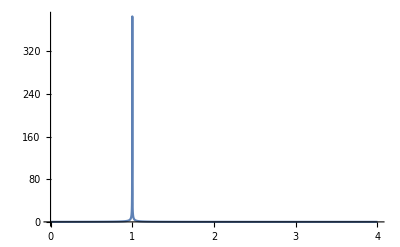

```mathematica
With[{f=BesselJ[1,l s]l((gA-Sqrt[gA^2-gB^2])/gB)/Sqrt[gA^2-gB^2]/(l^2+mg2)/.{mg2->0,k->1,s->.5}},Plot[f,{l,0,4},PlotRange->{Full,All}]]
```

```mathematica
Series[BesselJ[1, l],{l,1,2}]
```

BesselJ[1,1]+(BesselJ[1,1]-BesselJ[2,1]) (l-1)+1/2 (-BesselJ[1,1]+BesselJ[2,1]) (l-1)^2+O[l-1]^3

```mathematica
Series[BesselJ[0, l s]/(k^2-l^2),{l,k,2},Assumptions->s>0&&k>0]
```

-BesselJ[0,k s]/(2 k (l-k))+(BesselJ[0,k s]+2 k s BesselJ[1,k s])/(4 k^2)+((-BesselJ[0,k s]+2 k^2 s^2 BesselJ[0,k s]-4 k s BesselJ[1,k s]) (l-k))/(8 k^3)+1/(48 k^4)(3 BesselJ[0,k s]-10 k^2 s^2 BesselJ[0,k s]+20 k s BesselJ[1,k s]-4 k^3 s^3 BesselJ[1,k s]) (l-k)^2+O[l-k]^3

```mathematica
f=(gA-Sqrt[gA^2-gB^2])/gB;
Solve[D[f,{l,2}]==0,l]
```

$Aborted

```mathematica
D[f,{l,2}]
```

```mathematica
Simplify[((2+((-8 k^2 l+4 l (k^2+l^2+mg2))^2)/(4 (-4 k^2 l^2+(k^2+l^2+mg2)^2)^(3/2))-(-8 k^2+8 l^2+4 (k^2+l^2+mg2))/(2 √(-4 k^2 l^2+(k^2+l^2+mg2)^2)))/l-(2 (2 l-(-8 k^2 l+4 l (k^2+l^2+mg2))/(2 √(-4 k^2 l^2+(k^2+l^2+mg2)^2))))/l^2+(2 (k^2+l^2+mg2-√(-4 k^2 l^2+(k^2+l^2+mg2)^2)))/l^3)/(2 k),Assumptions->mg2>0&& l>0&&k>0]
```

1/(k l^3)(k^2+mg2+(2 l^4 (-k^2+l^2+mg2)^2)/((-4 k^2 l^2+(k^2+l^2+mg2)^2)^(3/2))+(2 l^2 (-k^2+l^2+mg2))/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))-(l^2 (-k^2+3 l^2+mg2))/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))-√(-4 k^2 l^2+(k^2+l^2+mg2)^2))

```mathematica
Solve[1/(k l^3)(k^2+mg2+(2 l^4 (-k^2+l^2+mg2)^2)/((-4 k^2 l^2+(k^2+l^2+mg2)^2)^(3/2))+(2 l^2 (-k^2+l^2+mg2))/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))-(l^2 (-k^2+3 l^2+mg2))/(√(-4 k^2 l^2+(k^2+l^2+mg2)^2))-√(-4 k^2 l^2+(k^2+l^2+mg2)^2))==0,l]
```

$Aborted

```mathematica
Clear[l];
Integrate[BesselJ[0,l s]l/2/(l^2+mg2)(1-(2k^2 -gA)/Sqrt[gA^2-gB^2]),{l,0,∞},Assumptions->mg2>0&& s>0&&k>0]
```

$Aborted

```mathematica
Series[BesselJ[10,x],{x,0,12}]
```

x^10/3715891200-x^12/163499212800+O[x]^13

```mathematica
Series[Sqrt[gA^2-gB^2],{mg2,0,1}]
```

√(k^4-2 k^2 l^2+l^4)+((k^2+l^2) mg2)/(√((k^2-l^2)^2))+O[mg2]^2

```mathematica
Series[Sqrt[gA^2-gB^2](l^2+mg2),{mg2,0,1}]
```

l^2 √((-k^2+l^2)^2)+((k^4-k^2 l^2+2 l^4) mg2)/(√((-k^2+l^2)^2))+O[mg2]^2

```mathematica
Series[Sqrt[gA^2-gB^2]-(2k^2 -gA),{mg2,0,1}]
```

(-k^2+l^2+√((k^2-l^2)^2))+(1+(k^2+l^2)/(√((k^2-l^2)^2))) mg2+O[mg2]^2

```mathematica
Series[1/(l^2+mg2),{mg2,0,2},Assumptions->mg2>0&& k>0&& l>0]//Simplify
```

1/l^2-mg2/l^4+mg2^2/l^6+O[mg2]^3

```mathematica
Integrate[BesselJ[0,l s]l/2 1/l^2,{l,0,∞},Assumptions->mg2>0&& s>0]
```

Integrate::idiv: Integral of BesselJ[0,l s]/(2 l) does not converge on {0,∞}.

Integrate[BesselJ[0,l s]/(2 l),{l,0,∞},Assumptions→mg2>0&&s>0]

```mathematica
Integrate[BesselJ[0,l s]l/2 mg2/l^4,{l,0,∞},Assumptions->mg2>0&& s>0]
```

Integrate::idiv: Integral of (mg2 BesselJ[0,l s])/(2 l^3) does not converge on {0,∞}.

Integrate[(mg2 BesselJ[0,l s])/(2 l^3),{l,0,∞},Assumptions→mg2>0&&s>0]

```mathematica
Integrate[BesselJ[0,l s]l/2(1/l^2-mg2/l^4),{l,0,∞},Assumptions->mg2>0&& s>0]
```

Integrate::idiv: Integral of BesselJ[0,l s]/(2 l)-(mg2 BesselJ[0,l s])/(2 l^3) does not converge on {0,∞}.

Integrate[1/2 l (1/l^2-mg2/l^4) BesselJ[0,l s],{l,0,∞},Assumptions→mg2>0&&s>0]

```mathematica
Integrate[BesselJ[0,l s]/l,{l,k,∞},Assumptions->k>0&& s>0]
```

-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)]

```mathematica
With[{k=1/s},N[-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)]]]
```

0.237097

```mathematica
With[{k=0},N[-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)]]]
```

Power::infy: Infinite expression 1/0 encountered.

∞

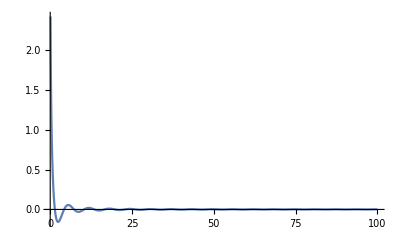

```mathematica
With[{s=1},Plot[-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)],{k,0.1,100},PlotRange->All]]
```

```mathematica
-EulerGamma//N
```

-0.577216

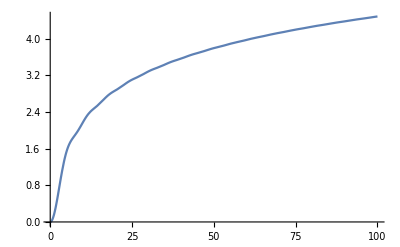

```mathematica
With[{s=1},Plot[1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2],{k,0.1,100},PlotRange->All]]
```

```mathematica
Integrate[BesselJ[0,l s]l/2/(l^2+mg2),{l,0,∞},Assumptions->mg2>0&& s>0]
```

1/2 BesselK[0,√mg2 s]

```mathematica
Series[1/(l^2+mg2)(1-(2k^2 -gA)/Sqrt[gA^2-gB^2]),{mg2,0,2},Assumptions->mg2>0&& k>0&& l>0]//Simplify
```

(1+(-k^2+l^2)/(√((k^2-l^2)^2)))/l^2+((-1-l^2/(√((-k^2+l^2)^2))+(k^2 √((k^2-l^2)^2) (k^2+l^2))/((k^2-l^2)^3)) mg2)/l^4+((-2 k^2 l^2 (k^2-l^2)^2-(k^2-l^2)^4+(k^2-l^2)^3 √((k^2-l^2)^2)-2 l^4 (k^4+2 k^2 l^2)) mg2^2)/(l^6 (k^2-l^2)^3 √((k^2-l^2)^2))+O[mg2]^3

```mathematica
Limit[1/(l^2+mg2)(1-(2k^2 -gA)/Sqrt[gA^2-gB^2]),l->0,Assumptions->mg2>0&& k>0]//Simplify
```

2/(k^2+mg2)

```mathematica
Integrate[l/2/(l^2+mg2)(1-(2k^2 gA)/Sqrt[gA^2-gB^2]),{l,0,lUV},Assumptions->mg2>0&& s>0&&k>0]
```

$Aborted

```mathematica
Series[(1-(2k^2 -gA)/Sqrt[gA^2-gB^2])/(l^2+mg2),{mg2,0,1}]//Simplify
```

(1+(-k^2+l^2)/(√((k^2-l^2)^2)))/l^2+((-1-l^2/(√((-k^2+l^2)^2))+(k^2 √((k^2-l^2)^2) (k^2+l^2))/((k^2-l^2)^3)) mg2)/l^4+O[mg2]^2

```mathematica
Integrate[BesselJ[0,l]/l,l]
```

-1/2 MeijerG[{{},{1}},{{0,0},{0}},l^2/4]

```mathematica
Integrate[BesselJ[0,l s]/l,l]
```

-1/2 MeijerG[{{},{1}},{{0,0},{0}},(l^2 s^2)/4]

```mathematica
Integrate[BesselJ[0,l s]/l,{l,k,∞},Assumptions->k>0&& s>0]
```

-EulerGamma+1/8 k^2 s^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]+Log[2/(k s)]

```mathematica
Integrate[(1+(-k^2+l^2)/(√((k^2-l^2)^2)))/l^2,{l,0,∞},Assumptions->k>0]
```

2/k

```mathematica
Integrate[(1+(-k2+l2)/(√((k2-l2)^2)))/l2,{l2,ϵ,l2UV},Assumptions->k2>0]
```

$Aborted

```mathematica
(1+(-k2+l2)/(k2-l2))/l2//Simplify
```

0

```mathematica
(1+(-k2+l2)/(-k2+l2))/l2//Simplify
```

2/l2

```mathematica
Integrate[2/l2,{l2,k2,l2UV},Assumptions->k2>0]
```

ConditionalExpression[2 Log[l2UV/k2], l2UV≠Re[l2UV]||k2≤Re[l2UV]||Abs[l2UV]^2<k2 Re[l2UV]]

```mathematica
Integrate[2/l2 BesselJ[0,Sqrt[l2]s],{l2,k2,l2UV},Assumptions->k2>0&& s>0]
```

ConditionalExpression[2 (1/4 s^2 (k2 HypergeometricPFQ[{1,1},{2,2,2},-(k2 s^2)/4]-l2UV HypergeometricPFQ[{1,1},{2,2,2},-(l2UV s^2)/4])-Log[k2]+Log[l2UV]), Im[l2UV]≠0||k2≤Re[l2UV]||Re[l2UV]>0]

```mathematica
Integrate[2/l BesselJ[0,l s],{l,k,lUV},Assumptions->k>0&& s>0]
```

ConditionalExpression[1/4 (s^2 (k^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 k^2 s^2]-lUV^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 lUV^2 s^2])-8 Log[k]+4 Log[lUV^2]), Im[lUV]≠0||k≤Re[lUV]||Re[lUV]>0]

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[0,l s],{l,0,∞},Assumptions->k>0&& s>0&&mg2>0]
```

2 BesselK[0,√mg2 s]

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[0,l s],{l,0,k},Assumptions->k>0&& s>0&&mg2>0]
```

Integrate[(2 l BesselJ[0,l s])/(l^2+mg2),{l,0,k},Assumptions→k>0&&s>0&&mg2>0]

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[0,l s],{l,k,∞},Assumptions->k>0&& s>0&&mg2>0]
```

Integrate[(2 l BesselJ[0,l s])/(l^2+mg2),{l,k,∞},Assumptions→k>0&&s>0&&mg2>0]

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[0,l s],{l,0,∞},Assumptions->k>0&& s>0&&mg2>0]
```

2 BesselK[0,√mg2 s]

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[1,l s],{l,0,∞},Assumptions->k>0&& s>0&&mg2>0]
```

π (-BesselI[1,√mg2 s]+StruveL[-1,√mg2 s])

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[2,l s],{l,0,∞},Assumptions->k>0&& s>0&&mg2>0]
```

```mathematica
Table[Integrate[(2 l)/l^2 BesselJ[n,l s],{l,0,∞},Assumptions->k>0&& s>0&&mg2>0],{n,1,5}]
```

{2,1,2/3,1/2,2/5}

```mathematica
4/(mg2 s^2)-2 BesselK[2,√mg2 s]
```

```mathematica
Limit[4/(mg2 s^2)-2 BesselK[2,√mg2 s],mg2->0]
```

1

```mathematica
Integrate[(2 l)/(l^2+mg2)BesselJ[3,l s],{l,0,∞},Assumptions->k>0&& s>0&&mg2>0]
```

2/3+π BesselI[3,√mg2 s]-π StruveL[1,√mg2 s]+(4 π StruveL[2,√mg2 s])/(√mg2 s)

```mathematica
Limit[2/3+π BesselI[3,√mg2 s]-π StruveL[1,√mg2 s]+(4 π StruveL[2,√mg2 s])/(√mg2 s),mg2->0]
```

2/3

```mathematica
Series[BesselJ[0,x],{x,0,2}]
```

1-x^2/4+O[x]^3

```mathematica
Series[BesselJ[1,x],{x,0,2}]
```

x/2+O[x]^3

```mathematica
Integrate[(1+(-k2+l2)/(√((k2-l2)^2)))/l2,l2]
```

∫(1+(-k2+l2)/(√((k2-l2)^2)))/l2 ⅆl2

```mathematica
Integrate[(1+(-k^2+l^2)/(√((k^2-l^2)^2)))/l,{l,0,lUV},Assumptions->k>0]
```

$Aborted

```mathematica
Limit[(1+(-k^2+l^2)/(√((k^2-l^2)^2)))/l^2,l->0,Assumptions->mg2>0&&k>0]//Simplify
```

0

```mathematica
Limit[(1-(2k^2 -gA)/Sqrt[gA^2-gB^2])/(l^2+mg2),l->0,Assumptions->mg2>0&&k>0]//Simplify
```

2/(k^2+mg2)

```mathematica
Limit[(1-(2k^2 -gA)/Sqrt[gA^2-gB^2])/(l^2+mg2),l->∞,Assumptions->mg2>0&&k>0]//Simplify
```

0

```mathematica
Limit[(1-(2k^2 -gA)/Sqrt[gA^2-gB^2])/(l^2+mg2),l->k,Assumptions->mg2>0&&k>0]//Simplify
```

(1+mg2/(√(mg2 (4 k^2+mg2))))/(k^2+mg2)

```mathematica
Integrate[l/2/(l^2+mg2),{l,0,lUV},Assumptions->mg2>0&& s>0&&k>0]
```

ConditionalExpression[1/4 Log[(lUV^2+mg2)/mg2], Re[lUV]≠0||(mg2>1/Im[1/lUV]^2&&lUV≠Re[lUV])]

```mathematica
Integrate[BesselJ[0,l s]l/2/(l^2+mg2) gA/Sqrt[gA^2-gB^2],{l,0,∞},Assumptions->mg2>0&& s>0&&k>0]
```

$Aborted

```mathematica
Integrate[l/2/(l^2+mg2) gA/Sqrt[gA^2-gB^2],{l,0,lUV},Assumptions->mg2>0&& s>0&&k>0]
```

$Aborted

```mathematica
Series[1/2 BesselK[0,√mg2 s],{mg2,0,1},Assumptions-> s>0]
```

1/4 (-2 EulerGamma-Log[mg2]-2 Log[s/2])+1/16 (2 s^2-2 EulerGamma s^2-s^2 Log[mg2]-2 s^2 Log[s/2]) mg2+O[mg2]^2

```mathematica
Series[ BesselK[0,mg s],{mg,0,1},Assumptions-> s>0]
```

(-EulerGamma-Log[mg]-Log[s/2])+O[mg]^2

## Full calculation by Meijian

```mathematica
FNrpdty[θ_]:=-Log[Tan[θ/2]]
```

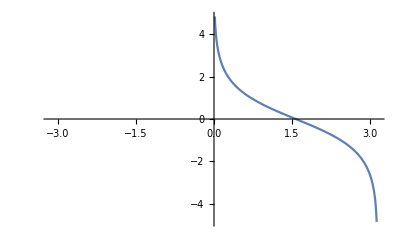

```mathematica
Plot[FNrpdty[x],{x,-π,π}]
```

The goal in this section is to evaluate the hard scattering part, defined as I(k,{b,x1,x2,x3,x4}) below

```mathematica
FNI[{k_,ϕ_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},mIR_:gmIR]:=(2π)^4 (Abs[FNJx[{k,ϕ},{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},mIR]]^2+Abs[FNJy[{k,ϕ},{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},mIR]]^2)
```

```mathematica
With[{k=4,bxy={1,0.1},x1={1.3,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1}},
Manipulate[
Plot[FNI[{k,ϕ},bxy,x1,x2,x3,x4,mIR],{ϕ,0,2π},PlotRange->All],
{mIR,.000001,.1}]
]
```

```mathematica
With[{ϕ=.4,bxy={1,0.1},x1={1.3,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1}},
Manipulate[
Plot[FNI[{k,ϕ},bxy,x1,x2,x3,x4,mIR],{k,mIR,2},PlotRange->All],
{mIR,.000001,.1}]
]
```

```mathematica
With[{k=10,bxy={3,0.33},x1={.5,0.2},x2={-.51,0.1},x3={3.25,4},x4={2.5,0.11}},
Manipulate[
ParametricPlot[FNI[{k,ϕ},bxy,x1,x2,x3,x4,mIR]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotRange->All,PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"],
{mIR,.000001,.1}]
]
```

```mathematica
ParametricPlot[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]
```

### J_{x,y}

```mathematica
FNJxy[{k_,ϕ_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},isx_,mIR_:gmIR]:=Module[{kxy},
kxy=FNpolarToXY[k,ϕ];
(FNGxy[{bx+x1-x3,by+y1-y3},{k,ϕ},isx,mIR]-FNGxy[{bx+x1-x4,by+y1-y4},{k,ϕ},isx,mIR])Exp[-ⅈ kxy.{x1,y1}]/k
-(FNGxy[{bx+x2-x3,by+y2-y3},{k,ϕ},isx,mIR]-FNGxy[{bx+x2-x4,by+y2-y4},{k,ϕ},isx,mIR])Exp[-ⅈ kxy.{x2,y2}]/k]
```

```mathematica
Clear[FNJx,FNJy];
FNJx[{k_,ϕ_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},mIR_:gmIR]:=FNJxy[{k,ϕ},{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},True,mIR];
FNJy[{k_,ϕ_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},mIR_:gmIR]:=FNJxy[{k,ϕ},{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},False,mIR];
```

```mathematica
Clear[bx,by];
With[{ϕ=0.1,bxy={1,0.1},x1={1,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1},isx=False},
Manipulate[
Plot[{Re[FNJxy[{k,ϕ},bxy,x1,x2,x3,x4,isx,mIR]],Im[FNJxy[{k,ϕ},bxy,x1,x2,x3,x4,isx,mIR]]},{k,0,1},PlotRange->All],
{mIR,.000001,.1}]
]
```

```mathematica
With[{ϕ=0.1,bxy={1,0.1},x1={1,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1}},
Manipulate[
Plot[{Re[FNJx[{k,ϕ},bxy,x1,x2,x3,x4,mIR]],Im[FNJx[{k,ϕ},bxy,x1,x2,x3,x4,mIR]]},{k,0,1},PlotRange->All],
{mIR,.000001,.1}]
]
```

```mathematica
With[{k=0.4,bxy={1,0.1},x1={1,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1},isx=False},
Manipulate[
Plot[{Re[FNJxy[{k,ϕ},bxy,x1,x2,x3,x4,isx,mIR]],Im[FNJxy[{k,ϕ},bxy,x1,x2,x3,x4,isx,mIR]]},{ϕ,0,2π},PlotRange->All],
{mIR,.000001,.1}]
]
```

```mathematica
With[{k=0.4,bxy={1,0.1},x1={1,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1},isx=False},
Manipulate[
Plot[{Re[FNJxynum[{k,ϕ},bxy,x1,x2,x3,x4,isx,mIR]],Im[FNJxynum[{k,ϕ},bxy,x1,x2,x3,x4,isx,mIR]]},{ϕ,0,2π},PlotRange->All],
{mIR,.000001,.1}]
]
```

```mathematica
With[{k=0.4,ϕ=.01,bxy={1,0.1},x1={1,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1},isx=False},
FNJxynum[{k,ϕ},bxy,x1,x2,x3,x4,0.1]
]
```

{-3.62816+3.62812 ⅈ,0.025203+0.143493 ⅈ}

```mathematica
With[{k=0.4,ϕ=.01,bxy={1,0.1},x1={1,-0.1},x2={20,0.1},x3={5,0.1},x4={4,0.1},isx=False},
{FNJx[{k,ϕ},bxy,x1,x2,x3,x4,0.1],
FNJy[{k,ϕ},bxy,x1,x2,x3,x4,0.1]}
]
```

{-0.0506803+0.446653 ⅈ,-0.191621+0.397454 ⅈ}

```mathematica
(*
(*From Bin*)
Jnum[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=1/(2π)^2 NIntegrate[Exp[I (bx lx+by ly)] 1/(lx^2+ly^2)({kx,ky}/(kx^2+ky^2)-{kx-lx,ky-ly}/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (lx x3+ ly y3)]-Exp[-I (lx x4+ ly y4)])(Exp[I ((lx-kx) x1+ (ly-ky) y1)]-Exp[I ((lx-kx) x2+ (ly-ky) y2)]),{lx,-Infinity,Infinity},{ly,-Infinity,Infinity}]*)
```

```mathematica
Clear[FNJxynum];
FNJxynum[{k_,ϕ_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},mIR_:gmIR]:=Module[{kx,ky,m2},
{kx,ky}=FNpolarToXY[k,ϕ];
m2=mIR^2;
NIntegrate[
Exp[I (bx lx+by ly)] 1/(lx^2+ly^2+m2)({kx,ky}/(kx^2+ky^2+m2)-{kx-lx,ky-ly}/((kx-lx)^2+(ky-ly)^2+m2)) (Exp[-I (lx x3+ ly y3)]-Exp[-I (lx x4+ ly y4)])(Exp[I ((lx-kx) x1+ (ly-ky) y1)]-Exp[I ((lx-kx) x2+ (ly-ky) y2)]),{lx,-Infinity,Infinity},{ly,-Infinity,Infinity}
]
]
```

### G_{x,y}

```mathematica
FNGxyvF[{sx_,sy_},{k_,ϕ_},isx_]:=FNF1[{sx,sy}]-FNF2[{sx,sy},{k,ϕ}]If[isx,Cos[ϕ],Sin[ϕ]]+FNF3xy[{sx,sy},{k,ϕ},isx]
```

```mathematica
l=Integrate[1/(η+ϵ^2)Exp[c η],{η,0,1},Assumptions->ϵ>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0]
```

ⅇ^(-c ϵ^2) (-ExpIntegralEi[c ϵ^2]+ExpIntegralEi[c (1+ϵ^2)])

```mathematica
l=Integrate[1/(η+ϵ^2)Cos[c η],{η,0,1},Assumptions->ϵ>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0]
```

Cos[c ϵ^2] (-CosIntegral[c ϵ^2]+CosIntegral[c (1+ϵ^2)])+Sin[c ϵ^2] (-SinIntegral[c ϵ^2]+SinIntegral[c (1+ϵ^2)])

(-EulerGamma+CosIntegral[c]-Log[c]-2 Log[ϵ])+O[ϵ]^2

```mathematica
l=Integrate[1/(η+ϵ^2)(Cos[ρ(1+ η)/2]+ⅈ Sin[ρ(1+ η)/2]),{η,0,1},Assumptions->ϵ>0&&ρ>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0]
```

ⅇ^(-1/2 ⅈ (-1+ϵ^2) ρ) (-ExpIntegralEi[1/2 ⅈ ϵ^2 ρ]+ExpIntegralEi[1/2 ⅈ (1+ϵ^2) ρ])

-1/2 ⅇ^((ⅈ ρ)/2) (2 EulerGamma-2 ExpIntegralEi[(ⅈ ρ)/2]+4 Log[ϵ]-Log[-(2 ⅈ)/ρ]+Log[(ⅈ ρ)/2])+O[ϵ]^2

```mathematica
l=Integrate[1/(η+ϵ^2)Exp[ⅈ ρ(1+ η)/2],{η,0,1},Assumptions->ϵ>0&&ρ>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0]
```

ⅇ^(-1/2 ⅈ (-1+ϵ^2) ρ) (-ExpIntegralEi[1/2 ⅈ ϵ^2 ρ]+ExpIntegralEi[1/2 ⅈ (1+ϵ^2) ρ])

-1/2 ⅇ^((ⅈ ρ)/2) (2 EulerGamma-2 ExpIntegralEi[(ⅈ ρ)/2]+4 Log[ϵ]-Log[-(2 ⅈ)/ρ]+Log[(ⅈ ρ)/2])+O[ϵ]^2

```mathematica
l=Integrate[1/(η+ϵ^2)Exp[ⅈ ρ(1+ η)/2-q(1- η)/2],{η,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
```

ⅇ^(-1/2 q (1+ϵ^2)-1/2 ⅈ (-1+ϵ^2) ρ) (-ExpIntegralEi[1/2 ϵ^2 (q+ⅈ ρ)]+ExpIntegralEi[1/2 (1+ϵ^2) (q+ⅈ ρ)])

-1/2 ⅇ^(-q/2+(ⅈ ρ)/2) (2 EulerGamma-2 ExpIntegralEi[1/2 (q+ⅈ ρ)]+4 Log[ϵ]-Log[2/(q+ⅈ ρ)]+Log[1/2 (q+ⅈ ρ)])+O[ϵ]^2

```mathematica
Log[1+ⅈ]-Log[1/(1+ⅈ)]//N
```

0.693147+1.5708 ⅈ

```mathematica
l=Integrate[1/((η-1)+ϵ^2)Exp[ⅈ ρ(1+ η)/2-q(1- η)/2],{η,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
```

ConditionalExpression[ⅇ^(-1/2 ϵ^2 (q+ⅈ ρ)+ⅈ ρ) (ExpIntegralEi[1/2 ϵ^2 (q+ⅈ ρ)]-ExpIntegralEi[1/2 (-1+ϵ^2) (q+ⅈ ρ)]), ϵ>1]

```mathematica
l=Integrate[1/((1-η)+ϵ^2)Exp[ⅈ ρ(1+ η)/2-q(1- η)/2],{η,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
```

ⅇ^(1/2 (q ϵ^2+ⅈ (2+ϵ^2) ρ)) (Gamma[0,1/2 ϵ^2 (q+ⅈ ρ)]-Gamma[0,1/2 (1+ϵ^2) (q+ⅈ ρ)])

-ⅇ^(ⅈ ρ) (EulerGamma+Gamma[0,1/2 (q+ⅈ ρ)]+2 Log[ϵ]+Log[1/2 (q+ⅈ ρ)])+O[ϵ]^2

```mathematica
l=Integrate[(1-η)/((1-η)^2+(1+η)ϵ^2)Exp[ⅈ ρ(1+ η)/2-q(1- η)/2],{η,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
```

1/(2 √(-8+ϵ^2))ⅇ^(-1/4 q ϵ (ϵ+√(-8+ϵ^2))-1/4 ⅈ (-4+ϵ^2+ϵ √(-8+ϵ^2)) ρ) (-ⅇ^(1/2 ϵ √(-8+ϵ^2) (q+ⅈ ρ)) (-ϵ+√(-8+ϵ^2)) ExpIntegralEi[-1/4 ϵ (-ϵ+√(-8+ϵ^2)) (q+ⅈ ρ)]-(ϵ+√(-8+ϵ^2)) ExpIntegralEi[1/4 ϵ (ϵ+√(-8+ϵ^2)) (q+ⅈ ρ)]-ⅇ^(1/2 ϵ √(-8+ϵ^2) (q+ⅈ ρ)) ϵ ExpIntegralEi[1/4 (-2+ϵ^2-ϵ √(-8+ϵ^2)) (q+ⅈ ρ)]+ⅇ^(1/2 ϵ √(-8+ϵ^2) (q+ⅈ ρ)) √(-8+ϵ^2) ExpIntegralEi[1/4 (-2+ϵ^2-ϵ √(-8+ϵ^2)) (q+ⅈ ρ)]+ϵ ExpIntegralEi[1/4 (-2+ϵ^2+ϵ √(-8+ϵ^2)) (q+ⅈ ρ)]+√(-8+ϵ^2) ExpIntegralEi[1/4 (-2+ϵ^2+ϵ √(-8+ϵ^2)) (q+ⅈ ρ)])

Floor[Arg[(-2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2)) (q+ⅈ ρ)]/(2 π)] (-1/4 ⅇ^(ⅈ ρ) Log[32/(16 ⅈ √2 q-16 √2 ρ)]+(ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[32/(16 ⅈ √2 q-16 √2 ρ)] ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(-2 √2-ⅈ ϵ-√(8-ϵ^2))/((-ϵ+ⅈ √(8-ϵ^2)) (q+ⅈ ρ))]/(2 π)] (1/4 ⅇ^(ⅈ ρ) Log[32/(16 ⅈ √2 q-16 √2 ρ)]-((ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[32/(16 ⅈ √2 q-16 √2 ρ)]) ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(-2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2)) (q+ⅈ ρ)]/(2 π)] (-1/4 ⅇ^(ⅈ ρ) Log[1/32 (16 ⅈ √2 q-16 √2 ρ)]+(ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[1/32 (16 ⅈ √2 q-16 √2 ρ)] ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(-2 √2-ⅈ ϵ-√(8-ϵ^2))/((-ϵ+ⅈ √(8-ϵ^2)) (q+ⅈ ρ))]/(2 π)] (1/4 ⅇ^(ⅈ ρ) Log[1/32 (16 ⅈ √2 q-16 √2 ρ)]-((ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[1/32 (16 ⅈ √2 q-16 √2 ρ)]) ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2)) (q+ⅈ ρ)]/(2 π)] (-1/4 ⅇ^(ⅈ ρ) Log[32/(-16 ⅈ √2 q+16 √2 ρ)]-((ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[32/(-16 ⅈ √2 q+16 √2 ρ)]) ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(2 √2-ⅈ ϵ+√(8-ϵ^2))/((ϵ+ⅈ √(8-ϵ^2)) (q+ⅈ ρ))]/(2 π)] (1/4 ⅇ^(ⅈ ρ) Log[32/(-16 ⅈ √2 q+16 √2 ρ)]+(ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[32/(-16 ⅈ √2 q+16 √2 ρ)] ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2)) (q+ⅈ ρ)]/(2 π)] (-1/4 ⅇ^(ⅈ ρ) Log[1/32 (-16 ⅈ √2 q+16 √2 ρ)]-((ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[1/32 (-16 ⅈ √2 q+16 √2 ρ)]) ϵ)/(8 √2)+O[ϵ]^2)+Floor[Arg[(2 √2-ⅈ ϵ+√(8-ϵ^2))/((ϵ+ⅈ √(8-ϵ^2)) (q+ⅈ ρ))]/(2 π)] (1/4 ⅇ^(ⅈ ρ) Log[1/32 (-16 ⅈ √2 q+16 √2 ρ)]+(ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) Log[1/32 (-16 ⅈ √2 q+16 √2 ρ)] ϵ)/(8 √2)+O[ϵ]^2)+(-1/4 ⅇ^(ⅈ ρ) (4 EulerGamma-4 ExpIntegralEi[1/2 (-q-ⅈ ρ)]+4 Log[ϵ]-Log[32/(16 ⅈ √2 q-16 √2 ρ)]+Log[1/32 (16 ⅈ √2 q-16 √2 ρ)]-Log[32/(-16 ⅈ √2 q+16 √2 ρ)]+Log[1/32 (-16 ⅈ √2 q+16 √2 ρ)])-1/(8 √2)(ⅇ^(ⅈ ρ) (-ⅈ-2 ⅈ q+2 ρ) (Log[32/(16 ⅈ √2 q-16 √2 ρ)]-Log[1/32 (16 ⅈ √2 q-16 √2 ρ)]-Log[32/(-16 ⅈ √2 q+16 √2 ρ)]+Log[1/32 (-16 ⅈ √2 q+16 √2 ρ)])) ϵ+O[ϵ]^2)

```mathematica
l=Integrate[1/(η+ϵ^2)Exp[ⅈ ρ(1+ η)/2-q( η-1)/2],{η,1,∞},Assumptions->ϵ>0&&ρ>0&&q>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0&&ρ>0&&q>0]
```

ⅇ^(1/2 (q (1+ϵ^2)-ⅈ (-1+ϵ^2) ρ)) Gamma[0,1/2 (1+ϵ^2) (q-ⅈ ρ)]

ⅇ^(1/2 (q+ⅈ ρ)) Gamma[0,1/2 (q-ⅈ ρ)]+O[ϵ]^2

```mathematica
ⅇ^(1/2 (q+ⅈ ρ)) Gamma[0,1/2 (q-ⅈ ρ)]+1/2 ⅇ^(-q/2+(ⅈ ρ)/2) (2 EulerGamma-2 ExpIntegralEi[1/2 (q+ⅈ ρ)]+4 Log[ϵ]-Log[2/(q+ⅈ ρ)]+Log[1/2 (q+ⅈ ρ)])//FullSimplify
```

1/2 ⅇ^(-q/2+(ⅈ ρ)/2) (2 EulerGamma-2 ExpIntegralEi[1/2 (q+ⅈ ρ)]+2 ⅇ^q Gamma[0,1/2 (q-ⅈ ρ)]+4 Log[ϵ]-Log[4/(q+ⅈ ρ)]+Log[q+ⅈ ρ])

```mathematica
ExpIntegralEi[1/2 (1+ⅈ 1)]//N
```

0.713943+1.42405 ⅈ

```mathematica
l=Integrate[1/(η+ϵ^2)Sin[c η],{η,0,1},Assumptions->ϵ>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0]
```

(CosIntegral[c ϵ^2]-CosIntegral[c (1+ϵ^2)]) Sin[c ϵ^2]+Cos[c ϵ^2] (-SinIntegral[c ϵ^2]+SinIntegral[c (1+ϵ^2)])

SinIntegral[c]+O[ϵ]^2

```mathematica
l=Integrate[1/(η+ϵ^2)Exp[c η],{η,1,∞},Assumptions->ϵ>0]
Series[l,{ϵ,0,1},Assumptions->ϵ>0]
```

ConditionalExpression[ⅇ^(-c ϵ^2) Gamma[0,-c (1+ϵ^2)], Re[c]<0]

ConditionalExpression[Gamma[0,-c]+O[ϵ]^2, Re[c]<0]

1/2 (-2 EulerGamma+2 ExpIntegralEi[ⅈ c]+Log[-ⅈ/c]-Log[ⅈ c]-4 Log[ϵ])+O[ϵ]^2

```mathematica
Integrate[-1/(η+ϵ^2)/((η-1)^2+(1+η)ϵ^2)Exp[c η],{η,0,1},Assumptions->ϵ>0]
```

ConditionalExpression[-1/(2 √(-8+ϵ^2) (ϵ+3 ϵ^3))ⅇ^(-1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))) (-2 ⅇ^(1/2 c (-2-ϵ^2+ϵ √(-8+ϵ^2))) ϵ √(-8+ϵ^2) ExpIntegralEi[c ϵ^2]+2 ⅇ^(1/2 c (-2-ϵ^2+ϵ √(-8+ϵ^2))) ϵ √(-8+ϵ^2) ExpIntegralEi[c (1+ϵ^2)]+2 ⅇ^(c ϵ √(-8+ϵ^2)) ExpIntegralEi[1/2 c ϵ (ϵ-√(-8+ϵ^2))]+ⅇ^(c ϵ √(-8+ϵ^2)) ϵ^2 ExpIntegralEi[1/2 c ϵ (ϵ-√(-8+ϵ^2))]-ⅇ^(c ϵ √(-8+ϵ^2)) ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c ϵ (ϵ-√(-8+ϵ^2))]-2 ExpIntegralEi[1/2 c ϵ (ϵ+√(-8+ϵ^2))]-ϵ^2 ExpIntegralEi[1/2 c ϵ (ϵ+√(-8+ϵ^2))]-ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c ϵ (ϵ+√(-8+ϵ^2))]-2 ⅇ^(c ϵ √(-8+ϵ^2)) ExpIntegralEi[1/2 c (-2+ϵ^2-ϵ √(-8+ϵ^2))]-ⅇ^(c ϵ √(-8+ϵ^2)) ϵ^2 ExpIntegralEi[1/2 c (-2+ϵ^2-ϵ √(-8+ϵ^2))]+ⅇ^(c ϵ √(-8+ϵ^2)) ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c (-2+ϵ^2-ϵ √(-8+ϵ^2))]+2 ExpIntegralEi[1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))]+ϵ^2 ExpIntegralEi[1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))]+ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))]), ]

```mathematica
Series[-1/(2 √(-8+ϵ^2) (ϵ+3 ϵ^3))ⅇ^(-1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))) (-2 ⅇ^(1/2 c (-2-ϵ^2+ϵ √(-8+ϵ^2))) ϵ √(-8+ϵ^2) ExpIntegralEi[c ϵ^2]+2 ⅇ^(1/2 c (-2-ϵ^2+ϵ √(-8+ϵ^2))) ϵ √(-8+ϵ^2) ExpIntegralEi[c (1+ϵ^2)]+2 ⅇ^(c ϵ √(-8+ϵ^2)) ExpIntegralEi[1/2 c ϵ (ϵ-√(-8+ϵ^2))]+ⅇ^(c ϵ √(-8+ϵ^2)) ϵ^2 ExpIntegralEi[1/2 c ϵ (ϵ-√(-8+ϵ^2))]-ⅇ^(c ϵ √(-8+ϵ^2)) ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c ϵ (ϵ-√(-8+ϵ^2))]-2 ExpIntegralEi[1/2 c ϵ (ϵ+√(-8+ϵ^2))]-ϵ^2 ExpIntegralEi[1/2 c ϵ (ϵ+√(-8+ϵ^2))]-ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c ϵ (ϵ+√(-8+ϵ^2))]-2 ⅇ^(c ϵ √(-8+ϵ^2)) ExpIntegralEi[1/2 c (-2+ϵ^2-ϵ √(-8+ϵ^2))]-ⅇ^(c ϵ √(-8+ϵ^2)) ϵ^2 ExpIntegralEi[1/2 c (-2+ϵ^2-ϵ √(-8+ϵ^2))]+ⅇ^(c ϵ √(-8+ϵ^2)) ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c (-2+ϵ^2-ϵ √(-8+ϵ^2))]+2 ExpIntegralEi[1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))]+ϵ^2 ExpIntegralEi[1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))]+ϵ √(-8+ϵ^2) ExpIntegralEi[1/2 c (-2+ϵ^2+ϵ √(-8+ϵ^2))]),{ϵ,0,1},Assumptions->ϵ>0&&ϵ<1]
```

Floor[Arg[(-2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2))/(c (-ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] O[ϵ]^1+Floor[Arg[(2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2))/(c (ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] O[ϵ]^1+Floor[Arg[c (4 ⅈ+√2 ϵ-ⅈ √2 √(8-ϵ^2))]/(2 π)] O[ϵ]^1+Floor[Arg[c (-4 ⅈ+√2 ϵ+ⅈ √2 √(8-ϵ^2))]/(2 π)] O[ϵ]^1+Floor[Arg[(-2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2))/(c (-ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] (-1/4 ⅇ^c Log[-ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[c (-4 ⅈ+√2 ϵ+ⅈ √2 √(8-ϵ^2))]/(2 π)] (1/4 ⅇ^c Log[-ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[(2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2))/(c (ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] (-1/4 ⅇ^c Log[ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[c (4 ⅈ+√2 ϵ-ⅈ √2 √(8-ϵ^2))]/(2 π)] (1/4 ⅇ^c Log[ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[(2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2))/(c (ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] (-1/4 ⅇ^c Log[-ⅈ √2 c]+O[ϵ]^1)+Floor[Arg[c (4 ⅈ+√2 ϵ-ⅈ √2 √(8-ϵ^2))]/(2 π)] (1/4 ⅇ^c Log[-ⅈ √2 c]+O[ϵ]^1)+Floor[Arg[(-2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2))/(c (-ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] (-1/4 ⅇ^c Log[ⅈ √2 c]+O[ϵ]^1)+Floor[Arg[c (-4 ⅈ+√2 ϵ+ⅈ √2 √(8-ϵ^2))]/(2 π)] (1/4 ⅇ^c Log[ⅈ √2 c]+O[ϵ]^1)+Floor[Arg[c (-4 ⅈ+√2 ϵ+ⅈ √2 √(8-ϵ^2))]/(2 π)] (-(ⅈ ⅇ^c Log[-ⅈ/(√2 c)])/(4 √2 ϵ)-1/4 c ⅇ^c Log[-ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[(-2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2))/(c (-ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] ((ⅈ ⅇ^c Log[-ⅈ/(√2 c)])/(4 √2 ϵ)+1/4 c ⅇ^c Log[-ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[(2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2))/(c (ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] (-(ⅈ ⅇ^c Log[ⅈ/(√2 c)])/(4 √2 ϵ)+1/4 c ⅇ^c Log[ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[c (4 ⅈ+√2 ϵ-ⅈ √2 √(8-ϵ^2))]/(2 π)] ((ⅈ ⅇ^c Log[ⅈ/(√2 c)])/(4 √2 ϵ)-1/4 c ⅇ^c Log[ⅈ/(√2 c)]+O[ϵ]^1)+Floor[Arg[(2 ⅈ √2+ϵ-ⅈ √(8-ϵ^2))/(c (ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] (-(ⅈ ⅇ^c Log[-ⅈ √2 c])/(4 √2 ϵ)+1/4 c ⅇ^c Log[-ⅈ √2 c]+O[ϵ]^1)+Floor[Arg[c (4 ⅈ+√2 ϵ-ⅈ √2 √(8-ϵ^2))]/(2 π)] ((ⅈ ⅇ^c Log[-ⅈ √2 c])/(4 √2 ϵ)-1/4 c ⅇ^c Log[-ⅈ √2 c]+O[ϵ]^1)+((ⅈ ⅇ^c (Log[-ⅈ/(√2 c)]-Log[ⅈ/(√2 c)]+Log[-ⅈ √2 c]-Log[ⅈ √2 c]))/(4 √2 ϵ)+1/4 (4-ⅇ^c+4 c ⅇ^c+4 EulerGamma+4 ⅇ^c EulerGamma-4 c ⅇ^c EulerGamma-4 ⅇ^c ExpIntegralEi[-c]+4 c ⅇ^c ExpIntegralEi[-c]-4 ExpIntegralEi[c]-2 Log[1/c]-ⅇ^c Log[-ⅈ/(√2 c)]+c ⅇ^c Log[-ⅈ/(√2 c)]-ⅇ^c Log[ⅈ/(√2 c)]+c ⅇ^c Log[ⅈ/(√2 c)]+2 Log[c]+ⅇ^c Log[-ⅈ √2 c]-c ⅇ^c Log[-ⅈ √2 c]+ⅇ^c Log[ⅈ √2 c]-c ⅇ^c Log[ⅈ √2 c]+8 Log[ϵ]+4 ⅇ^c Log[ϵ]-4 c ⅇ^c Log[ϵ])+O[ϵ]^1)+Floor[Arg[c (-4 ⅈ+√2 ϵ+ⅈ √2 √(8-ϵ^2))]/(2 π)] (-(ⅈ ⅇ^c Log[ⅈ √2 c])/(4 √2 ϵ)-1/4 c ⅇ^c Log[ⅈ √2 c]+O[ϵ]^1)+Floor[Arg[(-2 ⅈ √2+ϵ+ⅈ √(8-ϵ^2))/(c (-ⅈ ϵ+√(8-ϵ^2)))]/(2 π)] ((ⅈ ⅇ^c Log[ⅈ √2 c])/(4 √2 ϵ)+1/4 c ⅇ^c Log[ⅈ √2 c]+O[ϵ]^1)

```mathematica
Series[ⅇ^(-c ϵ) (-ExpIntegralEi[c ϵ]+ExpIntegralEi[c (1+ϵ)]),{ϵ,0,1},Assumptions->ϵ>0]
```

1/2 (-2 EulerGamma+2 ExpIntegralEi[c]+Log[1/c]-Log[c]-2 Log[ϵ])+1/2 (-2 c+2 ⅇ^c+2 c EulerGamma-2 c ExpIntegralEi[c]-c Log[1/c]+c Log[c]+2 c Log[ϵ]) ϵ+O[ϵ]^2

```mathematica
Integrate[1/(η+ϵ)Exp[c η],{η,1,∞},Assumptions->ϵ>0]
```

ConditionalExpression[ⅇ^(-c ϵ) Gamma[0,-c (1+ϵ)], Re[c]<0]

```mathematica
Series[ⅇ^(-c ϵ) Gamma[0,-c (1+ϵ)],{ϵ,0,1},Assumptions->ϵ>0]
```

Gamma[0,-c]+(-ⅇ^c-c Gamma[0,-c]) ϵ+O[ϵ]^2

```mathematica
FNh1[Cc_,k2_,mIR_:gmIR]:= Module[{m2=mIR^2},ⅇ^(-ⅈ Cc m2) (ExpIntegralEi[ⅈ Cc  (k2+m2)]-ExpIntegralEi[ⅈ Cc  m2])];
FNh2[Cc_,k2_,mIR_:gmIR]:= Module[{m2=mIR^2},-ⅇ^(-ⅈ Cc m2) ExpIntegralEi[ⅈ Cc  (k2+m2)]];
```

```mathematica
Log[a]+Log[b]//Simplify
```

Log[a]+Log[b]

```mathematica
Log[a+b]//Simplify
```

Log[a+b]

```mathematica
Series[ExpIntegralEi[x],{x,0,1}]
```

-ⅈ π Floor[(π+Arg[x])/(2 π)]+((EulerGamma+Log[x])+x+O[x]^2)

```mathematica
Series[ExpIntegralEi[x+a]-ExpIntegralEi[a],{a,0,1},Assumptions->x>0&& a>0]
```

(-EulerGamma+ExpIntegralEi[x]-Log[a])+((ⅇ^x-x) a)/x+O[a]^2

```mathematica
Series[ⅇ^(-ⅈ Cc m^2) (ExpIntegralEi[ⅈ Cc  (k2+m^2)]-ExpIntegralEi[ⅈ Cc  m^2]),{m,0,1},Assumptions->k2>0&&m>0]
```

1/2 (-2 EulerGamma+2 ExpIntegralEi[ⅈ Cc k2]+Log[-ⅈ/Cc]-Log[ⅈ Cc]-4 Log[m])+O[m]^2

```mathematica
Series[BesselK[0,mdk ks],{mdk,0,1},Assumptions->ks>0&&mdk>0]
```

(-EulerGamma-Log[ks/2]-Log[mdk])+O[mdk]^2

```mathematica
Series[-ⅇ^(-ⅈ Cc m^2) ExpIntegralEi[ⅈ Cc  (k2+m^2)],{m,0,1},Assumptions->k2>0&&m>0]
```

-ExpIntegralEi[ⅈ Cc k2]+O[m]^2

```mathematica
Series[ⅇ^(-ⅈ Cc m^2 k^2) (ExpIntegralEi[ⅈ Cc  (k^2+m^2 k^2)]-ExpIntegralEi[ⅈ Cc  m^2 k^2]),{m,0,1},Assumptions->k>0&&m>0]
```

1/2 (-2 EulerGamma+2 ExpIntegralEi[ⅈ Cc k^2]+Log[-ⅈ/(Cc k^2)]-Log[ⅈ Cc k^2]-4 Log[m])+O[m]^2

```mathematica
With[{Cc=1},
Manipulate[
Plot[{Re[FNh1[Cc,k2,mIR]],Im[FNh1[Cc,k2,mIR]]},{k2,0,10}],
{mIR,.000001,1}]
]
```

```mathematica
With[{Cc=1},
Manipulate[
Plot[{Re[FNh2[Cc,k2,mIR]],Im[FNh1[Cc,k2,mIR]]},{k2,0,10}],
{mIR,.000001,1}]
]
```

```mathematica
FNGxy[{sx_,sy_},{k_,ϕ_},isx_,mIR_:gmIR]:=
Module[{s,θs,PhsPls,PhsMns},
{s,θs}=FNXYToPolar[sx,sy];
PhsPls=Exp[ⅈ(θs-ϕ)];
PhsMns=Exp[-ⅈ(θs-ϕ)];(Exp[ⅈ k s PhsPls]+If[isx,-1,ⅈ]/2Exp[ⅈ k s/2PhsPls+ⅈ ϕ])FNh1[s/2/k PhsMns,k^2,mIR]
+Exp[ⅈ k s PhsMns]FNh1[s/2/k PhsPls,k^2,mIR]
+(Exp[ⅈ k s PhsMns]+If[isx,1,ⅈ]/2Exp[ⅈ k s/2PhsMns-ⅈ ϕ])FNh2[s/2/k PhsPls,k^2,mIR]
]/(4π)
```

```mathematica
With[{Cc={1,2},ϕ=.1,isx=False},
Manipulate[
Plot[{Re[FNGxy[Cc,{k,ϕ},isx,mIR]],Im[FNGxy[Cc,{k,ϕ},isx,mIR]]},{k,0,1},PlotRange->All],
{mIR,.000001,1}]
]
```

```mathematica
With[{Cc1={1,2},Cc2={1.2,2.1},ϕ=.1,isx=True},
Manipulate[
Plot[{Re[FNGxy[Cc1,{k,ϕ},isx,mIR]-FNGxy[Cc2,{k,ϕ},isx,mIR]],Im[FNGxy[Cc1,{k,ϕ},isx,mIR]-FNGxy[Cc2,{k,ϕ},isx,mIR]]},{k,0,1},PlotRange->All],
{mIR,.000001,1}]
]
```

## Auxiliary calculations used in the analytical calculation

### F_1

```mathematica
Integrate[Exp[ⅈ ls Cos[θl-θs]],{θl,0,2π}]
```

ConditionalExpression[2 π BesselJ[0,Abs[ls]], ls∈ℝ]

```mathematica
Series[BesselJ[0,x],{x,0,4}]
```

1-x^2/4+x^4/64+O[x]^5

```mathematica
Integrate[l BesselJ[0,l s]/(l^2+m2),{l,0,∞},Assumptions->s>0&& m2>0]
```

BesselK[0,√m2 s]

```mathematica
Log[ⅇ]
```

1

```mathematica
Series[BesselK[0,x],{x,0,4}]
```

(-EulerGamma+Log[2]-Log[x])+1/4 (1-EulerGamma+Log[2]-Log[x]) x^2+1/128 (3-2 EulerGamma+2 Log[2]-2 Log[x]) x^4+O[x]^5

```mathematica
FNF1[{sx_,sy_},mIR_:gmIR]:=BesselK[0,mIR Norm[{sx,sy}]]/(2π);
```

```mathematica
With[{s=1,m=.1},{NIntegrate[l BesselJ[0,l s]/(l^2+m^2),{l,0,∞}]/(2π),FNF1[{s,0},.1]}]
```

{0.38628,0.38628}

```mathematica
Series[BesselK[0,ϵ k s],{ϵ,0,2},Assumptions->k>0&& s>0]
```

(-EulerGamma-Log[(k s)/2]-Log[ϵ])+1/4 (k^2 s^2-EulerGamma k^2 s^2-k^2 s^2 Log[(k s)/2]-k^2 s^2 Log[ϵ]) ϵ^2+O[ϵ]^3

### F_2

```mathematica
Integrate[l BesselJ[n,l s]l^n/(l^2+m2)/(l^2-k^2+m2),{l,0,k},Assumptions->s>0&& m2>0&& n∈ Integers]
```

$Aborted

```mathematica
Block[{rMns=(k^2+l^2-Abs[k^2-l^2])},
Table[{n,Integrate[l BesselJ[n,l s]rMns^n k^2/(l^2+m2)/(Abs[k^2-l^2]+m2),{l,0,∞},Assumptions->s>0&& m2>0]},{n,0,5}]
]
```

$Aborted

```mathematica
Block[{rMns=n},
Table[{n,rMns},{n,0,5}]
]
```

{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5}}

```mathematica
Block[{rMns=(k2+l2-Abs[k2-l2])},
Table[{n,Integrate[BesselJ[n,Sqrt[l2]s]rMns^n k2/(l2+m2)/(Abs[k2-l2]+m2),{l2,0,∞},Assumptions->s>0&& m2>0&& k2>0]/2},{n,0,1}]
]
```

{{0,1/2 Integrate[(k2 BesselJ[0,√l2 s])/((l2+m2) (m2+Abs[k2-l2])),{l2,0,∞},Assumptions→s>0&&m2>0&&k2>0]},{1,1/2 Integrate[(k2 (k2+l2-Abs[k2-l2]) BesselJ[1,√l2 s])/((l2+m2) (m2+Abs[k2-l2])),{l2,0,∞},Assumptions→s>0&&m2>0&&k2>0]}}

```mathematica
Block[{rMns=(k2+l2-Abs[k2-l2])},
Integrate[BesselJ[n,Sqrt[l2]s]rMns^n k2/(l2+m2)/(Abs[k2-l2]+m2),{l2,0,∞},Assumptions->s>0&& m2>0&& k2>0]/2
]
```

$Aborted

### k l coupling

```mathematica
FNminus2polar[k,l,ϕ,θ]FNminus2polar[k,lp,ϕ,θp]
-k^2(FNminus2polar[k,l,ϕ,θ]+FNminus2polar[k,lp,ϕ,θp])
+FNdotpolar[k,lp,ϕ,θp]FNminus2polar[k,l,ϕ,θ]
+FNdotpolar[k,l,ϕ,θ]FNminus2polar[k,lp,ϕ,θp]
+k^2(k^2-FNdotpolar[k,l,ϕ,θ]-FNdotpolar[k,lp,ϕ,θp]+FNdotpolar[l,lp,θ,θp])
```

(k^2+l^2-2 k l Cos[θ-ϕ]) (k^2+lp^2-2 k lp Cos[θp-ϕ])

-k^2 (2 k^2+l^2+lp^2-2 k l Cos[θ-ϕ]-2 k lp Cos[θp-ϕ])

k lp (k^2+l^2-2 k l Cos[θ-ϕ]) Cos[θp-ϕ]

k l Cos[θ-ϕ] (k^2+lp^2-2 k lp Cos[θp-ϕ])

k^2 (k^2+l lp Cos[θ-θp]-k l Cos[θ-ϕ]-k lp Cos[θp-ϕ])

```mathematica
Simplify[FNminus2polar[k,l,ϕ,θ]FNminus2polar[k,lp,ϕ,θp]-k^2(FNminus2polar[k,l,ϕ,θ]+FNminus2polar[k,lp,ϕ,θp])+FNdotpolar[k,lp,ϕ,θp]FNminus2polar[k,l,ϕ,θ]+FNdotpolar[k,l,ϕ,θ]FNminus2polar[k,lp,ϕ,θp]+k^2(k^2-FNdotpolar[k,l,ϕ,θ]-FNdotpolar[k,lp,ϕ,θp]+FNdotpolar[l,lp,θ,θp])]
```

l lp (k^2 Cos[θ-θp]-k lp Cos[θ-ϕ]+l (lp-k Cos[θp-ϕ]))

```mathematica
l lp (k^2 Cos[θ-θp]-k lp Cos[θ-ϕ]+l (lp-k Cos[θp-ϕ]))/.{l->Δ/2+L,lp->-Δ/2+L}
```

(L-Δ/2) (L+Δ/2) (k^2 Cos[θ-θp]-k (L-Δ/2) Cos[θ-ϕ]+(L+Δ/2) (L-Δ/2-k Cos[θp-ϕ]))

```mathematica
Simplify[Expand[FNminus2polar[k,l,ϕ,θ]FNminus2polar[k,l',ϕ,θ']]]
```

(k^2+l^2-2 k l Cos[θ-ϕ]) (k^2-2 k Cos[ϕ-θ'] l'+(l')^2)

### phase factors

```mathematica
FNtest[θ_]:=Exp[ⅈ Cos[θ]]
```

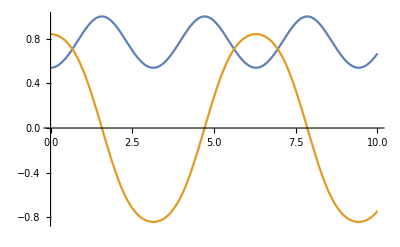

```mathematica
Plot[{Re[FNtest[x]],Im[FNtest[x]]},{x,0,10}]
```

```mathematica
FNtest2[θ_,a_:2,b_:1.1,θs_:0,θk_:0]:=Exp[ⅈ Cos[θ-θs]]Sin[θ]/(a-b Cos[θ-θk])
```

```mathematica
aThis=2;
bThis=1.1;
Manipulate[
Plot[{Re[FNtest2[x,aThis,bThis,θs,θk]],Im[FNtest2[x]]},{x,0,2π}],
{θs,0,2π},{θk,0,2π}]
```

```mathematica
2Cos[x]^2-1-Cos[2x]
```

-1+2 Cos[x]^2-Cos[2 x]

```mathematica
Simplify[-1+2 Cos[x]^2-Cos[2 x]]
```

0

```mathematica
Manipulate[
NIntegrate[FNtest2[x,aThis,bThis,θs,θk],{x,0,2π}],
{θs,0,2π},{θk,0,2π}]
```

NIntegrate::inumr: The integrand FNtest2[x,aThis,bThis,0.980177,0.] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

```mathematica
Exp[ⅈ a x1]+Exp[ⅈ a x2]
```

ⅇ^(ⅈ a x1)+ⅇ^(ⅈ a x2)

```mathematica
ExpToTrig[ⅇ^(ⅈ a x1)+ⅇ^(ⅈ a x2)]
```

Cos[a x1]+Cos[a x2]+ⅈ Sin[a x1]+ⅈ Sin[a x2]

```mathematica
Simplify[Cos[a x1]+Cos[a x2]+ⅈ Sin[a x1]+ⅈ Sin[a x2]]
```

Cos[a x1]+Cos[a x2]+ⅈ (Sin[a x1]+Sin[a x2])

```mathematica
Simplify[Cos[a x1]+Cos[a x2]]
```

Cos[a x1]+Cos[a x2]

```mathematica
(Cos[FNdotpolar[Δ/2,rB,β,θB]]-Cos[FNdotpolar[L,rB,θLl,θB]])(Cos[FNdotpolar[Δ/2,rA,β,θA]]-Cos[FNdotpolar[L,rA,θLl,θA]-FNdotpolar[k,rA,θk,θA]])
```

(Cos[1/2 rA Δ Cos[β-θA]]-Cos[k rA Cos[θA-θk]-L rA Cos[θA-θLl]]) (Cos[1/2 rB Δ Cos[β-θB]]-Cos[L rB Cos[θB-θLl]])

```mathematica
Simplify[TrigToExp[(Cos[1/2 rA Δ Cos[β-θA]]-Cos[k rA Cos[θA-θk]-L rA Cos[θA-θLl]]) (Cos[1/2 rB Δ Cos[β-θB]]-Cos[L rB Cos[θB-θLl]])]]
```

1/4 (-ⅇ^(1/2 ⅈ ⅇ^(-ⅈ (θA+θk+θLl)) (ⅇ^(ⅈ (2 θA+θLl)) k+ⅇ^(ⅈ (2 θk+θLl)) k-ⅇ^(ⅈ (2 θA+θk)) L-ⅇ^(ⅈ (θk+2 θLl)) L) rA)-ⅇ^(1/2 ⅈ ⅇ^(-ⅈ (θA+θk+θLl)) (-ⅇ^(ⅈ (2 θA+θLl)) k-ⅇ^(ⅈ (2 θk+θLl)) k+ⅇ^(ⅈ (2 θA+θk)) L+ⅇ^(ⅈ (θk+2 θLl)) L) rA)+ⅇ^(-1/4 ⅈ ⅇ^(-ⅈ (β+θA)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θA)) rA Δ)+ⅇ^(1/4 ⅈ ⅇ^(-ⅈ (β+θA)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θA)) rA Δ)) (-ⅇ^(-1/2 ⅈ ⅇ^(-ⅈ (θB+θLl)) (ⅇ^(2 ⅈ θB)+ⅇ^(2 ⅈ θLl)) L rB)-ⅇ^(1/2 ⅈ ⅇ^(-ⅈ (θB+θLl)) (ⅇ^(2 ⅈ θB)+ⅇ^(2 ⅈ θLl)) L rB)+ⅇ^(-1/4 ⅈ ⅇ^(-ⅈ (β+θB)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θB)) rB Δ)+ⅇ^(1/4 ⅈ ⅇ^(-ⅈ (β+θB)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θB)) rB Δ))

```mathematica
TrigToExp[Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

### Δ L coupling

```mathematica
(a-b)^4
```

(a-b)^4

```mathematica
Expand[(a-b)^4]
```

a^4-4 a^3 b+6 a^2 b^2-4 a b^3+b^4

```mathematica
fmn=FNminus2m3polar[k,Ll,Δ/2,θk,θLl,β];
fpl=FNminus2p3polar[k,Ll,Δ/2,θk,θLl,β];
```

```mathematica
fpl+fmn
```

2 k^2+2 Ll^2+Δ^2/2-4 k Ll Cos[θk-θLl]

```mathematica
fpl-fmn
```

2 k Δ Cos[β-θk]-2 Ll Δ Cos[β-θLl]

```mathematica
t1=FNminus2m3polar[k,Ll,Δ/2,θk,θLl,β]FNminus2p3polar[k,Ll,Δ/2,θk,θLl,β]
```

(k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])

```mathematica
t2=(-k^2+FNminus2polar[k,Ll,θk,θLl]-FNminus2polar[k,Δ/2,θk,β])FNminus2m3polar[k,Ll,Δ/2,θk,θLl,β]
```

(-k^2+Ll^2-Δ^2/4+k Δ Cos[β-θk]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])

```mathematica
t3=(-k^2+FNminus2polar[k,Ll,θk,θLl]+FNminus2polar[k,Δ/2,θk,β])FNminus2p3polar[k,Ll,Δ/2,θk,θLl,β]
```

(k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])

```mathematica
t4=k^2 (FNminus2polar[k,Ll,θk,θLl]-(Δ/2)^2)
```

k^2 (k^2+Ll^2-Δ^2/4-2 k Ll Cos[θk-θLl])

```mathematica
tNum=Simplify[t1+t2+t3+t4]
```

1/16 (32 k^4+176 k^2 Ll^2+48 Ll^4-20 k^2 Δ^2+8 Ll^2 Δ^2+Δ^4+8 k Δ (4 k^2+Δ^2) Cos[β-θk]-24 k^2 Δ^2 Cos[2 (β-θk)]-32 k^2 Ll Δ Cos[β-θLl]-8 Ll Δ^3 Cos[β-θLl]-8 Ll^2 Δ^2 Cos[2 (β-θLl)]+32 k Ll Δ^2 Cos[2 β-θk-θLl]-160 k^3 Ll Cos[θk-θLl]-192 k Ll^3 Cos[θk-θLl]+96 k^2 Ll^2 Cos[2 (θk-θLl)])

```mathematica
FullSimplify[t1+t2+t3+t4]
```

1/16 (32 k^4+48 Ll^4+8 Ll^2 Δ^2+Δ^4+4 k^2 (44 Ll^2-5 Δ^2)+8 k Δ (4 k^2+Δ^2) Cos[β-θk]-8 (3 k^2 Δ^2 Cos[2 (β-θk)]+Ll (Δ (4 k^2+Δ^2) Cos[β-θLl]+Ll Δ^2 Cos[2 (β-θLl)]+4 k (-Δ^2 Cos[2 β-θk-θLl]+(5 k^2+6 Ll^2) Cos[θk-θLl]-3 k Ll Cos[2 (θk-θLl)]))))

```mathematica
FullSimplify[t1]
```

(k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])

```mathematica
TrigReduce[(k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])]
```

1/16 (16 k^4+64 k^2 Ll^2+16 Ll^4+Δ^4-8 k^2 Δ^2 Cos[2 β-2 θk]-8 Ll^2 Δ^2 Cos[2 β-2 θLl]+32 k^2 Ll^2 Cos[2 θk-2 θLl]+16 k Ll Δ^2 Cos[2 β-θk-θLl]-64 k^3 Ll Cos[θk-θLl]-64 k Ll^3 Cos[θk-θLl])

```mathematica
2Cos[x]^2-1
```

-1+2 Cos[x]^2

```mathematica
Simplify[-1+2 Cos[x]^2]
```

Cos[2 x]

```mathematica
tDen=FNminus2polar[Ll,Δ/2,θk,β]FNplus2polar[Ll,Δ/2,θk,β]k^2t1
tDen=FullSimplify[tDen]
```

k^2 (Ll^2+Δ^2/4-Ll Δ Cos[β-θk]) (Ll^2+Δ^2/4+Ll Δ Cos[β-θk]) (k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])

k^2 (Ll^2+Δ^2/4-Ll Δ Cos[β-θk]) (Ll^2+Δ^2/4+Ll Δ Cos[β-θk]) (k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl])

```mathematica
tNum/tDen
```

(32 k^4+176 k^2 Ll^2+48 Ll^4-20 k^2 Δ^2+8 Ll^2 Δ^2+Δ^4+8 k Δ (4 k^2+Δ^2) Cos[β-θk]-24 k^2 Δ^2 Cos[2 (β-θk)]-32 k^2 Ll Δ Cos[β-θLl]-8 Ll Δ^3 Cos[β-θLl]-8 Ll^2 Δ^2 Cos[2 (β-θLl)]+32 k Ll Δ^2 Cos[2 β-θk-θLl]-160 k^3 Ll Cos[θk-θLl]-192 k Ll^3 Cos[θk-θLl]+96 k^2 Ll^2 Cos[2 (θk-θLl)])/(16 k^2 (Ll^2+Δ^2/4-Ll Δ Cos[β-θk]) (Ll^2+Δ^2/4+Ll Δ Cos[β-θk]) (k^2+Ll^2+Δ^2/4+k Δ Cos[β-θk]-Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]) (k^2+Ll^2+Δ^2/4-k Δ Cos[β-θk]+Ll Δ Cos[β-θLl]-2 k Ll Cos[θk-θLl]))

```mathematica
Simplify[%4665]
```

(32 k^4+176 k^2 Ll^2+48 Ll^4-20 k^2 Δ^2+8 Ll^2 Δ^2+Δ^4+8 k Δ (4 k^2+Δ^2) Cos[β-θk]-24 k^2 Δ^2 Cos[2 (β-θk)]-32 k^2 Ll Δ Cos[β-θLl]-8 Ll Δ^3 Cos[β-θLl]-8 Ll^2 Δ^2 Cos[2 (β-θLl)]+32 k Ll Δ^2 Cos[2 β-θk-θLl]-160 k^3 Ll Cos[θk-θLl]-192 k Ll^3 Cos[θk-θLl]+96 k^2 Ll^2 Cos[2 (θk-θLl)])/(16 Ll^4+Δ^4-8 Ll^2 Δ^2 Cos[2 (β-θk)])

```mathematica
Simplify[TrigToExp[%4666]]
```

(32 k^4-80 ⅇ^(-ⅈ (θk+θLl)) (ⅇ^(2 ⅈ θk)+ⅇ^(2 ⅈ θLl)) k^3 Ll+176 k^2 Ll^2+48 ⅇ^(-2 ⅈ (θk+θLl)) (ⅇ^(4 ⅈ θk)+ⅇ^(4 ⅈ θLl)) k^2 Ll^2-96 ⅇ^(-ⅈ (θk+θLl)) (ⅇ^(2 ⅈ θk)+ⅇ^(2 ⅈ θLl)) k Ll^3+48 Ll^4-16 ⅇ^(-ⅈ (β+θLl)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θLl)) k^2 Ll Δ-20 k^2 Δ^2-12 ⅇ^(-2 ⅈ (β+θk)) (ⅇ^(4 ⅈ β)+ⅇ^(4 ⅈ θk)) k^2 Δ^2+16 ⅇ^(-ⅈ (2 β+θk+θLl)) (ⅇ^(4 ⅈ β)+ⅇ^(2 ⅈ (θk+θLl))) k Ll Δ^2+8 Ll^2 Δ^2-4 ⅇ^(-2 ⅈ (β+θLl)) (ⅇ^(4 ⅈ β)+ⅇ^(4 ⅈ θLl)) Ll^2 Δ^2-4 ⅇ^(-ⅈ (β+θLl)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θLl)) Ll Δ^3+Δ^4+4 ⅇ^(-ⅈ (β+θk)) (ⅇ^(2 ⅈ β)+ⅇ^(2 ⅈ θk)) k Δ (4 k^2+Δ^2))/(16 Ll^4-4 ⅇ^(-2 ⅈ (β+θk)) (ⅇ^(4 ⅈ β)+ⅇ^(4 ⅈ θk)) Ll^2 Δ^2+Δ^4)

### F_3

```mathematica
SinIntegral
```

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2),{x,0,k2},Assumptions->k2>0&& m2>0]
```

ⅇ^(-ⅈ Cc m2) (-ExpIntegralEi[ⅈ Cc m2]+ExpIntegralEi[ⅈ Cc (k2+m2)])

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2),{x,k2,∞},Assumptions->k2>0&& m2>0]
```

ConditionalExpression[ⅇ^(-ⅈ Cc m2) Gamma[0,-ⅈ Cc (k2+m2)], Im[Cc]>0]

```mathematica
Clear[A,B,θ];
Integrate[1/(A-B Cos[θ]),{θ,0,2π},Assumptions->A> B>0]
```

(2 π)/(√(A^2-B^2))

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2),{x,0,k2},Assumptions->k2>0&& m2>0]
```

ⅇ^(-ⅈ Cc m2) (-ExpIntegralEi[ⅈ Cc m2]+ExpIntegralEi[ⅈ Cc (k2+m2)])

```mathematica
ⅇ^(-ⅈ Cc m2) (-Ei[ⅈ Cc m2]+Ei[ⅈ Cc (k2+m2)])
```

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(k2-x+m2),{x,0,k2},Assumptions->k2>0&& m2>0]
```

ⅇ^(ⅈ Cc (k2+m2)) (Gamma[0,ⅈ Cc m2]-Gamma[0,ⅈ Cc (k2+m2)])

```mathematica
Table[ExpIntegralEi[-z]+Gamma[0,z],{z,0,1,.1}]
```

Infinity::indet: Indeterminate expression -∞+∞ encountered.

{Indeterminate,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2)/2+Exp[ⅈ Cc x]/(k2-x+m2),{x,0,k2},Assumptions->k2>0&& m2>0]
```

1/2 ⅇ^(-ⅈ Cc m2) (-ExpIntegralEi[ⅈ Cc m2]-2 ⅇ^(ⅈ Cc (k2+2 m2)) (ExpIntegralEi[-ⅈ Cc m2]-ExpIntegralEi[-ⅈ Cc (k2+m2)])+ExpIntegralEi[ⅈ Cc (k2+m2)])

```mathematica
1/2 ⅇ^(-ⅈ Cc m2) (-Ei[ⅈ Cc m2]+Ei[ⅈ Cc (k2+m2)])
-   ⅇ^(ⅈ Cc (k2+ m2)) (Ei[-ⅈ Cc m2]-Ei[-ⅈ Cc (k2+m2)])
```

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2),{x,k2,∞},Assumptions->k2>0&& m2>0]
```

ConditionalExpression[ⅇ^(-ⅈ Cc m2) Gamma[0,-ⅈ Cc (k2+m2)], Im[Cc]>0]

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x-k2+m2),{x,k2,∞},Assumptions->k2>0&& m2>0]
```

ConditionalExpression[ⅇ^(ⅈ Cc (k2-m2)) Gamma[0,-ⅈ Cc m2], Im[Cc]>0]

```mathematica
Clear[Cc];
Integrate[-Exp[ⅈ Cc x]/(x+m2)/4+Exp[ⅈ Cc x]/(x-k2+m2)/2,{x,k2,∞},Assumptions->k2>0&& m2>0]
```

$Aborted

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(k2-x+m2),{x,0,k2},Assumptions->k2>0&& m2>0]
```

ⅇ^(ⅈ Cc (k2+m2)) (Gamma[0,ⅈ Cc m2]-Gamma[0,ⅈ Cc (k2+m2)])

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x-k2+m2),{x,k2,∞},Assumptions->k2>0&& m2>0]
```

ConditionalExpression[ⅇ^(ⅈ Cc (k2-m2)) Gamma[0,-ⅈ Cc m2], Im[Cc]>0]

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2),{x,0,k2},Assumptions->k2>0&& m2>0]
```

ⅇ^(-ⅈ Cc m2) (-ExpIntegralEi[ⅈ Cc m2]+ExpIntegralEi[ⅈ Cc (k2+m2)])

```mathematica
Clear[Cc];
Integrate[Exp[ⅈ Cc x]/(x+m2),{x,k2,∞},Assumptions->k2>0&& m2>0]
```

ConditionalExpression[ⅇ^(-ⅈ Cc m2) Gamma[0,-ⅈ Cc (k2+m2)], Im[Cc]>0]

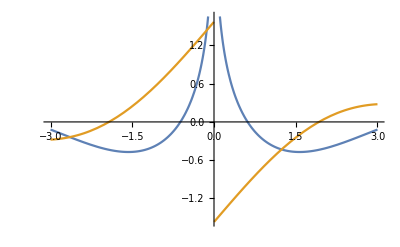

```mathematica
Plot[{Re[Gamma[0,ⅈ x]],Im[Gamma[0,ⅈ x]]},{x,-3,3}]
```

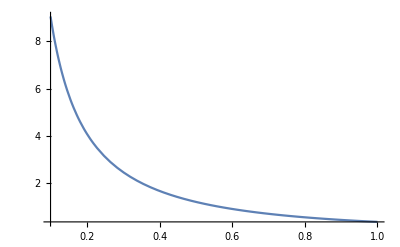

```mathematica
Plot[Exp[-t]/t,{t,0.1,1},PlotRange->All]
```

### Exp

```mathematica
Simplify[Re[Exp[ⅈ a]],Assumptions->a ∈ Reals]
```

Re[ⅇ^(ⅈ a)]

```mathematica
Simplify[ExpToTrig[ⅇ^(ⅈ a Exp[ⅈ b])],Assumptions->a ∈ Reals&&b ∈ Reals]
```

Cos[a (Cos[b]+ⅈ Sin[b])]+ⅈ Sin[a (Cos[b]+ⅈ Sin[b])]

```mathematica
Simplify[TrigToExp[Cos[a (Cos[b]+ⅈ Sin[b])]+ⅈ Sin[a (Cos[b]+ⅈ Sin[b])]]]
```

ⅇ^(ⅈ a ⅇ^(ⅈ b))

```mathematica
Simplify[Cos[a Cos[b]+ⅈ a Sin[b]]+ⅈ Sin[a Cos[b]+ⅈ a Sin[b]]]
```

Cos[a (Cos[b]+ⅈ Sin[b])]+ⅈ Sin[a (Cos[b]+ⅈ Sin[b])]

```mathematica
ExpToTrig[Re[ⅇ^(ⅈ a)]]
```

-Im[Sin[a]]+Re[Cos[a]]

## The resulting analytical form

## Full calculation by Bin

### Calculation of the integral

```mathematica
FourierTransform[1/(kx^2+ky^2),{kx,ky},{rx,ry}]
```

1/2 (-HeavisideTheta[-rx] (2 Log[-rx]+Log[1+ry^2/rx^2])-HeavisideTheta[rx] (2 Log[rx]+Log[1+ry^2/rx^2]))

```mathematica
FourierTransform[1/(kx^2+ky^2),kx,x]
```

1/(2 ky)ⅇ^(-ky x) √(π/2) ((-1+ⅇ^(2 ky x)) Sign[x] (-1+Sign[Abs[Re[ky]]])+2 (ⅇ^(2 ky x) HeavisideTheta[-x Sign[Re[ky]]]+HeavisideTheta[x Sign[Re[ky]]]) Sign[Re[ky]])

```mathematica
FourierTransform[1/(2 ky)ⅇ^(-ky x) √(π/2) ((-1+ⅇ^(2 ky x)) Sign[x] (-1+Sign[Abs[Re[ky]]])+2 (ⅇ^(2 ky x) HeavisideTheta[-x Sign[Re[ky]]]+HeavisideTheta[x Sign[Re[ky]]]) Sign[Re[ky]]),ky,y]
```

1/2 (-HeavisideTheta[-x] (2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 Log[x]+Log[1+y^2/x^2]))

```mathematica
FullSimplify[1/2 (-HeavisideTheta[-x] (2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 Log[x]+Log[1+y^2/x^2]))]
```

-HeavisideTheta[-x] Log[-x]-HeavisideTheta[x] Log[x]-1/2 (HeavisideTheta[-x]+HeavisideTheta[x]) Log[1+y^2/x^2]

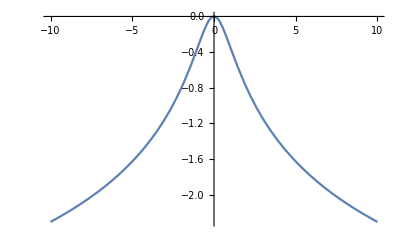

```mathematica
With[{y=1},Plot[-HeavisideTheta[-x] Log[-x]-HeavisideTheta[x] Log[x]-1/2 (HeavisideTheta[-x]+HeavisideTheta[x]) Log[1+y^2/x^2],{x,-10,10}]]
```

```mathematica
testf[a_:1,b_:1]:=a+b
```

```mathematica
testf[1,2]
```

3

```mathematica
Drop[.001]
```

0.001

```mathematica
ft01=-EulerGamma-Log[r]
```

-EulerGamma-Log[r]

We would like to evaluate the Fourier Transform of

```mathematica
itg:=1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2)
```

```mathematica
FourierTransform[1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2),{kx,ky},{x,y}]
```

$Aborted

Since it is scalar, we put set {x,y}/r as the y axis with r the modulus of {x,y}. Then it is trivial to integrate out kx firxt.

It is trivial to integrate out, say, kx :

```mathematica
intkxana[ky_,{lx_,ly_}]=FullSimplify[I HeavisideTheta[ky]Residue[itg,{kx,I ky}]]+FullSimplify[I HeavisideTheta[-ky]Residue[itg,{kx,-I ky}]]+FullSimplify[I HeavisideTheta[ky-ly]Residue[itg,{kx,lx+I (ky-ly)}]]+FullSimplify[I HeavisideTheta[-ky+ly]Residue[itg,{kx,lx-I (ky-ly)}]]
```

0

```mathematica
ftkx:=(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))
```

```mathematica
intkx[ky_,{lx_,ly_}]:=1/(2π)NIntegrate[1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2),{kx,-Infinity,Infinity}]
```

```mathematica
cond:=r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0 &&ky∈Reals&&lx∈Reals&&ly∈Reals
```

the first term

#### Term 1

```mathematica
ftkx[[1]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))

```mathematica
dem:=2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly)
```

```mathematica
apky= Apart[((lx-ⅈ ly) (lx+ⅈ ly))/dem,ky]
```

ⅈ/(2 ky)-ⅈ/(2 ky-ⅈ lx-ly)

```mathematica
term11=Assuming[cond,1/l^2 FourierTransform[ftkx[[1]] dem apky[[1]],ky,r]//FullSimplify]
```

-(EulerGamma+(ⅈ π)/2+Log[r])/(2 l^2 √(2 π))

```mathematica
ftkx[[1]] dem apky[[2]]
```

HeavisideTheta[-ky]/(2 ky-ⅈ lx-ly)

```mathematica
Numerator[ftkx[[1]] dem apky[[2]]]
```

HeavisideTheta[-ky]

```mathematica
FullSimplify[Expand[√(2 π)FourierTransform[HeavisideTheta[-ky],ky,y]]]
Assuming[cond,FullSimplify[Expand[√(2 π)FourierTransform[1/(2 ky-ⅈ lx-ly),ky,y]]]]
```

-ⅈ/y+π DiracDelta[y]

ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[y Sign[Im[ly]+Re[lx]]] Sign[Im[ly]+Re[lx]]

```mathematica
Integrate[ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[y ](-ⅈ/(r-y)+π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
Integrate[-ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[-y ](-ⅈ/(r-y)+π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r], Re[r]<0&&Im[r]==0&&Im[ly]+Re[lx]>0]

ConditionalExpression[-ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r], Im[ly]+Re[lx]<0&&Re[r]>0&&Im[r]==0]

```mathematica
t12:=-1/(2 π Sqrt[2π] l^2)ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r]
```

```mathematica
term1=term11+t12
```

-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2 √(2 π))-(EulerGamma+(ⅈ π)/2+Log[r])/(2 l^2 √(2 π))

#### Term 2

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
ftkx[[2]]
```

(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

```mathematica
Denominator[ftkx[[2]]]
```

2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly)

```mathematica
apky= Apart[((lx-ⅈ ly) (lx+ⅈ ly))/Denominator[ftkx[[2]]],ky]
```

-ⅈ/(2 ky)+ⅈ/(2 ky+ⅈ lx-ly)

```mathematica
Numerator[ftkx[[2]]] apky[[1]]
```

HeavisideTheta[ky]/(2 ky)

```mathematica
term21=Assuming[cond,1/l^2 FourierTransform[Numerator[ftkx[[2]]] apky[[1]],ky,r]//FullSimplify]
```

(ⅈ (2 ⅈ EulerGamma+π+2 ⅈ Log[r]))/(4 l^2 √(2 π))

```mathematica
term22=Assuming[cond,1/(lx^2+ly^2)FourierTransform[Numerator[ftkx[[2]]]apky[[2]],ky,r]//FullSimplify]
```

(ⅇ^(1/2 (lx+ⅈ ly) r) (-ⅈ π+2 CosIntegral[1/2 ⅈ (lx+ⅈ ly) r]-2 SinhIntegral[1/2 (lx+ⅈ ly) r]))/(4 (lx^2+ly^2) √(2 π))

```mathematica
FullSimplify[Expand[√(2 π)FourierTransform[Numerator[ftkx[[2]]] ,ky,y]]]
Assuming[cond,FullSimplify[Expand[√(2 π)FourierTransform[apky[[2]],ky,y]]]]
```

-1/y+ⅈ π DiracDelta[y]

ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[-y Sign[lx]] Sign[lx]

```mathematica
Integrate[ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[-y ] (-1/(r-y)+ⅈ π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
Integrate[-ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[y](-1/(r-y)+ⅈ π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r], Re[lx]>Im[ly]&&Re[r]>0&&Im[r]==0]

ConditionalExpression[-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r], Re[r]<0&&Im[r]==0&&Re[lx]<Im[ly]]

```mathematica
t22:=1/(2 π Sqrt[2π] l^2)(-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r])
```

```mathematica
term22/.{lx->3,ly->0.3,r->1.0}
t22/.{lx->3,ly->0.3,r->1.0}
```

-0.00978113+0.000714427 ⅈ

-(0.0889105-0.00649414 ⅈ)/l^2

```mathematica
term2=term21+t22
```

-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2 √(2 π))+(ⅈ (2 ⅈ EulerGamma+π+2 ⅈ Log[r]))/(4 l^2 √(2 π))

```mathematica
ftkx[[1;;2]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

From this, we can see how the two related to each other :

```mathematica
(Assuming[cond,Conjugate[ftkx[[1]]]//FullSimplify]/.Conjugate[x_]->x/.{ky->-ky}//FullSimplify)/.{lx->-lx,ly->-ly}//FullSimplify
```

(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

```mathematica
(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))-ftkx[[2]]
```

0

```mathematica
((Assuming[cond&&l>0,Conjugate[term1]//FullSimplify])/.{lx->-lx,ly->-ly}//FullSimplify)/.Conjugate[Gamma[0,1/2 (lx-ⅈ ly) r]]->Gamma[0,1/2 (lx+ⅈ ly) r]
```

-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))

```mathematica
-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))-term2//FullSimplify
```

0

Check!

#### Term 3

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
((FullSimplify[(ftkx[[3]]/.{ky->ky+ly})]))-(ftkx[[2]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

This tells us that

```mathematica
term3=FullSimplify[Exp[I ly r] (term2/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma-ⅈ π+2 ⅇ^(-1/2 (lx+ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

#### Term 4

```mathematica
((FullSimplify[(ftkx[[4]]/.{ky->ky+ly})]))-(ftkx[[1]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

```mathematica
term4=FullSimplify[Exp[I ly r] (term1/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma+ⅈ π+2 ⅇ^(1/2 (lx-ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

```mathematica
cond
```

r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0&&ky∈Reals&&lx∈Reals&&ly∈Reals

#### Final

```mathematica
final=Expand[Assuming[cond,Simplify[Sqrt[2π] (term1+term2+term3+term4)]]]
```

-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2

Note that this is the result for ϕx = π/2. lx=l cos(ϕl-π/2) and ly=l sin(ϕl-π/2).

```mathematica
ft02[{l_,ϕl_},{r_,ϕx_}]=((-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2)/.{lx->l Cos[ϕl-ϕx+π/2],ly->l Sin[ϕl-ϕx+π/2]})
```

-EulerGamma/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) EulerGamma)/l^2-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) Log[r])/l^2

```mathematica
ft01[{l_,ϕl_},{r_,ϕx_}]=(-EulerGamma-Log[r])/l^2
```

(-EulerGamma-Log[r])/l^2

```mathematica
F01[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft01[{l,ϕk},{r,ϕx}]
]
F02[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft02[{l,ϕk},{r,ϕx}]
]
```

```mathematica
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=( F01[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F01[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F01[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F01[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])-( F02[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F02[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F02[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F02[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])
```

```mathematica
num[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=1/(2π)NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(1/(lx^2+ly^2)-1/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
```

```mathematica
bu={3.0,0.1};
x1u={1.0,0.5};
x2u={1.5,0.25};
x3u={0.1,0.75};
x4u={1.3,2.5};
ku={2.2,1.8};
num[bu,x1u,x2u,x3u,x4u,{2.2,1.8}]
```

0.00511557+0.00174474 ⅈ

```mathematica
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.00511521+0.00174514 ⅈ

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
num[bu,x1u,x2u,x3u,x4u,ku]
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.289065+0.303098 ⅈ

0.289015+0.303045 ⅈ

### Dipole Radiation

```mathematica
F01R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky} F01[{x,y},{kx,ky}]]
```

{kx F01[{x,y},{kx,ky}],ky F01[{x,y},{kx,ky}]}

```mathematica
F02R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky}F02[{x,y},{kx,ky}]+I{D[F02[{x,y},{kx,ky}],x],D[F02[{x,y},{kx,ky}],y]}]
```

{1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma kx-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) kx Log[x^2+y^2]),1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma ky+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) ky Log[x^2+y^2])}

```mathematica
numx[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(lx/(lx^2+ly^2)-(lx-kx)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
numy[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(ly/(lx^2+ly^2)-(ly-ky)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=2π(( F01R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F01R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F01R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F01R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)])-( F02R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F02R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F02R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F02R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]))
```

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
{numx[bu,x1u,x2u,x3u,x4u,ku],numy[bu,x1u,x2u,x3u,x4u,ku]}
ana[bu,x1u,x2u,x3u,x4u,ku]
```

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

```mathematica
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=ana[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
showdσ[bu_,x1u_,x2u_,x3u_,x4u_,kT_]:=Module[{ϕ},
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x3u,bu+x4u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x4u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[ParametricPlot[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}] Cos[2(ϕ)],{ϕ,0,2π}]/NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

### kT~1/r

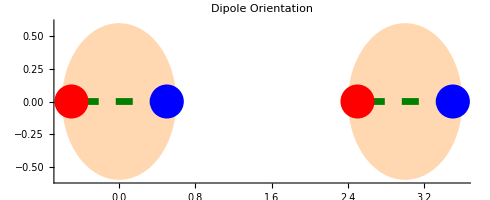

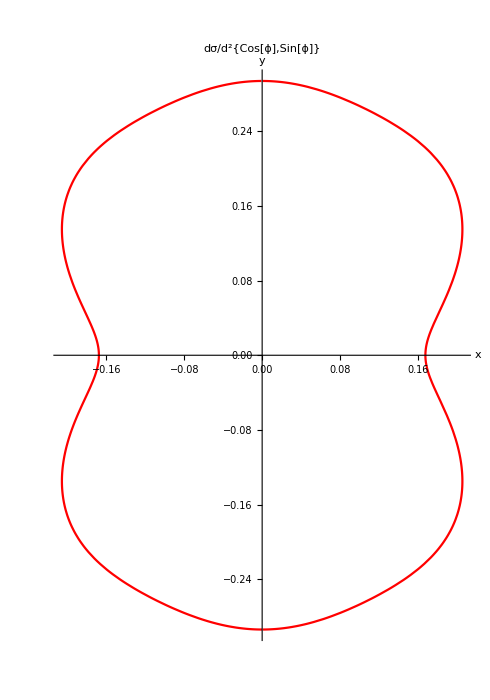

v_2=-0.114285-4.15293×10^-20 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

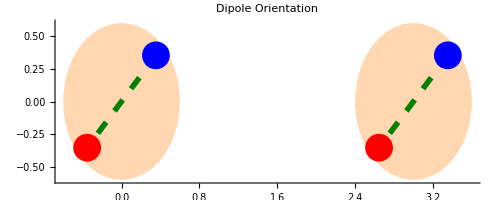

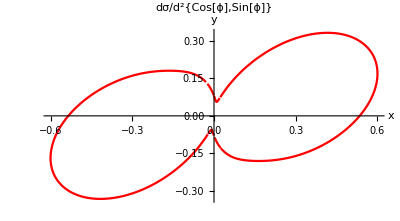

v_2=0.364805+1.18451×10^-18 ⅈ

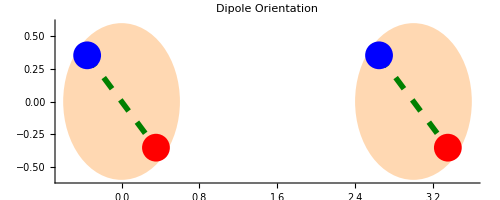

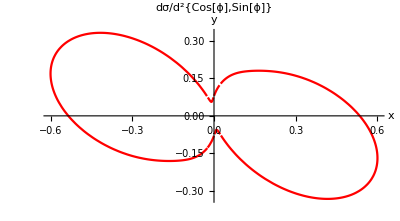

v_2=0.364805+3.09828×10^-18 ⅈ

```mathematica
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

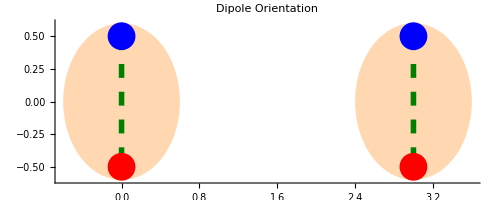

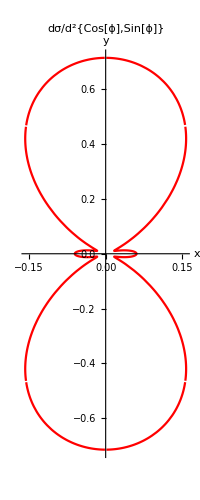

v_2=-0.669888-3.62969×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Therefore, we have v2 in hadron - hadron collisions.

### kT>>1/r

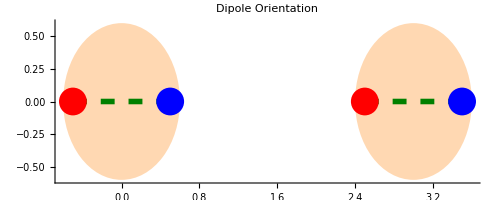

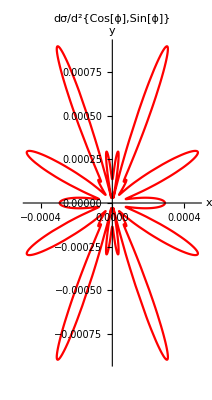

v_2=-0.0641272+0. ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

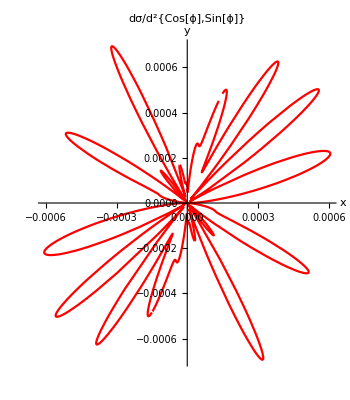

v_2=-0.0142743+0. ⅈ

-Graphics-

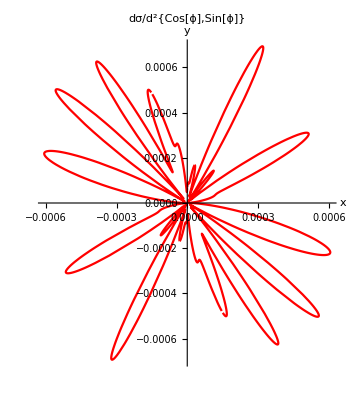

v_2=-0.0142743+0. ⅈ

```mathematica
kT=10.0;
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

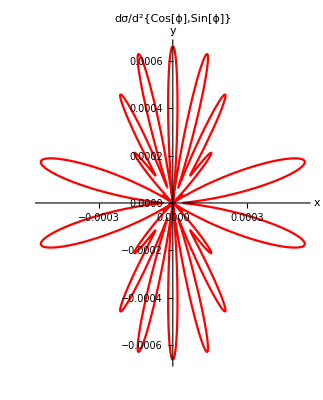

v_2=-0.0402007+0. ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for large k_T, the two partons can be treated as independent and the soft gluon can be taken as radiated uncoherently from the two individual partons.

### kT<<1/r

-Graphics-

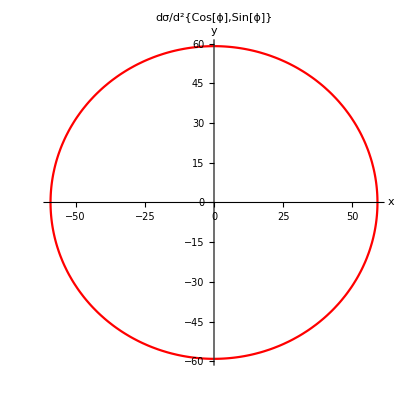

v_2=0.000347844+9.38067×10^-19 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

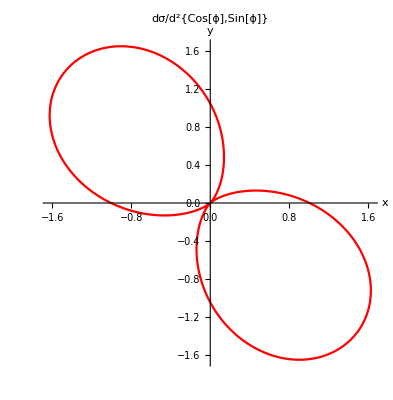

v_2=-0.0103349+8.84144×10^-19 ⅈ

-Graphics-

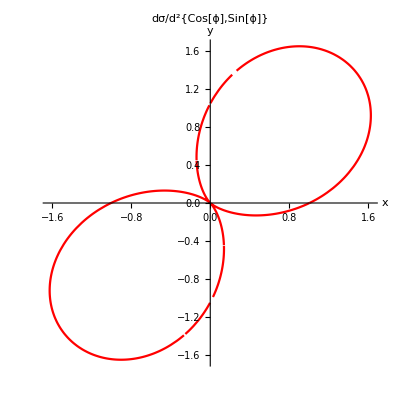

v_2=-0.0103349-2.30944×10^-19 ⅈ

```mathematica
x1u={1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

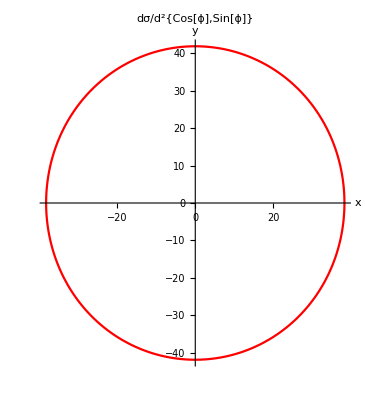

v_2=-0.0226608-1.3638×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for small k_T, radiation from the two partons can not distinguish the seperation of the dipole, hence v_2 is also negligible.

## Dipole cross section



```mathematica
ParametricPlot[{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π}]
```